# When predators help prey adapt and persist in a changing environment

Created with Mathematica 9.0.1.0

## Preliminaries

For uniformity among figures

```mathematica
LabelSize=25; (*size of axis label text*)
FigureSize=650;  (*size of figure*)
TickSize=16;  (*size of tick text*)
Pad={{70,25},{70,10}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
xlabpos={0.5,-0.1};(*relative location of x axis label position*)
LetterSize=20;  (*size of text in stability plots*)
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*set current directory to be location of this file*)
imagedir="IMAGES/";(*directory to save figures in*)
datadir = "SIMULATIONS/";(*parent directory with simulation results*) (*NOTE: data not provided in github, but example scripts can be used to generate one's own data*)
```

Get package for plotting means with error bars

```mathematica
Needs["ErrorBarPlots`"]
```

## Generalist example 1A: selective push (predate maladapted more; quadratic selection)

### Model set-up

Let the relative mortality rate m of an individual be a quadratic function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and minimum death rate mmin

```mathematica
m[z_,N_]:=mmin+γ(θ-z)^2
```

where N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

The population mean per capita mortality rate is then

```mathematica
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

mmin+γ (Vz+(barz-θ)^2)

Let k * f[z,N] be the per capita rate of consumption of prey with trait value z by predators, with

```mathematica
f[z_,N_]:=(1+γk (z-θ)^2)
```

where k is the overall predation intensity and γk describes how quickly predator attack increases as prey trait values deviate from the environmental optimum (e.g., as prey become increasingly weaker/malnourished).

The population mean per capita predation rate is then

```mathematica
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γk>0}]//FullSimplify
```

k (1+γk (Vz+(barz-θ)^2))

Finally we let the per capita birth rate be

```mathematica
b[z_,N_]:=bmax (Rtot-N)
```

where Rtot is the total amount of resources in the (closed) system and bmax is the maximum birth rate, achieved when all resources are available (i.e., no resources contained in prey).

Mean growth rate is then

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}]//FullSimplify
```

bmax (-N+Rtot)

Then the growth rate of a population of N individuals with trait value z is

```mathematica
dNdtz=N(b[z,N]-m[z,N]-k f[z,N])
```

N (-mmin+bmax (-N+Rtot)-k (1+γk (z-θ)^2)-γ (-z+θ)^2)

Integrating over all individuals, the population mean growth rate dN/dt is

```mathematica
dNdt=Integrate[dNdtz p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0,γk>0}]//FullSimplify
```

-N (mmin+bmax (N-Rtot)+k (1+γk (Vz+(barz-θ)^2))+γ (Vz+(barz-θ)^2))

### Rate of evolution and equilibrium phenotypic variance

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born in a population that previously had mean trait value barz and density N, the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes (assuming a normal phenotype distribution with mean barz and variance Vz)

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

Given a prey individual is chosen to give birth, the probability it has trait value zP is

```mathematica
pzbirth=(b[zP,N]p[zP])/barb;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zP]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zP, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zP,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected trait mean after a selective birth is then

```mathematica
meanafterbirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected trait variance after a selective birth is

```mathematica
varafterbirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Death

PREY DEATH

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

The probability an individual with trait value zD dies is

```mathematica
pzdeath=(m[zD,N]p[zD])/barm;
```

After death the expected trait mean is

```mathematica
meanafterdeath=Simplify[Integrate[Factor[meand*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

After death the expected variance is

```mathematica
varafterdeath=Simplify[Integrate[Factor[vard*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

PREDATION

Given an individual is consumed by a predator, the probability it has trait value zC is

```mathematica
pzpred=(k f[zC,N]p[zC])/barkf;
```

After predation the expected trait mean is

```mathematica
meanafterpred=Simplify[Integrate[Factor[meand*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

After predation the expected variance is

```mathematica
varafterpred=Simplify[Integrate[Factor[vard*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Rate of evolution

Using the law of total probability, the expected mean trait after a small time Δt is

```mathematica
Ebarzdt=(1-Δt N(barb+barm+barkf))barz+Δt N(barb* meanafterbirth+barm* meanafterdeath+barkf*meanafterpred);
```

The rate of change in the mean trait value is thus

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp=FullSimplify[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,Vz>0]
```

-2 Vz (γ+k γk) (barz-θ)

#### Equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+barkf))Vz+Δt N(barb *varafterbirth+ barm *varafterdeath+ barkf *varafterdeath);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1;
```

When the random effect is small (and therefore the variance is also small) we have, at equilibrium, approximately

```mathematica
Normal[Series[dVdtApp/.Vz->ϵ Vz/.α->α ϵ^(1/2),{ϵ,0,1}]]/.ϵ->1;
Veq=Solve[%==0,Vz]//FullSimplify
```

{{Vz→(2 (-2+N-Rtot) α^2)/(N-Rtot)}}

And when the amount of available resources R = Rtot-N is large (much greater than 2), this is approximately

```mathematica
VzEqApp=Normal[Series[Vz/.Veq/.N->Rtot-R/ϵ,{ϵ,0,0}]]
```

{2 α^2}

### Quick [can run instead of section directly above if model unchanged]

```mathematica
dNdt=-N (mmin+bmax (N-Rtot)+k (1+γk (Vz+(barz-θ)^2))+γ (Vz+(barz-θ)^2));
```

```mathematica
dbarzdt=-(2 N Vz (γ+k γk) (barz-θ))/(-1+N);
```

```mathematica
dbarzdtApp=-2 Vz (γ+k γk) (barz-θ);
```

```mathematica
dVdt=(N (-2 k (1+N)^2 Vz (1+barz^2 γk+Vz γk-2 barz γk θ+γk θ^2) (mmin+γ (barz^2+Vz+2 N Vz-2 barz θ+θ^2))-(mmin+γ (barz^2+Vz-2 barz θ+θ^2)) (2 mmin (1+N)^2 Vz-bmax (-1+N)^2 (N-Rtot) ((2+N) Vz-2 N α^2)+2 (1+N)^2 Vz γ (barz^2+Vz+2 N Vz-2 barz θ+θ^2))))/(2 (-1+N^2)^2 (mmin+γ (barz^2+Vz-2 barz θ+θ^2)));
```

### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[dNdt/N==0/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→-(k+mmin-bmax Rtot+(L^2+Vz) γ+k (L^2+Vz) γk)/bmax}

When the optimum changes at rate κ, and density remains at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarzdtApp==κ/.Neq/.θ->L+barz,{L}][[1]]//FullSimplify
```

{L→κ/(2 Vz γ+2 k Vz γk)}

The fastest rate of environmental change that the population can persist at is less than the rate that causes density to go to zero. This critical rate is thus

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ]
```

{{κ→-2 ⅈ Vz √(γ+k γk) √(k+mmin-bmax Rtot+Vz γ+k Vz γk)},{κ→2 ⅈ Vz √(γ+k γk) √(k+mmin-bmax Rtot+Vz γ+k Vz γk)}}

When bmax Rtot is great enough for persistence in an unchanging environment the answer is a real number (because the term inside the square root in the denominator is then imaginary).

How does this critical rate change with predation intensity? We first take the derivative with respect to predation intensity

```mathematica
dkck=D[κ/.kc[[1]],k]//FullSimplify
```

-(ⅈ Vz (γ+2 Vz γ γk+γk (mmin-bmax Rtot+2 k (1+Vz γk))))/(√(γ+k γk) √(k+mmin-bmax Rtot+Vz γ+k Vz γk))

And so the predation rate that maximizes the critical rate of environmental change is

```mathematica
Collect[Solve[dkck==0,k],γ,Factor]
```

{{k→-(mmin-bmax Rtot)/(2 (1+Vz γk))-(γ (1+2 Vz γk))/(2 γk (1+Vz γk))}}

Numerical demonstration that the critical rate of environmental change can increase with increasing predation (over some range of k):

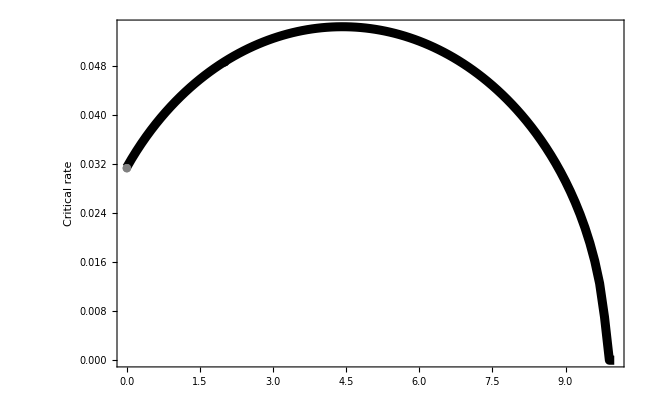

```mathematica
Show[
ListPlot[Table[{k,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1]},{k,0,10,0.1}],PlotStyle->{Thickness[0.01],Black},PlotRange->{0,All},Joined->True],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}},PlotStyle->Blue,PlotMarkers->{Automatic,Large}],
ListPlot[{{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}},PlotStyle->Brown,PlotMarkers->{Automatic,Large}],*)
ListPlot[{{0,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->0]}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{2,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->2]}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
Frame->True, 
FrameLabel->{Style[(*"Predation intensity"*)"",LabelSize],Style["Critical rate",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
(*Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},*)
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

(*Export[imagedir<>"SelectiveGeneralistCriticalRatePredation.eps",%];*)
```

But note that when selection on background mortality is much greater than selection on predator mortality, the critical rate can monotonically decrease with predation intensity

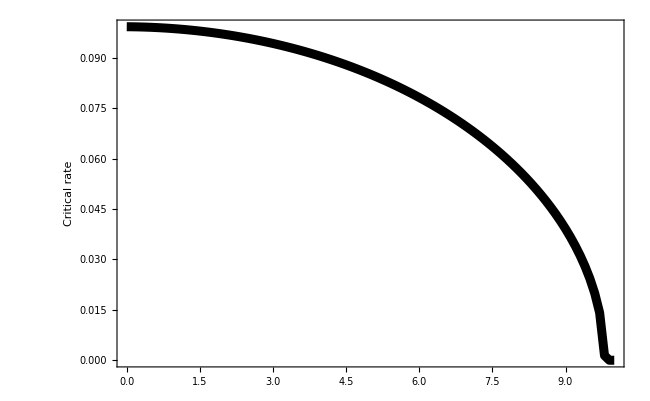

```mathematica
Show[
ListPlot[Table[{k,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->10/.α->0.05/.γk->1]},{k,0,10,0.1}],PlotStyle->{Thickness[0.01],Black},PlotRange->{0,All},Joined->True],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}},PlotStyle->Blue,PlotMarkers->{Automatic,Large}],
ListPlot[{{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}},PlotStyle->Brown,PlotMarkers->{Automatic,Large}],*)
(*ListPlot[{{0,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->0]}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{2,Re[κ/.kc[[1]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->2]}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],*)
Frame->True, 
FrameLabel->{Style[(*"Predation intensity"*)"",LabelSize],Style["Critical rate",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
(*Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},*)
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

(*Export[imagedir<>"SelectiveGeneralistCriticalRatePredation.eps",%];*)
```

### Applying the general analysis

The per capita growth rate

```mathematica
g[N_,barz_,k_]:=dNdt/N//Evaluate
```

The rate of evolution is approximately

```mathematica
dzdt=VA D[g[N,barz,k],barz]//Simplify
```

-2 VA (γ+k γk) (barz-θ)

This does not depend on N, but the direct selective effect of predation satisfies Equation 3

```mathematica
eq3=D[dzdt,k]
```

-2 VA γk (barz-θ)

The equilibrium population density as a function of trait value

```mathematica
nhat=Solve[g[N,barz,k]==0,N]//Flatten//Simplify
```

{N→-(mmin-bmax Rtot+barz^2 γ+Vz γ-2 barz γ θ+γ θ^2+k (1+barz^2 γk+Vz γk-2 barz γk θ+γk θ^2))/bmax}

The critical lag (that which causes population density to go to zero)

```mathematica
critlag=Solve[0==N/.nhat/.barz->barzc,barzc][[1]]
```

{barzc→(2 γ θ+2 k γk θ-√((-2 γ θ-2 k γk θ)^2-4 (γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk+γ θ^2+k γk θ^2)))/(2 (γ+k γk))}

The strength of selection at the critical rate

```mathematica
h=D[g[N,barz,k],barz]/.N->0/.barz->barzc
```

-2 γ (barzc-θ)-2 k γk (barzc-θ)

The terms in Equation 5 (first line)

```mathematica
{D[h,k],D[h,barzc],D[barzc/.critlag,k]}/.critlag//FullSimplify
```

{(2 γk √(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))/(γ+k γk),-2 (γ+k γk),(γ-mmin γk+bmax Rtot γk)/(2 (γ+k γk) √(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))}

Equation 5 (first line)

```mathematica
eq5=VA(D[h,k]+D[h,barzc]D[barzc/.critlag,k])/.critlag//FullSimplify
```

-(VA (γ+2 Vz γ γk+γk (mmin-bmax Rtot+2 k (1+Vz γk))))/(√(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))

Equation 5 is positive when

```mathematica
Reduce[0>γ+2 Vz γ γk+γk (mmin-bmax Rtot+2 k (1+Vz γk))&&γ>0&&γk>0&&Vz>0,k,Reals]
```

γk>0&&γ>0&&Vz>0&&k<(-γ-mmin γk+bmax Rtot γk-2 Vz γ γk)/(2 γk+2 Vz γk^2)

The terms in Equation 5 (second line)

```mathematica
{D[D[g[0,barz,k],barz],k],D[D[g[0,barz,k],barz],barz],D[barzc/.critlag,k]}/.barz->barzc/.critlag//FullSimplify
```

{(2 γk √(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))/(γ+k γk),-2 (γ+k γk),(γ-mmin γk+bmax Rtot γk)/(2 (γ+k γk) √(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))}

Equation 5 (second line)

```mathematica
VA(D[D[g[0,barz,k],barz],k]+D[D[g[0,barz,k],barz],barz]D[barzc/.critlag,k])/.barz->barzc/.critlag//FullSimplify
```

-(VA (γ+2 Vz γ γk+γk (mmin-bmax Rtot+2 k (1+Vz γk))))/(√(-(γ+k γk) (k+mmin-bmax Rtot+Vz γ+k Vz γk)))

Check that this is the same as directly differentiating the critical rate

```mathematica
Solve[κ==dzdt,barz]//Flatten//Simplify;
Solve[0==N/.nhat/.%,κ][[2]]//Simplify;
D[κ/.%,k]//Simplify
```

(ⅈ VA (γ+2 Vz γ γk+γk (mmin-bmax Rtot+2 k (1+Vz γk))))/(√(γ+k γk) √(k+mmin-bmax Rtot+Vz γ+k Vz γk))

### Temporal dynamics (with simulation results)

-Graphics-

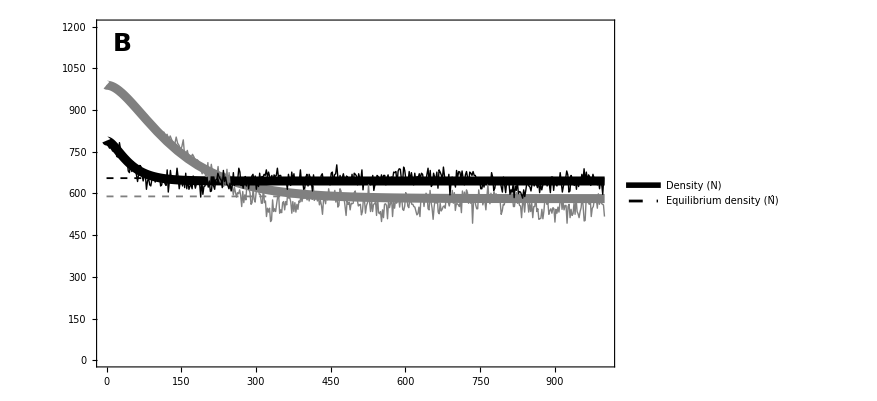

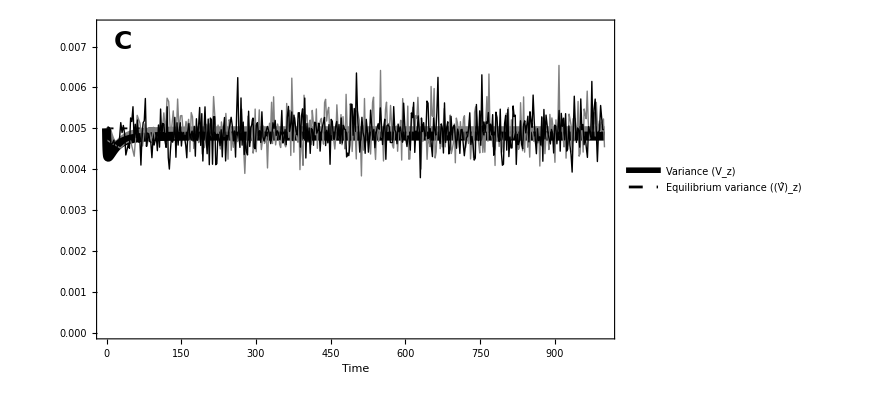

```mathematica
(*predation rates to compare*)
numlines=2;
Table[c[i]=(i-1)*2,{i,1,numlines}];

(*plotting colors*)
Table[col[i]=GrayLevel[1-i/numlines],{i,1,numlines}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;
γk=1;
tmax=1000;
κ =2/100;

(*initial values*)
n0=Rtot-(mmin+k)/bmax;z0=0;Vz0=VzEqApp[[1]];

(*numerically solve coupled equation*)
Table[
sol[i]=NDSolve[{
n'[t]==(dNdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
z'[t]==(dbarzdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
Vz'[t]==(dVdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
n[0]==n0,
z[0]==z0,
Vz[0]==Vz0
}/.k->c[i],{n,z,Vz},{t,0,tmax},MaxSteps->30000],
{i,1,numlines}];

(*simulation results*)
simdir[1]=datadir<>"PUSH/CEQUALS0/k0pt02/";
simdir[2]=datadir<>"PUSHB/k0pt02/";
rep="1";
Table[zpdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,numlines}];
Table[Pdat[i]= Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,numlines}];

(*plot trait dynamics*)
Legended[
Show[
Plot[κ t,{t,0,tmax},PlotStyle->{Black,Thick}],(*optimal*)
Table[Plot[κ t-L/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed},PlotRange->{0,All}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[z[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,numlines}],(*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,1]]},{j,1,Dimensions[Pdat[i]][[1]],1}],PlotRange->All,PlotStyle->col[i], Joined->True],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,All}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
{
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Optimum phenotype (θ)",LabelSize],
Style["Mean phenotype (z̄)",LabelSize],
Style["Steady-state expectation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
] (*,
Placed[
LineLegend[{
Directive[Black,Thickness[0.25]],
Directive[Gray,Thickness[0.25]]
},
{
Style["With predation",LabelSize],
Style["Without predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.15}
] 
}
]*)
,
Placed[
LineLegend[{
Directive[Black,Thickness[0.35]]
},
{
Style["With predation",LabelSize,Bold]
}
],
{0.8,1}
] 
}
]

Export[imagedir<>"SelectiveGeneralistTemporalTrait.eps",%];

(*plot density dynamics*)
Legended[
Show[
Table[Plot[N/.Neq/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,Rtot*1.01}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[Pdat[i][[j]],{j,1,Dimensions[Pdat[i]][[1]],1}],Joined->True,PlotStyle->col[i]],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,Rtot*1.2}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Density (N)",LabelSize],
Style["Equilibrium density (N̂)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"SelectiveGeneralistTemporalDensity.eps",%];

(*plot variance dynamics*)
Legended[
Show[
Plot[VzEqApp,{t,0,tmax},PlotStyle->{Black,Thickness[0.002],Dashed}],(*equilibrium*)
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,All}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,2]]},{j,1,Dimensions[Pdat[i]][[1]],1}],PlotStyle->col[i],Joined->True],{i,1,numlines}], (*simulation*)
Frame->True, 
FrameLabel->{Style["Time",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,tmax},{0,VzEqApp[[1]]*1.5}},
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Variance (V_z)",LabelSize],
Style["Equilibrium variance ((V̂)_z)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.3}
]
]

Export[imagedir<>"SelectiveGeneralistTemporalVariance.eps",%];

Clear[numlines,c,col,bmax,mmin,Rtot,γ,γk,α,tmax,z0,n0,Vz0,κ,sol,simdir,rep,zpdat,Pdat]
```

### Equilibrium dynamics (with simulation results)

-Graphics-

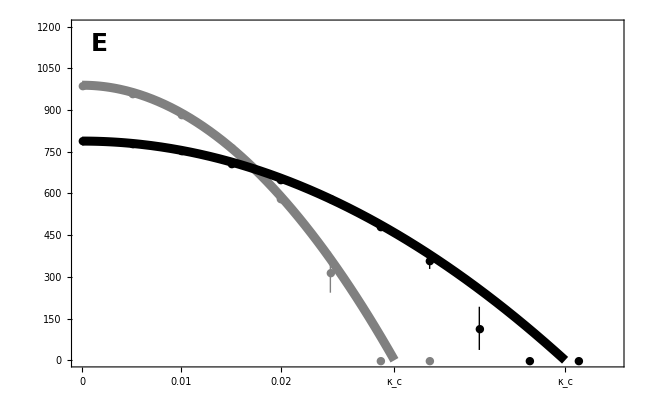

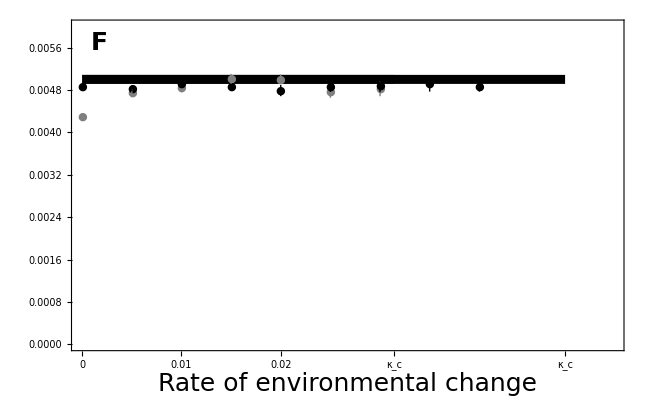

```mathematica
(*plotting colors*)
col1=Gray;
col2=Black;

(*simulation results*)
simdir=datadir<>"PUSH/CEQUALS0/Summary/";
simdir2=datadir<>"PUSHB/Summary/";
summdata=Import[simdir<>"summdata.dat"];
summdata2=Import[simdir2<>"summdata.dat"];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;
γk=1;
 
(*equilibrium variance*)
Vz=2 α^2;

(*two consumption rates to compare*)
c0=0;
c1=2;

(*x-axis limit*)
xmax=1.1*κ/.kc[[1]]/.k->c1;
(*x-axis ticks*)
xnum=5;
xticks={0,0.01,0.02,{κ/.kc[[1]]/.k->c0,Style["κ_c",col1,FontSize->LabelSize]},{κ/.kc[[1]]/.k->c1,Style["κ_c",col2,FontSize->LabelSize]}};
(*max number of simulations to show*)
numsims=7;
numsims2=9;

Legended[
Show[{
(*predicted lag*)
Plot[L/.Leq/.k->c0,{κ,0,κ/.kc[[1]]/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}, Axes->False],
Plot[L/.Leq/.k->c1,{κ,0,κ/.kc[[1]]/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->All],
(*observed lag +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[2]][[i]]},ErrorBar[1.96*summdata[[4]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[2]][[i]]},ErrorBar[1.96*summdata2[[4]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},All},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{All,All},{xticks,All}},
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.35]]
},
{
Style["Without predation",LabelSize,Bold,Gray]
}
],
{0.2,1}
] 
]

Export[imagedir<>"SelectiveGeneralistEquilibriumLag.eps",%];

Show[{
(*predicted density*)
Plot[N/.Neq/.Leq/.k->c0,{κ,0,κ/.kc[[1]]/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[N/.Neq/.Leq/.k->c1,{κ,0,κ/.kc[[1]]/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
(*observed density +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[5]][[i]]},ErrorBar[1.96*summdata[[7]][[i]]]},{i,1,Dimensions[summdata][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[5]][[i]]},ErrorBar[1.96*summdata2[[7]][[i]]]},{i,1,Dimensions[summdata2][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},{0,Rtot*1.2}},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[imagedir<>"SelectiveGeneralistEquilibriumDensity.eps",%];

(*Legended[*)
Show[{
(*predicted variance*)
Plot[Vz,{κ,0,κ/.kc[[1]]/.k->c0},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,κ/.kc[[1]]/.k->c1},PlotStyle->{col2,Thickness[0.01]}],
(*observed variance +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[8]][[i]]},ErrorBar[1.96*summdata[[10]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1,Axes->False],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[8]][[i]]},ErrorBar[1.96*summdata2[[10]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2,Axes->False]
},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,0.006}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Rate of environmental change",LabelSize],Scaled@xlabpos]
},
PlotRangeClipping->False
](*,
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]*)
(*,
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]*)

Export[imagedir<>"SelectiveGeneralistEquilibriumVariance.eps",%];

Clear[simdir,simdir2,summdata,summdata2,bmax,mmin,Rtot,γ,γk,α,Vz,xmax,xticks,numsims,numsims2,c0,c1,xnum,col1,col2]
```

### Lande-esque figure

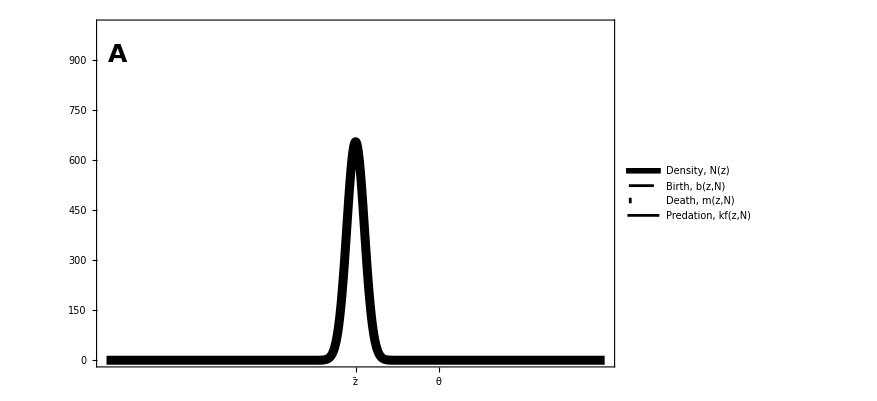
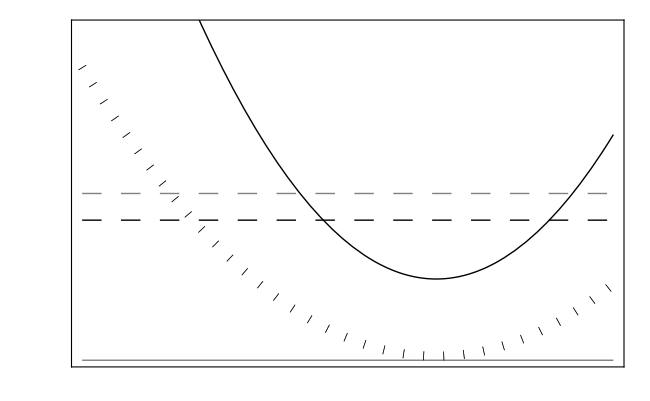
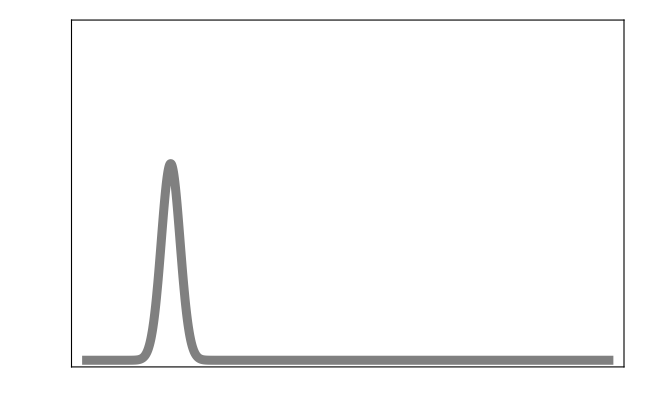

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;Vz=2 α^2 ;
γk=1;k=2;
κ=2/100;θ=10;

barz=θ-L/.Leq;

zmin=θ-4*L/.Leq;
(*zmin=0;*)
zmax=θ+2*L/.Leq;
(*zmax=θ;*)
ymax=Rtot;

xticks={{barz,Style["z̄",FontSize->LabelSize]},{θ,Style["θ",FontSize->LabelSize]}};
(*xticks=Automatic;*)

p1=
Legended[
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Thickness[0.01]},PlotRange->{Automatic,ymax},Axes->False],
PlotRange->{0,ymax},
Frame -> True, 
FrameLabel -> {Style[(*"Phenotype"*)"",LabelSize],Style[(*"Prey density"*)"",LabelSize]}, 
FrameTicks->{{All,None},{xticks,All}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize,
PlotRangeClipping->False,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@{0.04,0.9}],
Rotate[Text[Style["Prey density",LabelSize],Scaled@ylabpos],90 Degree],
Rotate[Text[Style["Per capita rate",LabelSize],Scaled@{1.1,0.5}],90 Degree]
}
],
Placed[
LineLegend[{
Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]],
Directive[Thickness[0.2],Black,Dashing[{0,Medium}]],
Directive[Thickness[0.1],Black]
},
{
Style["Density, N(z)",LabelSize],
Style["Birth, b(z,N)",LabelSize],
Style["Death, m(z,N)",LabelSize],
Style["Predation, kf(z,N)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.75}
] 
];

p2=Show[
k=0;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Dashing[Large],Thick},Axes->False],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Gray,Dashing[{0,Large}],Thickness[0.01]}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Gray,Thick}],
k=2;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Dashing[Large],Thick}],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Black,Dashing[{0,Large}],Thickness[0.01]}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Black,Thick}],
Frame -> True, 
FrameLabel -> {,,,Style[(*"Per capita rate"*)"",LabelSize]}, 
FrameTicks->{{None,All},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

k=0;
barz=θ-L/.Leq;
p3=
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{Automatic,ymax},Axes->False],
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{None,None},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

Overlay[{p1,p2,p3}]

Export[imagedir<>"LandePush.eps",%];

Clear[bmax,mmin,Rtot,γ,α,Vz,γk,θ,barz,σz,θ,xticks,zmax,ymax,n,k,κ,zmin]
```

## Generalist example 1B: selective push (predate those with smallest trait values more)

### Model set-up

Let the relative mortality rate m of an individual be a quadratic function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and minimum death rate mmin

```mathematica
m[z_,N_]:=mmin+γ(θ-z)^2
```

where N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

The population mean per capita mortality rate is then

```mathematica
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

mmin+γ (Vz+(barz-θ)^2)

Let k * f[z,N] be the per capita rate of consumption of prey with trait value z by predators, with

```mathematica
f[z_,N_]:=Exp[-γk (z-barz)]
```

where k is the overall predation intensity and γk describes how quickly predator preference decays with increasing prey trait value.

The population mean per capita predation rate is then

```mathematica
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γk>0}]//FullSimplify
```

ⅇ^((Vz γk^2)/2) k

Finally we let the per capita birth rate be

```mathematica
b[z_,N_]:=bmax (Rtot-N)
```

where Rtot is the total amount of resources in the (closed) system and bmax is the maximum birth rate, achieved when all resources are available (ie, no resources contained in prey).

Mean growth rate is

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}]//FullSimplify
```

bmax (-N+Rtot)

Then the growth rate of a population of N individuals with trait value z is

```mathematica
dNdtz=N(b[z,N]-m[z,N]-k f[z,N])
```

N (-ⅇ^(-(-barz+z) γk) k-mmin+bmax (-N+Rtot)-γ (-z+θ)^2)

Integrating over all individuals, the population mean growth rate dN/dt is

```mathematica
dNdt=Integrate[dNdtz p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0,γk>0}]//FullSimplify
```

-N (ⅇ^((Vz γk^2)/2) k+mmin+bmax (N-Rtot)+γ (Vz+(barz-θ)^2))

### Rate of evolution and equilibrium phenotypic variance

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born in a population that previously had mean trait value barz and density N, the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes (assuming a normal phenotype distribution with mean barz and variance Vz)

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

Given a prey individual is chosen to give birth, the probability it has trait value zP is

```mathematica
pzbirth=(b[zP,N]p[zP])/barb;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zP]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zP, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zP,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected trait mean after a selective birth is then

```mathematica
meanafterbirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected trait variance after a selective birth is

```mathematica
varafterbirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Death

PREY DEATH

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

The probability an individual with trait value zD dies is

```mathematica
pzdeath=(m[zD,N]p[zD])/barm;
```

After death the expected trait mean is

```mathematica
meanafterdeath=Simplify[Integrate[Factor[meand*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

After death the expected variance is

```mathematica
varafterdeath=Simplify[Integrate[Factor[vard*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

PREDATION

Given an individual is consumed by a predator, the probability it has trait value zC is

```mathematica
pzpred=(k f[zC,N]p[zC])/barkf;
```

After predation the expected trait mean is

```mathematica
meanafterpred=Simplify[Integrate[Factor[meand*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

After predation the expected variance is

```mathematica
varafterpred=Simplify[Integrate[Factor[vard*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Rate of evolution

Using the law of total probability, the expected mean trait after a small time Δt is

```mathematica
Ebarzdt=(1-Δt N(barb+barm+barkf))barz+Δt N(barb* meanafterbirth+barm* meanafterdeath+barkf*meanafterpred);
```

The rate of change in the mean trait value is thus

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp=FullSimplify[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,Vz>0]
```

Vz (-2 barz γ+ⅇ^((Vz γk^2)/2) k γk+2 γ θ)

#### Equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+barkf))Vz+Δt N(barb *varafterbirth+ barm *varafterdeath+ barkf *varafterdeath);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1;
```

When the random effect is small (and therefore the variance is also small) we have, at equilibrium, approximately

```mathematica
Normal[Series[dVdtApp/.Vz->ϵ Vz/.α->α ϵ^(1/2),{ϵ,0,1}]]/.ϵ->1;
Veq=Solve[%==0,Vz]//FullSimplify
```

{{Vz→(2 (-2+N-Rtot) α^2)/(N-Rtot)}}

And when the amount of available resources R = Rtot-N is large (much greater than 2), this is approximately

```mathematica
VzEqApp=Normal[Series[Vz/.Veq/.N->Rtot-R/ϵ,{ϵ,0,0}]]
```

{2 α^2}

### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[dNdt/N==0/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→-(ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+(L^2+Vz) γ)/bmax}

When the optimum changes at rate κ, and density remains at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarzdtApp==κ/.Neq/.θ->L+barz,{L}][[1]]//FullSimplify
```

{L→(-ⅇ^((Vz γk^2)/2) k Vz γk+κ)/(2 Vz γ)}

The fastest rate of environmental change that the population can persist at is less than the rate that causes density to go to zero. This critical rate is

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ];
```

How does this critical rate change with predation intensity?

```mathematica
D[κ/.kc[[2]],k]//Simplify
```

ⅇ^((Vz γk^2)/2) Vz (-(Vz γ)/(√(-Vz^2 γ (ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+Vz γ)))+γk)

This derivative shows that when the term in the brackets is positive, increasing predation increases the prey’s critical rate of environmental change.

Demonstration that the critical rate of environmental change can increase with increasing predation (over some range of k):

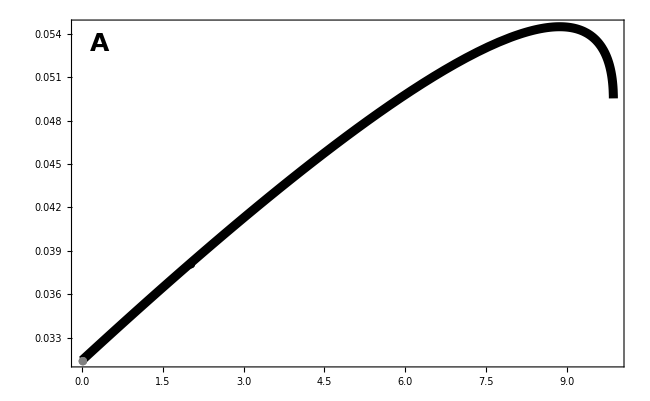

```mathematica
Show[
Plot[κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1,{k,0,10},PlotStyle->{Thickness[0.01],Black},PlotRange->{-0.1,All}],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}},PlotStyle->Blue,PlotMarkers->{Automatic,Large}],
ListPlot[{{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}},PlotStyle->Brown,PlotMarkers->{Automatic,Large}],*)
ListPlot[{{0,κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->0}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{2,κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->2}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
PlotRange->{0,All},
Frame->True, 
FrameLabel->{Style[(*"Predation intensity"*)"",LabelSize],Style[(*"Critical rate"*)"",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Critical rate",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

Export[imagedir<>"SelectiveGeneralistCriticalRatePredation.eps",%];
```

```mathematica
Show[
Plot[κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1,{k,0,10},PlotStyle->{Thickness[0.01],Black},PlotRange->{-0.1,All},WorkingPrecision->1000],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}},PlotStyle->Blue,PlotMarkers->{Automatic,Large}],
ListPlot[{{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}},PlotStyle->Brown,PlotMarkers->{Automatic,Large}],*)
ListPlot[{{0,κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->0}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{2,κ/.kc[[2]]/.Rtot->1000/.bmax->1/100/.mmin->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.γk->1/.k->2}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
PlotRange->{0,All},
Frame->True, 
FrameLabel->{Style[(*"Predation intensity"*)"",LabelSize],Style[(*"Critical rate"*)"",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Critical rate",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

Export[imagedir<>"SelectiveGeneralistCriticalRatePredation.eps",%];
```

-Graphics-

### Applying the general analysis

```mathematica
dNdt=-N (ⅇ^((Vz γk^2)/2) k+mmin+bmax (N-Rtot)+γ (Vz+(barz-θ)^2));
dzdtApp=Vz (-2 barz γ+ⅇ^((Vz γk^2)/2) k γk+2 γ θ);
```

The per capita growth rate

```mathematica
g[N_,barz_,k_]:=dNdt/N//Evaluate
```

The rate of evolution is approximately (in this case we need a better approximation than that given by Lande’s equation)

```mathematica
dzdt=VA dzdtApp/Vz
```

VA (-2 barz γ+ⅇ^((Vz γk^2)/2) k γk+2 γ θ)

This does not depend on N, but the direct selective effect of predation satisfies Equation 3

```mathematica
eq3=D[dzdt,k]
```

ⅇ^((Vz γk^2)/2) VA γk

The equilibrium population density as a function of trait value

```mathematica
nhat=Solve[g[N,barz,k]==0,N]//Flatten//Simplify
```

{N→-(ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+barz^2 γ+Vz γ-2 barz γ θ+γ θ^2)/bmax}

The critical lag (that which causes population density to go to zero)

```mathematica
critlag=Solve[0==N/.nhat/.barz->barzc,barzc][[1]]
```

{barzc→(-√(-ⅇ^((Vz γk^2)/2) k γ-mmin γ+bmax Rtot γ-Vz γ^2)+γ θ)/γ}

The strength of selection at the critical rate

```mathematica
h=dzdt/.N->0/.barz->barzc
```

VA (-2 barzc γ+ⅇ^((Vz γk^2)/2) k γk+2 γ θ)

The terms in Equation 5 (first line)

```mathematica
{D[h,k],D[h,barzc],D[barzc/.critlag,k]}/.critlag//FullSimplify
```

{ⅇ^((Vz γk^2)/2) VA γk,-2 VA γ,(ⅇ^((Vz γk^2)/2))/(2 √(-γ (ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+Vz γ)))}

Equation 5 (first line)

```mathematica
eq5=VA(D[h,k]+D[h,barzc]D[barzc/.critlag,k])/.critlag//FullSimplify
```

ⅇ^((Vz γk^2)/2) VA^2 (-γ/(√(-γ (ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+Vz γ)))+γk)

Equation 5 is positive when k is less than

```mathematica
Solve[-γ/(√(-γ (ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+Vz γ)))+γk==0,k]//Flatten
```

{k→-(ⅇ^(-(Vz γk^2)/2) (γ+mmin γk^2-bmax Rtot γk^2+Vz γ γk^2))/γk^2}

Check that this is the same as directly differentiating the critical rate

```mathematica
Solve[κ==dzdt,barz]//Flatten//Simplify;
Solve[0==N/.nhat/.%,κ][[2]]//Simplify;
D[κ/.%,k]//Simplify
```

ⅇ^((Vz γk^2)/2) VA (-(VA γ)/(√(-VA^2 γ (ⅇ^((Vz γk^2)/2) k+mmin-bmax Rtot+Vz γ)))+γk)

### Temporal dynamics (with simulation results)

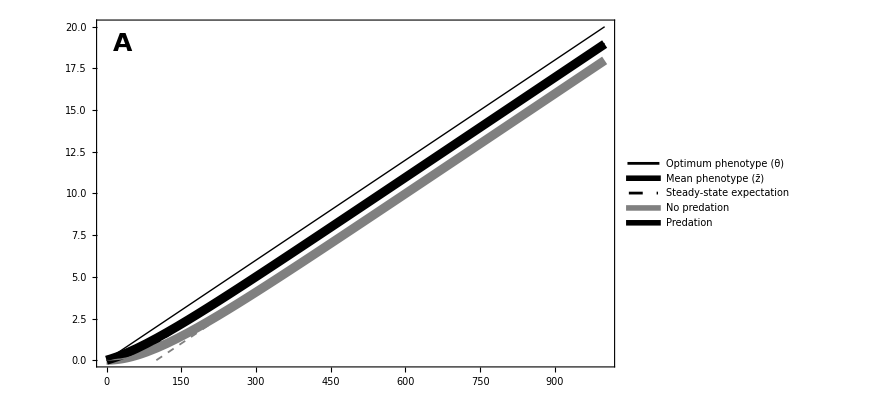

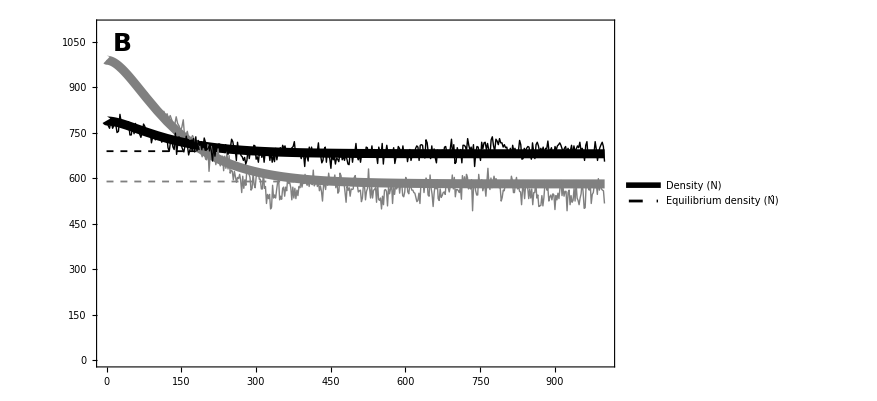

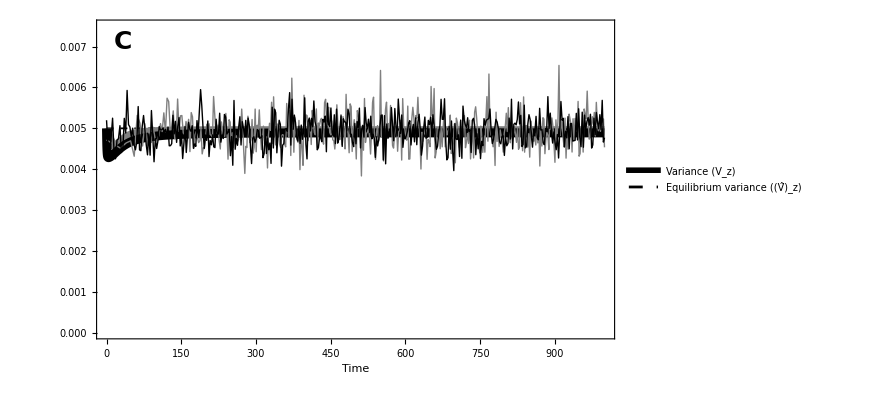

```mathematica
(*predation rates to compare*)
numlines=2;
Table[c[i]=(i-1)*2,{i,1,numlines}];

(*plotting colors*)
Table[col[i]=GrayLevel[1-i/numlines],{i,1,numlines}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;
γk=1;
tmax=1000;
κ =2/100;

(*initial values*)
n0=Rtot-(mmin+k)/bmax;z0=0;Vz0=VzEqApp[[1]];

(*numerically solve coupled equation*)
Table[
sol[i]=NDSolve[{
n'[t]==(dNdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
z'[t]==(dbarzdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
Vz'[t]==(dVdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
n[0]==n0,
z[0]==z0,
Vz[0]==Vz0
}/.k->c[i],{n,z,Vz},{t,0,tmax},MaxSteps->30000],
{i,1,numlines}];

(*simulation results*)
simdir[1]=datadir<>"PUSH/CEQUALS0/k0pt02/";
simdir[2]=datadir<>"PUSH/CEQUALS2/k0pt02/";
rep="1";
Table[zpdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,numlines}];
Table[Pdat[i]= Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,numlines}];

(*plot trait dynamics*)
Legended[
Show[
Plot[κ t,{t,0,tmax},PlotStyle->{Black,Thick}],(*optimal*)
Table[Plot[κ t-L/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed},PlotRange->{0,All}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[z[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,numlines}],(*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,1]]},{j,1,Dimensions[Pdat[i]][[1]],1}],PlotRange->All,PlotStyle->col[i], Joined->True],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,All}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
{Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Optimum phenotype (θ)",LabelSize],
Style["Mean phenotype (z̄)",LabelSize],
Style["Steady-state expectation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.75}
] ,
Placed[
LineLegend[{
Directive[Gray,Thickness[0.25]],
Directive[Black,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] }
]

(*Export[imagedir<>"SelectiveGeneralistTemporalTrait.eps",%];*)

(*plot density dynamics*)
Legended[
Show[
Table[Plot[N/.Neq/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,Rtot*1.01}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[Pdat[i][[j]],{j,1,Dimensions[Pdat[i]][[1]],1}],Joined->True,PlotStyle->col[i]],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,Rtot*1.1}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Density (N)",LabelSize],
Style["Equilibrium density (N̂)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

(*Export[imagedir<>"SelectiveGeneralistTemporalDensity.eps",%];*)

(*plot variance dynamics*)
Legended[
Show[
Plot[VzEqApp,{t,0,tmax},PlotStyle->{Black,Thickness[0.002],Dashed}],(*equilibrium*)
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,All}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,2]]},{j,1,Dimensions[Pdat[i]][[1]],1}],PlotStyle->col[i],Joined->True],{i,1,numlines}], (*simulation*)
Frame->True, 
FrameLabel->{Style["Time",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,tmax},{0,VzEqApp[[1]]*1.5}},
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Variance (V_z)",LabelSize],
Style["Equilibrium variance ((V̂)_z)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.3}
]
]

(*Export[imagedir<>"SelectiveGeneralistTemporalVariance.eps",%];*)

Clear[numlines,c,col,bmax,mmin,Rtot,γ,γk,α,tmax,z0,n0,Vz0,κ,sol,simdir,rep,zpdat,Pdat]
```

### Equilibrium dynamics (with simulation results)

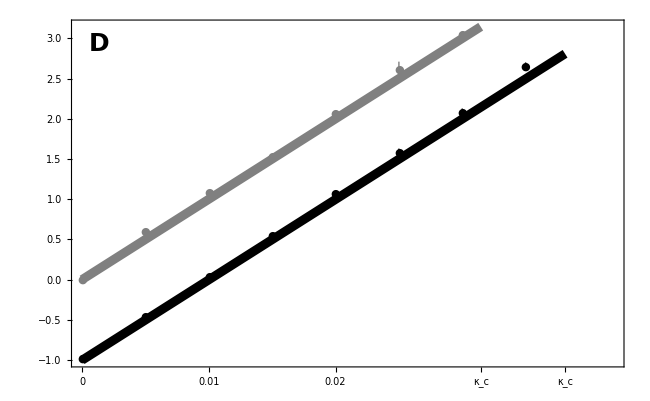

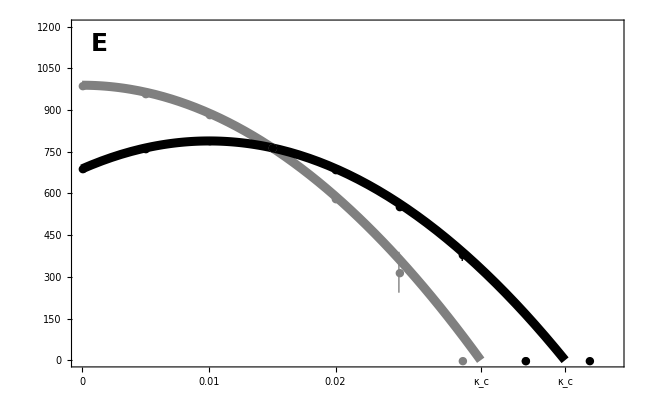

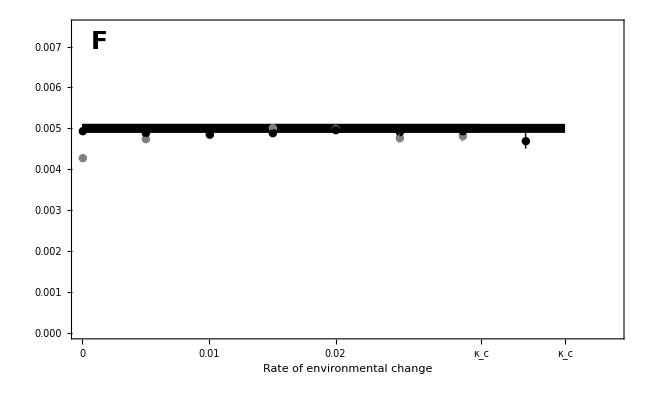

```mathematica
(*plotting colors*)
col1=Gray;
col2=Black;

(*simulation results*)
simdir=datadir<>"PUSH/CEQUALS0/Summary/";
simdir2=datadir<>"PUSH/CEQUALS2/Summary/";
summdata=Import[simdir<>"summdata.dat"];
summdata2=Import[simdir2<>"summdata.dat"];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;
γk=1;
 
(*equilibrium variance*)
Vz=2 α^2;

(*two consumption rates to compare*)
c0=0;
c1=2;

(*x-axis limit*)
xmax=1.1*κ/.kc[[2]]/.k->c1;
(*x-axis ticks*)
xnum=5;
xticks={0,0.01,0.02,{κ/.kc[[2]]/.k->c0,Style["κ_c",col1,FontSize->TickSize]},{κ/.kc[[2]]/.k->c1,Style["κ_c",col2,FontSize->TickSize]}};
(*max number of simulations to show*)
numsims=7;
numsims2=8;

Show[{
(*predicted lag*)
Plot[L/.Leq/.k->c0,{κ,0,κ/.kc[[2]]/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}, Axes->False],
Plot[L/.Leq/.k->c1,{κ,0,κ/.kc[[2]]/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->All],
(*observed lag +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[2]][[i]]},ErrorBar[1.96*summdata[[4]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[2]][[i]]},ErrorBar[1.96*summdata2[[4]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},All},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{All,All},{xticks,All}},
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumLag.eps",%];*)

Show[{
(*predicted density*)
Plot[N/.Neq/.Leq/.k->c0,{κ,0,κ/.kc[[2]]/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[N/.Neq/.Leq/.k->c1,{κ,0,κ/.kc[[2]]/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
(*observed density +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[5]][[i]]},ErrorBar[1.96*summdata[[7]][[i]]]},{i,1,Dimensions[summdata][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[5]][[i]]},ErrorBar[1.96*summdata2[[7]][[i]]]},{i,1,Dimensions[summdata2][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},{0,Rtot*1.2}},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumDensity.eps",%];*)

(*Legended[*)
Show[{
(*predicted variance*)
Plot[Vz,{κ,0,κ/.kc[[2]]/.k->c0},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,κ/.kc[[2]]/.k->c1},PlotStyle->{col2,Thickness[0.01]}],
(*observed variance +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[8]][[i]]},ErrorBar[1.96*summdata[[10]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1,Axes->False],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[8]][[i]]},ErrorBar[1.96*summdata2[[10]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2,Axes->False]
},
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,Vz*1.5}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]*)

(*Export[imagedir<>"SelectiveGeneralistEquilibriumVariance.eps",%];*)

Clear[simdir,simdir2,summdata,summdata2,bmax,mmin,Rtot,γ,γk,α,Vz,xmax,xticks,numsims,numsims2,c0,c1,xnum,col1,col2]
```

### Lande-esque figure

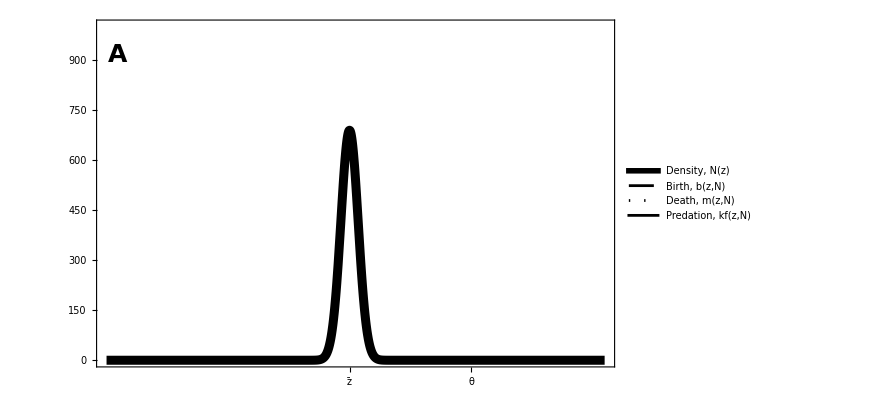
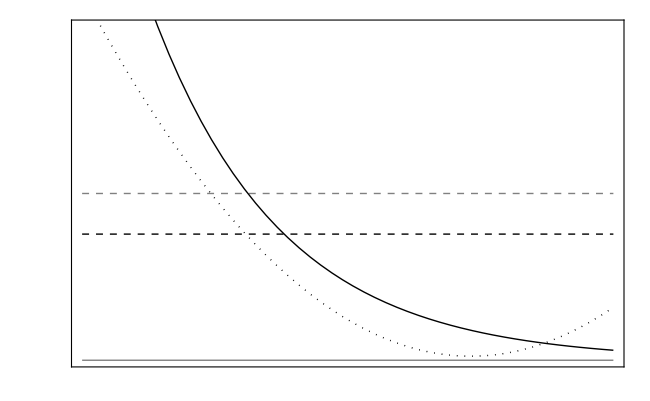
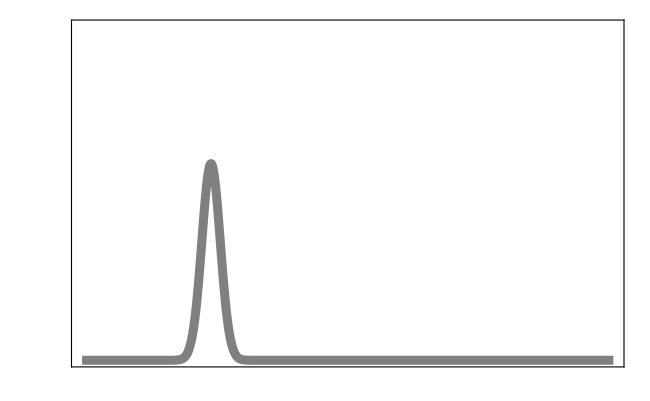

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1;α=1/20;Vz=2 α^2 ;
γk=1;k=2;
κ=2/100;θ=10;

barz=θ-L/.Leq;

zmin=θ-3*L/.Leq;
(*zmin=0;*)
zmax=θ+1.1*L/.Leq;
(*zmax=θ;*)
ymax=Rtot;

xticks={{barz,Style["z̄",FontSize->LabelSize]},{θ,Style["θ",FontSize->LabelSize]}};
(*xticks=Automatic;*)

p1=
Legended[
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Thickness[0.01]},PlotRange->{Automatic,ymax},Axes->False],
PlotRange->{0,ymax},
Frame -> True, 
FrameLabel -> {Style[(*"Phenotype"*)"",LabelSize],Style[(*"Prey density"*)"",LabelSize]}, 
FrameTicks->{{All,None},{xticks,All}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize,
PlotRangeClipping->False,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@{0.04,0.9}],
Rotate[Text[Style["Prey density",LabelSize],Scaled@ylabpos],90 Degree],
Rotate[Text[Style["Per capita rate",LabelSize],Scaled@{1.1,0.5}],90 Degree]
}
],
Placed[
LineLegend[{
Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]],
Directive[Thickness[0.1],Black,Dotted],
Directive[Thickness[0.1],Black]
},
{
Style["Density, N(z)",LabelSize],
Style["Birth, b(z,N)",LabelSize],
Style["Death, m(z,N)",LabelSize],
Style["Predation, kf(z,N)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.75}
] 
];

p2=Show[
k=0;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Dashed,Thick}],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Gray,Dotted,Thick}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Gray,Thick}],
k=2;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Dashed,Thick}],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Black,Dotted,Thick}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Black,Thick}],
Frame -> True, 
FrameLabel -> {,,,Style[(*"Per capita rate"*)"",LabelSize]}, 
FrameTicks->{{None,All},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

k=0;
barz=θ-L/.Leq;
p3=
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,ymax}],
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{None,None},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

Overlay[{p1,p2,p3}]

(*Export[imagedir<>"LandePush.eps",%];*)

Clear[bmax,mmin,Rtot,γ,α,Vz,γk,θ,barz,σz,θ,xticks,zmax,ymax,n,k,κ,zmin]
```

## Generalist example 2A: evolutionary hydra effect (continuous breeding)

### Model set-up

Let the per capita birth rate of an individual b be a Gaussian function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and maximum per available resource birth rate bmax

```mathematica
b[z_,N_]:=bmax Exp[-γ/2 (θ-z)^2](Rtot-N)
```

where Rtot is the total density of resources in the system and N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

The mean per capita birth rate is then

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N+Rtot))/(√(1+Vz γ))

We assume constant, equal per capita mortality and predation

```mathematica
m[z_,N_]:=mconst
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
f[z_,N_]:=1
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
```

Then the growth rate of a population composed of N individuals with trait value z is

```mathematica
dNdtz=N(b[z,N]-m[z,N]-k f[z,N])
```

N (-k-mconst+bmax ⅇ^(-1/2 γ (-z+θ)^2) (-N+Rtot))

Integrating over all trait values, the population mean growth rate dN/dt is

```mathematica
dNdt=Integrate[dNdtz p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

(ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (-ⅇ^((γ (barz-θ)^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax (-N+Rtot) √(Vz/(1+Vz γ))))/(√Vz)

### Rate of evolution and equilibrium phenotypic variance

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born in a population that previously had mean trait value barz and density N, the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes (assuming a normal phenotype distribution with mean barz and variance Vz)

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

Given a prey individual is chosen to give birth, the probability it has trait value zP is

```mathematica
pzbirth=(b[zP,N]p[zP])/barb;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zP]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zP, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zP,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected trait mean after a selective birth is then

```mathematica
meanafterbirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected trait variance after a selective birth is

```mathematica
varafterbirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Death

PREY DEATH

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

The probability an individual with trait value zD dies is

```mathematica
pzdeath=(m[zD,N]p[zD])/barm;
```

After death the expected trait mean is

```mathematica
meanafterdeath=Simplify[Integrate[Factor[meand*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

After death the expected variance is

```mathematica
varafterdeath=Simplify[Integrate[Factor[vard*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

PREDATION

Given an individual is consumed by a predator, the probability it has trait value zC is

```mathematica
pzpred=(k f[zC,N]p[zC])/barkf;
```

After predation the expected trait mean is

```mathematica
meanafterpred=Simplify[Integrate[Factor[meand*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

After predation the expected variance is

```mathematica
varafterpred=Simplify[Integrate[Factor[vard*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Rate of evolution

Using the law of total probability, the expected mean trait after a small time Δt is

```mathematica
Ebarzdt=(1-Δt N(barb+barm+barkf))barz+Δt N(barb* meanafterbirth+barm* meanafterdeath+barkf*meanafterpred);
```

The rate of change in the mean trait value is thus

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp0=FullSimplify[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,Vz>0]
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+N-Rtot) Vz γ (barz-θ))/(2 (1+Vz γ)^(3/2))

And when the amount of available resources R = Rtot - N is much bigger than one we have

```mathematica
dbarzdtApp=Normal[Series[dbarzdtApp0/.N->Rtot-R/ϵ,{ϵ,0,-1}]//FullSimplify]/.ϵ->1/.R->Rtot-N
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N+Rtot) Vz γ (-barz+θ))/(2 (1+Vz γ)^(3/2))

#### Equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+barkf))Vz+Δt N(barb *varafterbirth+ barm *varafterdeath+ barkf *varafterdeath);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1;
```

When the random effect is small (and therefore the variance is also small) we have, at equilibrium, approximately

```mathematica
Normal[Series[dVdtApp/.Vz->ϵ Vz/.α->α ϵ^(1/2),{ϵ,0,1}]]/.ϵ->1;
Veq=Solve[%==0,Vz]//FullSimplify
```

{{Vz→(2 (-2+N-Rtot) α^2)/(N-Rtot)}}

And when the amount of available resources R = Rtot-N is large (much greater than 2), this is approximately

```mathematica
VzEqApp=Normal[Series[Vz/.Veq/.N->Rtot-R/ϵ,{ϵ,0,0}]]
```

{2 α^2}

### Quick [can run instead of sections above if model unchanged]

```mathematica
dNdt=(ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (-ⅇ^((γ (barz-θ)^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax (-N+Rtot) √(Vz/(1+Vz γ))))/(√Vz);
```

```mathematica
dbarzdt=(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (N-Rtot) Vz γ (barz-θ))/(2 (1+N) (1+Vz γ)^(3/2));
```

```mathematica
dbarzdtApp=(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N+Rtot) Vz γ (-barz+θ))/(2 (1+Vz γ)^(3/2));
```

```mathematica
dVdt=1/(4 (-1+N^2)^2 (1+Vz γ)^(5/2))ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (-4 ⅇ^((γ (barz-θ)^2)/(2+2 Vz γ)) (k+mconst) (1+N)^2 Vz (1+Vz γ)^(5/2)+bmax (-1+N)^2 (N-Rtot) (-4 N α^2+(4+3 N) Vz^3 γ^2+Vz (4+N (2-8 α^2 γ))-Vz^2 γ (-8+N (-5+barz^2 γ+4 α^2 γ-2 barz γ θ+γ θ^2))));
```

### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[dNdt/N==0/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→(-ⅇ^((L^2 γ)/(2+2 Vz γ)) (k+mconst) √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))}

When the optimum changes at rate κ, and density is at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarzdtApp==κ/.Neq/.θ->L+barz,L][[1]]//FullSimplify
```

{L→(2 √(Vz/(1+Vz γ)) (1+Vz γ)^(3/2) κ)/((k+mconst) Vz^(3/2) γ)}

The fastest rate of environmental change that the population can persist at is therefore less than

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ][[1]]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{κ→-(ⅈ (k+mconst) Vz √(γ Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(√(2+2 Vz γ))}

The critical rate of environmental change changes with predation like

```mathematica
D[κ/.kc,k]//Simplify
```

-(ⅈ Vz (γ+2 γ Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(2 √(2+2 Vz γ) √(γ Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))

And therefore the critical rate can increase with predation when k is small enough.

A numerical example to demonstrate this point:

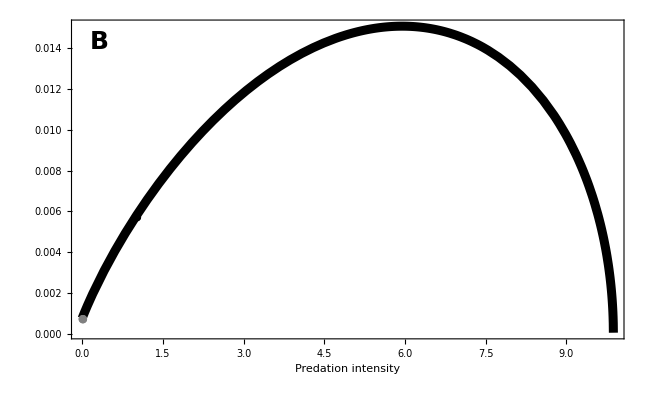

```mathematica
Show[
Plot[κ/.kc/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05,{k,0,10},PlotStyle->{Thickness[0.01],Black}],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
ListPlot[{{0,κ/.kc/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->0}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{1,κ/.kc/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->1}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],
PlotRange->{0,All},
Frame->True, 
FrameLabel->{Style["Predation intensity",LabelSize],Style[(*"Critical rate"*)"",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
(*FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},*)
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Critical rate",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

Export[imagedir<>"GeneralistCriticalRatePredation.eps",%];
```

### Applying the general analysis

The per capita growth rate

```mathematica
g[N_,barz_,k_]:=dNdt/N//Evaluate
```

The rate of evolution is approximately

```mathematica
dzdt=VA D[g[N,barz,k],barz]//Simplify
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (N-Rtot) VA γ (Vz/(1+Vz γ))^(3/2) (barz-θ))/Vz^(3/2)

This does not depend on k, but birth depends on both N and k such that Equation 3 is positive (here shown at equilibrium population size)

```mathematica
Solve[g[N,barz,k]==0,N]//Flatten;
dNdk=D[N/.%,k];
eq3=% D[dzdt,N]//FullSimplify
```

(VA γ (-barz+θ))/(1+Vz γ)

The equilibrium population density as a function of trait value

```mathematica
nhat=Solve[g[N,barz,k]==0,N]//Flatten//Simplify
```

{N→(-ⅇ^((γ (barz-θ)^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))}

The critical lag (that which causes population density to go to zero)

```mathematica
critlag=Solve[0==N/.nhat/.barz->barzc,barzc][[1]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{barzc→(γ θ-√2 √(-γ (1+Vz γ) Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/γ}

The strength of selection at the critical rate

```mathematica
h=D[g[N,barz,k],barz]/.N->0/.barz->barzc//Simplify
```

-(bmax ⅇ^(-(γ (barzc-θ)^2)/(2+2 Vz γ)) Rtot γ (Vz/(1+Vz γ))^(3/2) (barzc-θ))/Vz^(3/2)

The terms in Equation 5 (first line)

```mathematica
{D[h,k],D[h,barzc],D[barzc/.critlag,k]}/.critlag//FullSimplify
```

{0,-((k+mconst) γ (1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(1+Vz γ),(1+Vz γ)/(√2 (k+mconst) √(-γ (1+Vz γ) Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))}

Equation 5 (first line)

```mathematica
eq5=VA(D[h,k]+D[h,barzc]D[barzc/.critlag,k])/.critlag//FullSimplify
```

-(VA γ (1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(√2 √(-γ (1+Vz γ) Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))

Equation 5 is positive when

```mathematica
Reduce[0>1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]&&γ>0&&γk>0&&Vz>0&&Rtot>0&&bmax>0&&mconst>0&&k>0,k,Reals]
```

γk>0&&mconst>0&&Rtot>0&&bmax>(√ⅇ mconst)/Rtot&&γ>0&&0<Vz<(-ⅇ mconst^2+bmax^2 Rtot^2)/(ⅇ mconst^2 γ)&&0<k<-mconst+(√((bmax^2 Rtot^2)/(1+Vz γ)))/(√ⅇ)

The terms in Equation 5 (second line)

```mathematica
{D[D[g[0,barz,k],barz],k],D[D[g[0,barz,k],barz],barz],D[barzc/.critlag,k]}/.barz->barzc/.critlag//FullSimplify
```

{0,-((k+mconst) γ (1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(1+Vz γ),(1+Vz γ)/(√2 (k+mconst) √(-γ (1+Vz γ) Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))}

Equation 5 (second line)

```mathematica
VA(D[D[g[0,barz,k],barz],k]+D[D[g[0,barz,k],barz],barz]D[barzc/.critlag,k])/.barz->barzc/.critlag//FullSimplify
```

-(VA γ (1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(√2 √(-γ (1+Vz γ) Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))

Check that this is the same as directly differentiating the critical rate

```mathematica
Solve[κ==dzdt/.nhat,barz]//Flatten//Simplify;
Solve[0==N/.nhat/.%,κ][[2]]//Simplify;
D[κ/.%,k]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅈ VA √γ (1+2 Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))]))/(√(2+2 Vz γ) √Log[((k+mconst) √Vz)/(bmax Rtot √(Vz/(1+Vz γ)))])

### Temporal dynamics (with simulation results)

-Graphics-

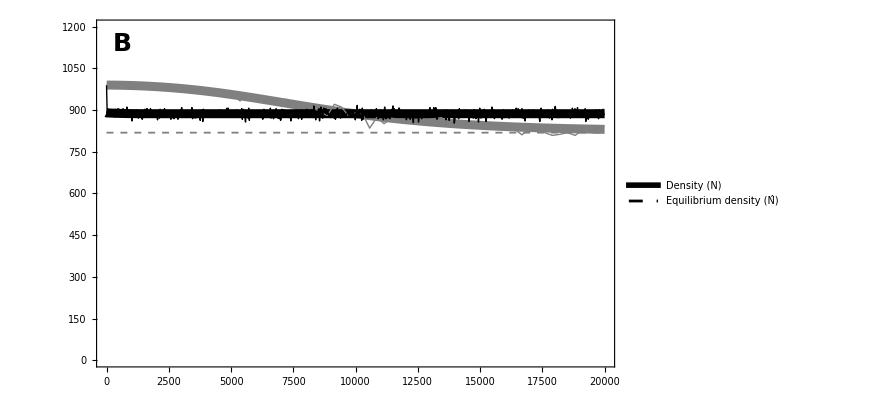

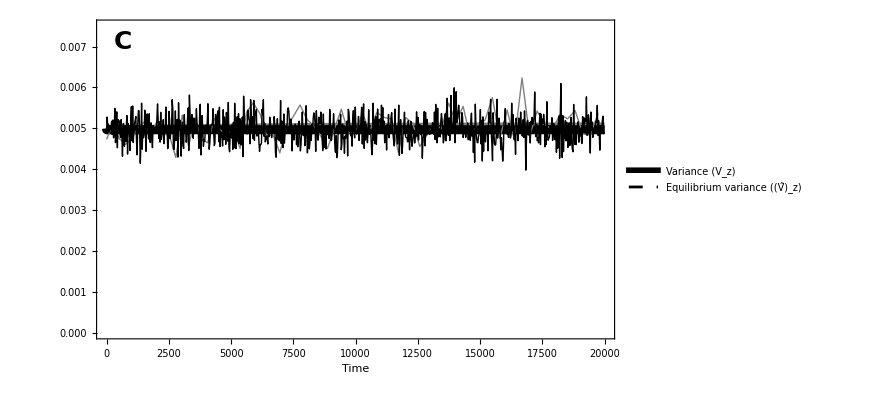

```mathematica
(*predation rates to compare*)
numlines=2;
Table[c[i]=(i-1)*1,{i,1,numlines}];

(*plotting colors*)
Table[col[i]=GrayLevel[1-i/numlines],{i,1,numlines}];

(*parameters*)
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1;α=1/20;
κ =6/10000;
tmax=20000;

(*initial values*)
n0=Rtot-(mconst+k)/bmax;;z0=0;Vz0=VzEqApp[[1]];

(*numerically solve coupled equation*)
Table[
sol[i]=NDSolve[{
n'[t]==(dNdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
z'[t]==(dbarzdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
Vz'[t]==(dVdt/.N->n[t]/.θ->κ t/.barz->z[t]/.Vz->Vz[t]),
n[0]==n0,
z[0]==z0,
Vz[0]==Vz0
}/.k->c[i],{n,z,Vz},{t,0,tmax},MaxSteps->30000],
{i,1,numlines}];

(*simulation results*)
simdir[1]=datadir<>"HYDRA/CEQUALS0/k0pt0006/";
simdir[2]=datadir<>"HYDRA/CEQUALS1/k0pt0006/";
rep="1";
Table[zpdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,numlines}];
Table[Pdat[i]= Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,numlines}];

(*plot trait dynamics*)
Legended[
Show[
Plot[κ t,{t,0,tmax},PlotStyle->{Black,Thick}],(*optimal*)
Table[Plot[κ t-L/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed},PlotRange->{0,All}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[z[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,numlines}],(*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,1]]},{j,1,Dimensions[Pdat[i]][[1]],1}],PlotRange->All,PlotStyle->col[i], Joined->True],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,All}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
{
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Optimum phenotype (θ)",LabelSize],
Style["Mean phenotype (z̄)",LabelSize],
Style["Steady-state expectation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
] (*,
Placed[
LineLegend[{
Directive[Black,Thickness[0.25]],
Directive[Gray,Thickness[0.25]]
},
{
Style["Predation",LabelSize],
Style["No predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.8,0.15}
] 
}
]*)
,
Placed[
LineLegend[{
Directive[Black,Thickness[0.35]]
},
{
Style["With predation",LabelSize,Bold]
}
],
{0.8,1}
] 
}
]

Export[imagedir<>"GeneralistTemporalTrait.eps",%];

(*plot density dynamics*)
Legended[
Show[
Table[Plot[N/.Neq/.Leq/.Vz->VzEqApp[[1]]/.k->c[i],{t,0,tmax},PlotStyle->{col[i],Thickness[0.002],Dashed}],{i,1,numlines}],(*analytical*)
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,Rtot*1.01}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[Pdat[i][[j]],{j,1,Dimensions[Pdat[i]][[1]],5}],Joined->True,PlotStyle->col[i]],{i,1,numlines}],(*simulation*)
PlotRange->{{0,tmax},{0,Rtot*1.2}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Density (N)",LabelSize],
Style["Equilibrium density (N̂)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.4}
]
]

Export[imagedir<>"GeneralistTemporalDensity.eps",%];

(*plot variance dynamics*)
Legended[
Show[
Plot[VzEqApp,{t,0,tmax},PlotStyle->{Black,Thickness[0.002],Dashed}],(*equilibrium*)
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,All}],{i,1,numlines}], (*numerical*)
Table[ListPlot[Table[{Pdat[i][[j,1]],zpdat[i][[j,2]]},{j,1,Dimensions[Pdat[i]][[1]],5}],PlotStyle->col[i],Joined->True],{i,1,numlines}], (*simulation*)
Frame->True, 
FrameLabel->{Style["Time",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,tmax},{0,VzEqApp[[1]]*1.5}},
PlotRangePadding->None,
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Variance (V_z)",LabelSize],
Style["Equilibrium variance ((V̂)_z)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.3}
]
]

Export[imagedir<>"GeneralistTemporalVariance.eps",%];

Clear[numlines,c,col,bmax,mmin,Rtot,γ,γk,α,tmax,z0,n0,Vz0,κ,sol,simdir,rep,zpdat,Pdat]
```

### Equilibrium dynamics (with simulation results)

-Graphics-

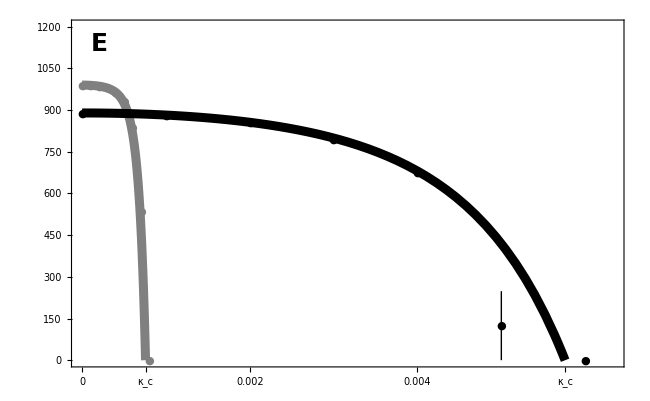

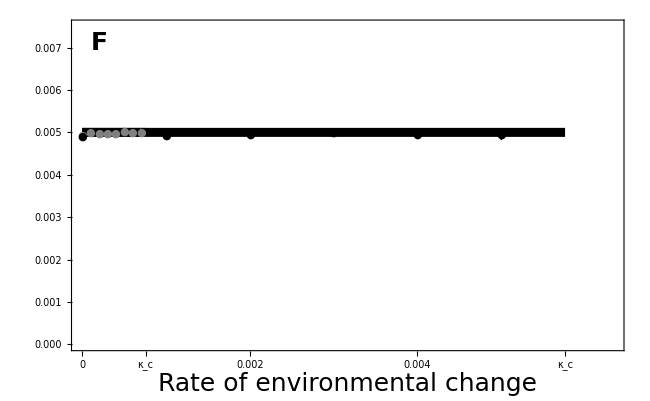

```mathematica
(*plotting colors*)
col1=Gray;
col2=Black;

(*simulation results*)
simdir=datadir<>"HYDRA/CEQUALS0/Summary/";
simdir2=datadir<>"HYDRA/CEQUALS1/Summary/";
summdata=Import[simdir<>"summdata.dat"];
summdata2=Import[simdir2<>"summdata.dat"];

(*parameters*)
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1;α=1/20;
 
(*equilibrium variance*)
Vz=2 α^2;

(*two predation rates to compare*)
c0=0;
c1=1;

(*x-axis limit*)
xmax=1.1*κ/.kc/.k->c1;
(*x-axis ticks*)
xnum=5;
xticks={0,0.002,0.004,{κ/.kc/.k->c0,Style["κ_c",col1,FontSize->LabelSize]},{κ/.kc/.k->c1,Style["κ_c",col2,FontSize->LabelSize]}};
(*max number of simulations to show*)
numsims=8;
numsims2=6;

Legended[
Show[{
(*predicted lag*)
Plot[L/.Leq/.k->c0,{κ,0,κ/.kc/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[L/.Leq/.k->c1,{κ,0,κ/.kc/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
(*observed lag +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[2]][[i]]},ErrorBar[1.96*summdata[[4]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[2]][[i]]},ErrorBar[1.96*summdata2[[4]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},All},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{All,All},{xticks,All}},
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.35]]
},
{
Style["Without predation",LabelSize,Bold,Gray]
}
],
{0.2,1}
] 
]

Export[imagedir<>"GeneralistEquilibriumLag.eps",%];

Show[{
(*predicted density*)
Plot[N/.Neq/.Leq/.k->c0,{κ,0,κ/.kc/.k->c0},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[N/.Neq/.Leq/.k->c1,{κ,0,κ/.kc/.k->c1},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
(*observed density +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[5]][[i]]},ErrorBar[1.96*summdata[[7]][[i]]]},{i,1,Dimensions[summdata][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[5]][[i]]},ErrorBar[1.96*summdata2[[7]][[i]]]},{i,1,Dimensions[summdata2][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2]
},
PlotRange->{{0,xmax},{0,Rtot*1.2}},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[imagedir<>"GeneralistEquilibriumDensity.eps",%];

(*Legended[*)
Show[{
(*predicted variance*)
Plot[Vz,{κ,0,κ/.kc/.k->c0},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,κ/.kc/.k->c1},PlotStyle->{col2,Thickness[0.01]}],
(*observed variance +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[8]][[i]]},ErrorBar[1.96*summdata[[10]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1,Axes->False],
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[8]][[i]]},ErrorBar[1.96*summdata2[[10]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2,Axes->False]
},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,1.5*Vz}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Rate of environmental change",LabelSize],Scaled@xlabpos]
},
PlotRangeClipping->False
](*,
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]*)

Export[imagedir<>"GeneralistEquilibriumVariance.eps",%];

Clear[simdir,summdata,summdata2,bmax,mconst,k,Rtot,γ,α,Vz,xmax,xticks,numsims,numsims2,c0,c1,xnum,col1,col2]
```

### Lande-esque figure

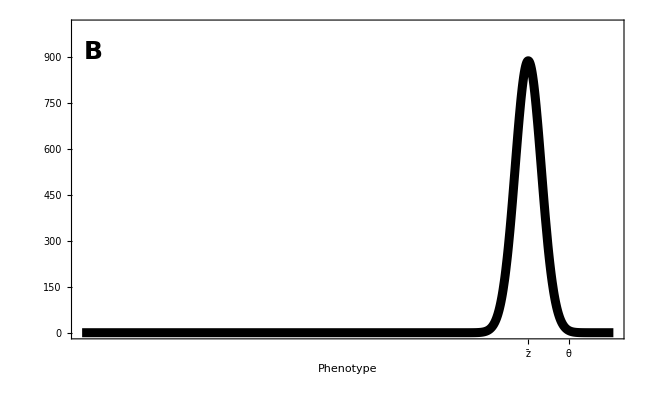
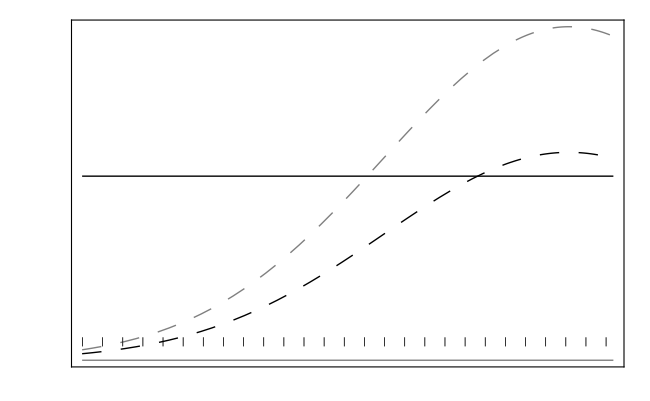
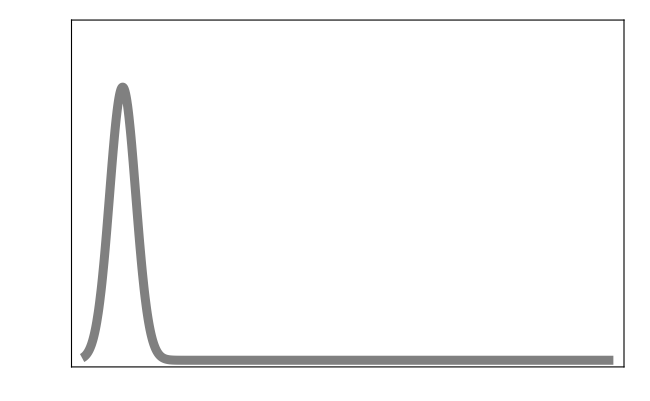

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1;α=1/20;Vz=2 α^2 ;
k=1;
κ=6/10000;θ=6;

barz=θ-L/.Leq;

zmin=θ-12*L/.Leq;
(*zmin=0;*)
zmax=θ+1.1*L/.Leq;
(*zmax=θ;*)
ymax=Rtot;

xticks={{barz,Style["z̄",FontSize->LabelSize]},{θ,Style["θ",FontSize->LabelSize]}};
(*xticks=Automatic;*)

p1=
(*Legended[*)
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Thickness[0.01]},PlotRange->{Automatic,ymax}],
PlotRange->{0,ymax},
Frame -> True, 
FrameLabel -> {Style["Phenotype",LabelSize],Style[(*"Prey density"*)"",LabelSize]}, 
FrameTicks->{{All,None},{xticks,All}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize,
PlotRangeClipping->False,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@{0.04,0.9}],
Rotate[Text[Style["Prey density",LabelSize],Scaled@ylabpos],90 Degree],
Rotate[Text[Style["Per capita rate",LabelSize],Scaled@{1.1,0.5}],90 Degree]
}
](*,
Placed[
LineLegend[{
Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]],
Directive[Thickness[0.1],Black,Dotted],
Directive[Thickness[0.1],Black]
},
{
Style["Density, N(z)",LabelSize],
Style["Birth, b(z,N)",LabelSize],
Style["Death, m(z,N)",LabelSize],
Style["Predation, kf(z,N)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.325,0.765}
] 
]*);

p2=Show[
k=0;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Dashing[Large],Thick}],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Gray,Dashing[{0,Large}],Thickness[0.01]}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Gray,Thick}],
k=1;
Plot[b[z,N]/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Black,Dashing[Large],Thick}],
Plot[m[z,N],{z,zmin,zmax},PlotStyle->{Black,Dashing[{0,Large}],Thickness[0.01]}],
Plot[k f[z,N],{z,zmin,zmax},PlotStyle->{Black,Thick}],
PlotRange->{0,All},
Frame -> True, 
FrameLabel -> {,,,Style[(*"Per capita rate"*)"",LabelSize]}, 
FrameTicks->{{None,All},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Black},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

k=0;
barz=θ-L/.Leq;
p3=
Show[
Plot[Sqrt[2π Vz]PDF[NormalDistribution[barz,Vz^(1/2)],z]*N/.Neq/.Leq,{z,zmin,zmax},PlotStyle->{Gray,Thickness[0.01]},PlotRange->{0,ymax}],
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{None,None},{None,None}},
ImagePadding->{{70,70},{70,10}},
FrameStyle->Directive[FontSize->TickSize],
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImageSize->FigureSize
];

Overlay[{p1,p2,p3}]

Export[imagedir<>"LandeHydra.eps",%];

Clear[bmax,mconst,Rtot,γ,α,Vz,θ,barz,σz,θ,xticks,zmax,ymax,n,k,κ,zmin]
```

### Eco-evolutionary cycles

```mathematica
(* approximate jacobian matrix *)
j:=D[{dNdt,κ-dbarzdtApp}/.θ->L+barz,{{N,L}}]
```

```mathematica
(* jacobian at equilibrium, J *)
jeq=FullSimplify[j/.Neq/.Leq]
```

{{k+mconst-(bmax ⅇ^(-(2 (1+Vz γ) κ^2)/((k+mconst)^2 Vz^2 γ)) Rtot √(Vz/(1+Vz γ)))/(√Vz),(2 √(1+Vz γ) (ⅇ^((2 (1+Vz γ) κ^2)/((k+mconst)^2 Vz^2 γ)) (k+mconst) √Vz-bmax Rtot √(Vz/(1+Vz γ))) κ)/(bmax Vz^(3/2))},{(bmax ⅇ^(-(2 (1+Vz γ) κ^2)/((k+mconst)^2 Vz^2 γ)) √(Vz/(1+Vz γ)) κ)/((k+mconst) √Vz),(√Vz (-(k+mconst)^2 Vz^2 γ+4 (1+Vz γ) κ^2))/(2 (k+mconst) (Vz/(1+Vz γ))^(3/2) (1+Vz γ)^(5/2))}}

Notice that with a relatively large phenotypic variance (Vz), corresponding to a large genetic variance in this model, unstable eco-evolutionary cycles can be expected to cause extinction before equilibrium popuation size goes to zero (blue line lower than red)

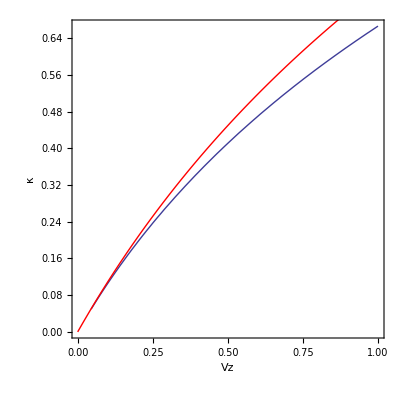

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
k=0.1;

Clear[Vz,κ]
Show[
ContourPlot[{Tr[jeq]==0(*,Det[jeq]==0*)}//Evaluate,{Vz,0.001,1},{κ,0,κ/.kc},FrameLabel->{"Vz","κ"}],
Plot[κ/.kc,{Vz,0,1},PlotStyle->Red]
]
Clear[bmax,Rtot,mconst,γ,Vz,k]
```

The unstable equilbirum shown in phase plane:

{κ→0.750241+0. ⅈ}

{{N→2.14054},{L→2.54545}}

{0.158161+0.239523 ⅈ,0.158161-0.239523 ⅈ}

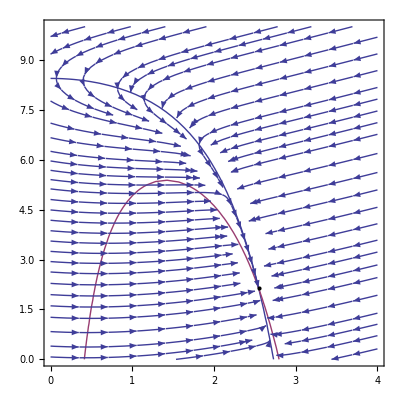

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=1;
k=0.1;

kc//N
κ=0.7;

{Neq/.Leq,Leq}
Eigenvalues[jeq]

Show[
ContourPlot[{dNdt/N==0,-κ+dbarzdtApp==0}/.N->n/.θ->L+barz//Evaluate,{L,0,4},{n,0,Rtot}],
StreamPlot[{dNdt/N,-κ+dbarzdtApp}/.N->n/.θ->L+barz,{L,0,4},{n,0,Rtot}],
Graphics[{PointSize[Medium],Point[{L,N}/.Neq/.Leq]}]
]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

A numerical example of stable eco-evolutionary cycles:

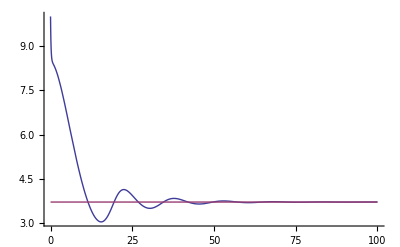

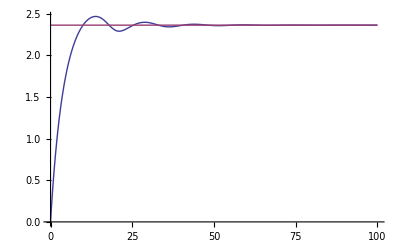

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=1;
k=0.1;
κ=0.65;
tmax=100;

sol=NDSolve[{
n'[t]==((ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) (-ⅇ^((γ l[t]^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax √(Vz/(1+Vz γ)) (Rtot-n[t])))/(√Vz))n[t],
l'[t]==κ-(bmax ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) Vz γ l[t] (Rtot-n[t]))/(2 (1+Vz γ)^(3/2)),
n[0]==10,l[0]==0},{n,l},{t,0,tmax}];

Plot[{n[t]/.sol,N/.Neq/.Leq},{t,0,tmax},PlotRange->{0,All}]
Plot[{l[t]/.sol,L/.Leq},{t,0,tmax},PlotRange->{0,All}]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

A numerical example of unstable eco-evolutionary cycles (slightly larger rate of environmental change):

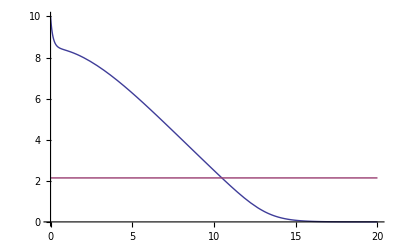

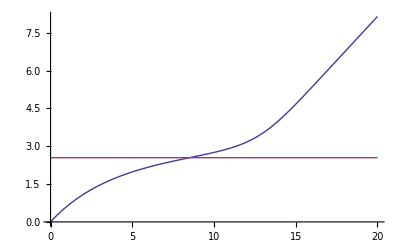

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=1;
k=0.1;
κ=0.7;
tmax=20;

sol=NDSolve[{
n'[t]==((ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) (-ⅇ^((γ l[t]^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax √(Vz/(1+Vz γ)) (Rtot-n[t])))/(√Vz))n[t],
l'[t]==κ-(bmax ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) Vz γ l[t] (Rtot-n[t]))/(2 (1+Vz γ)^(3/2)),
n[0]==10,l[0]==0},{n,l},{t,0,tmax}];

Plot[{n[t]/.sol,N/.Neq/.Leq},{t,0,tmax},PlotRange->{0,All}]
Plot[{l[t]/.sol,L/.Leq},{t,0,tmax},PlotRange->{0,All}]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

Higher predation intensities can delay unstable cycles (as well as critical rates, as discussed in text) and thus aid persistence (blue line has positive slope):

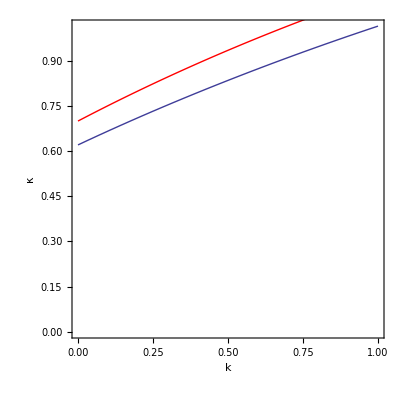

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=1;

Clear[k,κ]
Show[
ContourPlot[{Tr[jeq]==0(*,Det[jeq]==0*)}//Evaluate,{k,0,1},{κ,0,κ/.kc},FrameLabel->{"k","κ"}],
Plot[κ/.kc,{k,0,1},PlotStyle->Red]
]
Clear[bmax,Rtot,mconst,γ,Vz]
```

A numerical example showing that increasing k has removed unstable cycles at this rate of environmental change:

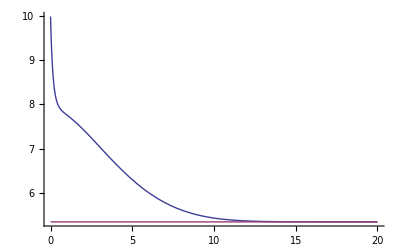

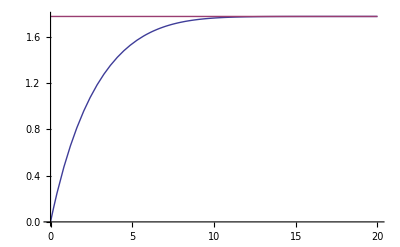

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=1;
k=0.5;
κ=0.666;
(*κ=0.83;*)
tmax=20;

sol=NDSolve[{
n'[t]==((ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) (-ⅇ^((γ l[t]^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax √(Vz/(1+Vz γ)) (Rtot-n[t])))/(√Vz))n[t],
l'[t]==κ-(bmax ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) Vz γ l[t] (Rtot-n[t]))/(2 (1+Vz γ)^(3/2)),
n[0]==10,l[0]==0},{n,l},{t,0,tmax}];

Plot[{n[t]/.sol,N/.Neq/.Leq},{t,0,tmax},PlotRange->{0,All}]
Plot[{l[t]/.sol,L/.Leq},{t,0,tmax},PlotRange->{0,All}]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

At lower phenotypic variances the ecological and evolutionary timescales become separated and population size goes to zero just when the unstable cycles emerge (meaning that the critical rate of environmental change as estimated by δ_c is a good estimate of when extinction occurs)

{κ→0.00115489+0. ⅈ}

{{N→0.0338477},{L→2.10028}}

{-0.000932019+0.00108813 ⅈ,-0.000932019-0.00108813 ⅈ}

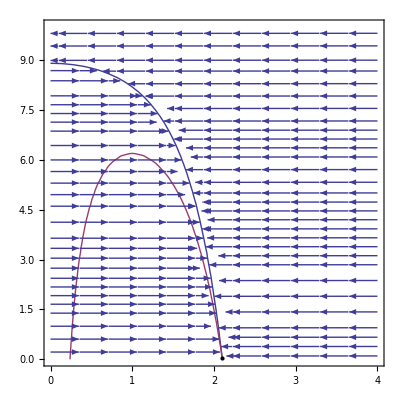

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=0.001;
k=0.1;

kc//N
κ=0.001154;

{Neq/.Leq,Leq}
Eigenvalues[jeq]

Show[
ContourPlot[{dNdt/N==0,-κ+dbarzdtApp==0}/.N->n/.θ->L+barz//Evaluate,{L,0,4},{n,0,Rtot}],
StreamPlot[{dNdt/N,-κ+dbarzdtApp}/.N->n/.θ->L+barz,{L,0,4},{n,0,Rtot}],
Graphics[{PointSize[Medium],Point[{L,N}/.Neq/.Leq]}]
]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

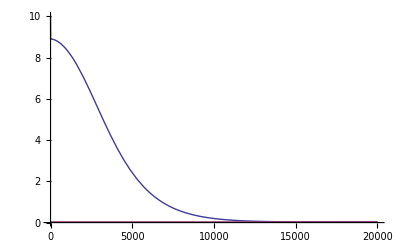

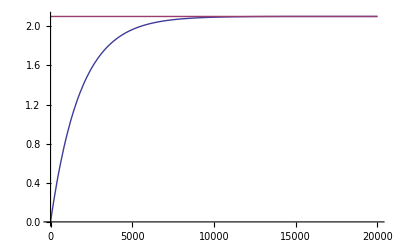

```mathematica
bmax=1;
Rtot=10;
mconst=1;
γ=1;
Vz=0.001;
k=0.1;
κ=0.001154;
tmax=20000;

sol=NDSolve[{
n'[t]==((ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) (-ⅇ^((γ l[t]^2)/(2+2 Vz γ)) (k+mconst) √Vz+bmax √(Vz/(1+Vz γ)) (Rtot-n[t])))/(√Vz))n[t],
l'[t]==κ-(bmax ⅇ^(-(γ l[t]^2)/(2+2 Vz γ)) Vz γ l[t] (Rtot-n[t]))/(2 (1+Vz γ)^(3/2)),
n[0]==10,l[0]==0},{n,l},{t,0,tmax}];

Plot[{n[t]/.sol,N/.Neq/.Leq},{t,0,tmax},PlotRange->{0,All}]
Plot[{l[t]/.sol,L/.Leq},{t,0,tmax},PlotRange->{0,All}]

Clear[bmax,Rtot,mconst,γ,Vz,k,κ,tmax]
```

### Quadratic selection

#### Model set-up

Let the per capita birth rate of an individual b be a quadratic function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and maximum per available resource birth rate bmax

```mathematica
b[z_,N_]:=bmax (1-γ (θ-z)^2)(Rtot-N)
```

where Rtot is the total density of resources in the system and N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

With sufficiently small variance (such that most birth rates are positive), the mean per capita birth rate is then

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

bmax (N-Rtot) (-1+γ (Vz+(barz-θ)^2))

We assume constant, equal per capita mortality and predation

```mathematica
m[z_,N_]:=mconst
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
f[z_,N_]:=1
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
```

Then the growth rate of a population composed of N individuals with trait value z is

```mathematica
dNdtz=N(b[z,N]-m[z,N]-k f[z,N])
```

N (-k-mconst+bmax (-N+Rtot) (1-γ (-z+θ)^2))

Integrating over all trait values, the population mean growth rate dN/dt is

```mathematica
dNdt=Integrate[dNdtz p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

N (-k-mconst+bmax (N-Rtot) (-1+γ (Vz+(barz-θ)^2)))

#### Birth

When an offspring with trait value z is born in a population that previously had mean trait value barz and density N, the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes (assuming a normal phenotype distribution with mean barz and variance Vz)

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

Given a prey individual is chosen to give birth, the probability it has trait value zP is

```mathematica
pzbirth=(b[zP,N]p[zP])/barb;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zP]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zP, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zP,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected trait mean after a selective birth is then

```mathematica
meanafterbirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected trait variance after a selective birth is

```mathematica
varafterbirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Death

PREY DEATH

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

The probability an individual with trait value zD dies is

```mathematica
pzdeath=(m[zD,N]p[zD])/barm;
```

After death the expected trait mean is

```mathematica
meanafterdeath=Simplify[Integrate[Factor[meand*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

After death the expected variance is

```mathematica
varafterdeath=Simplify[Integrate[Factor[vard*pzdeath/.z->zD],{zD,-∞,∞}],{Vz>0,α>0, γ>0}];
```

PREDATION

Given an individual is consumed by a predator, the probability it has trait value zC is

```mathematica
pzpred=(k f[zC,N]p[zC])/barkf;
```

After predation the expected trait mean is

```mathematica
meanafterpred=Simplify[Integrate[Factor[meand*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

After predation the expected variance is

```mathematica
varafterpred=Simplify[Integrate[Factor[vard*pzpred/.z->zC],{zC,-∞,∞}],{Vz>0,α>0,γ>0}];
```

#### Rate of evolution

Using the law of total probability, the expected mean trait after a small time Δt is

```mathematica
Ebarzdt=(1-Δt N(barb+barm+barkf))barz+Δt N(barb* meanafterbirth+barm* meanafterdeath+barkf*meanafterpred);
```

The rate of change in the mean trait value is thus

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp0=FullSimplify[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,Vz>0]
```

bmax (-1+N-Rtot) Vz γ (barz-θ)

And when the amount of available resources R = Rtot - N is much bigger than one we have

```mathematica
dbarzdtApp=Normal[Series[dbarzdtApp0/.N->Rtot-R/ϵ,{ϵ,0,-1}]//FullSimplify]/.ϵ->1/.R->Rtot-N
```

bmax (-N+Rtot) Vz γ (-barz+θ)

#### Equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+barkf))Vz+Δt N(barb *varafterbirth+ barm *varafterdeath+ barkf *varafterdeath);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1;
```

When the random effect is small (and therefore the variance is also small) we have, at equilibrium, approximately

```mathematica
Normal[Series[dVdtApp/.Vz->ϵ Vz/.α->α ϵ^(1/2),{ϵ,0,1}]]/.ϵ->1;
Veq=Solve[%==0,Vz]//FullSimplify
```

{{Vz→(2 (-2+N-Rtot) α^2)/(N-Rtot)}}

And when the amount of available resources R = Rtot-N is large (much greater than 2), this is approximately

```mathematica
VzEqApp=Normal[Series[Vz/.Veq/.N->Rtot-R/ϵ,{ϵ,0,0}]]
```

{2 α^2}

#### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[dNdt/N==0/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→Rtot+(k+mconst)/(bmax (-1+(L^2+Vz) γ))}

When the optimum changes at rate κ, and density is at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarzdtApp==κ/.Neq/.θ->L+barz,L][[1]]//FullSimplify
```

{L→(-(k+mconst) Vz γ+√((k Vz γ+mconst Vz γ)^2+4 γ κ (κ-Vz γ κ)))/(2 γ κ)}

The fastest rate of environmental change that the population can persist at is therefore less than

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ][[1]]//FullSimplify
```

{κ→-ⅈ √bmax √Rtot Vz √γ √(k+mconst+bmax Rtot (-1+Vz γ))}

The critical rate of environmental change changes with predation like

```mathematica
D[κ/.kc,k]//Simplify
```

-(ⅈ √bmax √Rtot Vz √γ)/(2 √(k+mconst+bmax Rtot (-1+Vz γ)))

which is always negative

A numerical example to demonstrate this point:

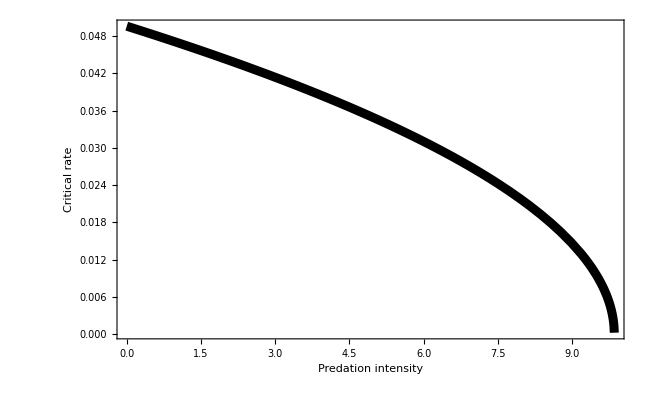

```mathematica
Show[
Plot[κ/.kc/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05,{k,0,10},PlotStyle->{Thickness[0.01],Black}],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
PlotRange->{0,All},
Frame->True, 
FrameLabel->{Style["Predation intensity",LabelSize],Style["Critical rate",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
(*FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},*)
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
PlotRangeClipping->False
(*PlotRangePadding->None*)
]
```

#### Applying the general analysis

```mathematica
dNdt=N (-k-mconst+bmax (N-Rtot) (-1+γ (Vz+(barz-θ)^2)));
```

The per capita growth rate

```mathematica
g[N_,barz_,k_]:=dNdt/N//Evaluate
```

The rate of evolution is approximately

```mathematica
dzdt=VA D[g[N,barz,k],barz]//Simplify
```

2 bmax (N-Rtot) VA γ (barz-θ)

This does not depend on k, but birth depends on both N and k such that Equation 3 is positive (here shown at equilibrium population size)

```mathematica
Solve[g[N,barz,k]==0,N]//Flatten;
dNdk=D[N/.%,k];
eq3=% D[dzdt,N]//FullSimplify
```

(2 VA γ (barz-θ))/(-1+γ (Vz+(barz-θ)^2))

The equilibrium population density as a function of trait value

```mathematica
nhat=Solve[g[N,barz,k]==0,N]//Flatten//Simplify
```

{N→(k+mconst+bmax Rtot (-1+barz^2 γ+Vz γ-2 barz γ θ+γ θ^2))/(bmax (-1+barz^2 γ+Vz γ-2 barz γ θ+γ θ^2))}

The critical lag (that which causes population density to go to zero)

```mathematica
critlag=Solve[0==N/.nhat/.barz->barzc,barzc][[1]]//Simplify
```

{barzc→(-√(-bmax Rtot γ (k+mconst+bmax Rtot (-1+Vz γ)))+bmax Rtot γ θ)/(bmax Rtot γ)}

The strength of selection at the critical rate

```mathematica
h=D[g[N,barz,k],barz]/.N->0/.barz->barzc//Simplify
```

-2 bmax Rtot γ (barzc-θ)

The terms in Equation 5 (first line)

```mathematica
{D[h,k],D[h,barzc],D[barzc/.critlag,k]}/.critlag//FullSimplify
```

{0,-2 bmax Rtot γ,1/(2 √(-bmax Rtot γ (k+mconst+bmax Rtot (-1+Vz γ))))}

Equation 5 (first line)

```mathematica
eq5=VA(D[h,k]+D[h,barzc]D[barzc/.critlag,k])/.critlag//FullSimplify
```

-(bmax Rtot VA γ)/(√(-bmax Rtot γ (k+mconst+bmax Rtot (-1+Vz γ))))

Equation 5 is always negative

The terms in Equation 5 (second line)

```mathematica
{D[D[g[0,barz,k],barz],k],D[D[g[0,barz,k],barz],barz],D[barzc/.critlag,k]}/.barz->barzc/.critlag//FullSimplify
```

{0,-2 bmax Rtot γ,1/(2 √(-bmax Rtot γ (k+mconst+bmax Rtot (-1+Vz γ))))}

Equation 5 (second line)

```mathematica
VA(D[D[g[0,barz,k],barz],k]+D[D[g[0,barz,k],barz],barz]D[barzc/.critlag,k])/.barz->barzc/.critlag//FullSimplify
```

-(bmax Rtot VA γ)/(√(-bmax Rtot γ (k+mconst+bmax Rtot (-1+Vz γ))))

Check that this is the same as directly differentiating the critical rate

```mathematica
Solve[κ==dzdt/.nhat,barz]//Flatten//Simplify;
Solve[0==N/.nhat/.%,κ][[2]]//Simplify;
D[κ/.%,k]//Simplify
```

(ⅈ √bmax √Rtot VA √γ)/(√(k+mconst+bmax Rtot (-1+Vz γ)))

## Generalist example 2B: evolutionary hydra effect (univoltine, overlapping generations)

### Model set-up

Let the expected number of offspring an individual produces each time step (i.e., breeding season) b be a Gaussian function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and maximum per available resource offspring number bmax

```mathematica
b[z_,N_]:=bmax Exp[-γ/2 (θ-z)^2](Rtot-N)
```

where Rtot is the total density of resources in the system and N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

The mean expected number of offspring per time step is then

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N+Rtot))/(√(1+Vz γ))

We will assume a constant per time step probability of mortality and predation

```mathematica
m[z_,N_]:=mconst
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
f[z_,N_]:=1
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
```

where mconst and k are in [0,1].

Assume overlapping generations. Then the expected number of individuals in the next time step in a population currently composed of N individuals with trait value z is

```mathematica
Nprimez=N((1+b[z,N])(1-m[z,N])(1-k f[z,N]))
```

(1-k) (1-mconst) N (1+bmax ⅇ^(-1/2 γ (-z+θ)^2) (-N+Rtot))

Notice that when mortality and predation probabilities per time step are small and the expected number of offspring per time step is also small, the change in the number of individuals is approximately

```mathematica
Normal[Series[Nprimez-N/.k->k ϵ/.mconst->mconst ϵ/.bmax->bmax ϵ,{ϵ,0,1}]]/.ϵ->1
```

N (-k-mconst+bmax ⅇ^(-1/2 γ (-z+θ)^2) (-N+Rtot))

which is the growth rate in the continuous time case.

Integrating over all trait values, the expected number of individuals in the next time step is

```mathematica
Nprime=Collect[Integrate[Nprimez p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}],bmax,Simplify]
```

(-1+k) (-1+mconst) N-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+k) (-1+mconst) N (N-Rtot) √(Vz/(1+Vz γ)))/(√Vz)

### Rate of evolution and equilibrium phenotypic variance

Following Lande 1976 (Evolution 30:314-334, eqn 7), the change in the mean trait value per time step is roughly

```mathematica
dbarz=VA D[Log[Nprime/N],barz]
```

(2 bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+k) (-1+mconst) N (N-Rtot) VA γ √(Vz/(1+Vz γ)) (barz-θ))/(√Vz (2+2 Vz γ) ((-1+k) (-1+mconst) N-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+k) (-1+mconst) N (N-Rtot) √(Vz/(1+Vz γ)))/(√Vz)))

where VA is the additive genetic variance.

### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[Nprime/N==1/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→(ⅇ^((L^2 γ)/(2+2 Vz γ)) (k (-1+mconst)-mconst) √Vz+bmax (-1+k) (-1+mconst) Rtot √(Vz/(1+Vz γ)))/(bmax (-1+k) (-1+mconst) √(Vz/(1+Vz γ)))}

When the optimum changes by κ each time step, and density is at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarz==κ/.Neq/.θ->L+barz,L]//Flatten//FullSimplify
```

{L→(κ+Vz γ κ)/(k VA γ+mconst VA γ-k mconst VA γ)}

The fastest rate of environmental change that the population can persist at is therefore less than

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ][[1]]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{κ→((k+mconst-k mconst) VA √γ √Log[(bmax^2 (-1+k)^2 (-1+mconst)^2 Rtot^2)/((k+mconst-k mconst)^2 (1+Vz γ))])/(√(1+Vz γ))}

The critical rate of environmental change changes with predation like

```mathematica
D[κ/.kc,k]//Simplify
```

-(VA √γ (-1+(-1+k) (-1+mconst) Log[(bmax^2 (-1+k)^2 (-1+mconst)^2 Rtot^2)/((k+mconst-k mconst)^2 (1+Vz γ))]))/((-1+k) √(1+Vz γ) √Log[(bmax^2 (-1+k)^2 (-1+mconst)^2 Rtot^2)/((k+mconst-k mconst)^2 (1+Vz γ))])

This can be positive when predation is low enough

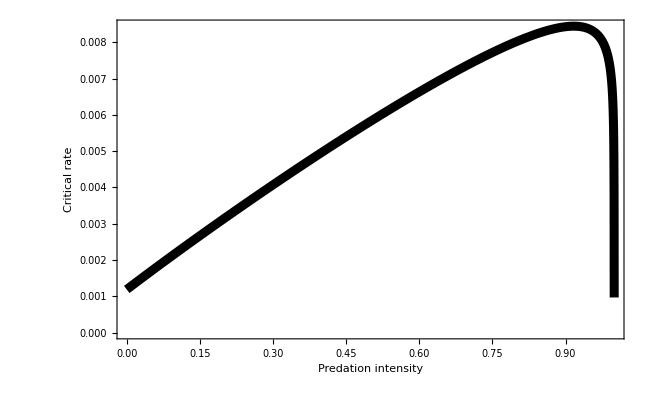

```mathematica
Show[
Plot[κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->10/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.C[1]->0,{k,0,1},PlotStyle->{Thickness[0.01],Black}],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->0}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{0.1,κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->0.1}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],*)
Frame->True, 
FrameLabel->{Style["Predation intensity",LabelSize],Style["Critical rate",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
(*FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},*)
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
(*Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},*)
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

(*Export[imagedir<>"GeneralistCriticalRatePredation.eps",%];*)
```

## Generalist example 2C: evolutionary hydra effect (univoltine, non-overlapping generations)

### Model set-up

Let the expected number of offspring an individual produces each time step (i.e., breeding season) b be a Gaussian function of the deviation between its trait value z and the optimal trait value θ, with selection strength γ and maximum offspring number bmax

```mathematica
b[z_,N_]:=bmax Exp[-γ/2 (θ-z)^2](Rtot-N)
```

where Rtot is the total density of resources in the system and N is the population density of the prey.

Let the trait distribution p[z] be Gaussian, with mean barz and variance Vz.

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)]
```

The mean expected number of offspring per time step is then

```mathematica
barb=Integrate[b[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]//FullSimplify
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N+Rtot))/(√(1+Vz γ))

We will assume a constant per time step probability of mortality and predation

```mathematica
m[z_,N_]:=mconst
barm=Integrate[m[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
f[z_,N_]:=1
barkf=Integrate[k f[z,N] p[z],{z,-∞,∞},Assumptions->{Vz>0}];
```

where mconst and k are in [0,1].

Assume non-overlapping generations. Then the expected number of individuals in the next time step in a population currently composed of N individuals with trait value z is

```mathematica
Nprimez=N(b[z,N](1-m[z,N])(1-k f[z,N]))
```

bmax ⅇ^(-1/2 γ (-z+θ)^2) (1-k) (1-mconst) N (-N+Rtot)

Notice that when mortality and predation probabilities per time step are small and the expected number of offspring per time step is also small, the change in the number of individuals is approximately

```mathematica
Normal[Series[Nprimez-N/.k->k ϵ/.mconst->mconst ϵ/.bmax->bmax ϵ,{ϵ,0,1}]]/.ϵ->1
```

-N+bmax ⅇ^(-1/2 γ (-z+θ)^2) N (-N+Rtot)

which is not the same as the growth rate in the continuous time case (we are missing the death terms: k and mconst).

Integrating over all trait values, the expected number of individuals in the next time step is

```mathematica
Nprime=Collect[Integrate[Nprimez p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}],bmax,Simplify]
```

-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+k) (-1+mconst) N (N-Rtot))/(√(1+Vz γ))

### Rate of evolution and equilibrium phenotypic variance

Following Lande 1976 (Evolution 30:314-334, eqn 7), the change in the mean trait value per time step is roughly

```mathematica
dbarz=VA D[Log[Nprime/N],barz]
```

-(2 VA γ (barz-θ))/(2+2 Vz γ)

where VA is the additive genetic variance.

### Steady-state and the critical rate of environmental change

For a given mean lag behind the optimal, L = θ - barz, equilibrium population density is

```mathematica
Neq=Solve[Nprime/N==1/.θ->L+barz,N]//FullSimplify//Flatten
```

{N→Rtot-(ⅇ^((L^2 γ)/(2+2 Vz γ)) √(1+Vz γ))/(bmax (-1+k) (-1+mconst))}

When the optimum changes by κ each time step, and density is at equilibrium, the steady-state lag is

```mathematica
Leq=Solve[dbarz==κ/.Neq/.θ->L+barz,L]//Flatten//FullSimplify
```

{L→(κ+Vz γ κ)/(VA γ)}

The fastest rate of environmental change that the population can persist at is therefore less than

```mathematica
kc=Solve[0==N/.Neq/.Leq,κ][[2]]/.C[1]->0//FullSimplify
```

{κ→(√2 √Log[(bmax (-1+k) (-1+mconst) Rtot)/(√(1+Vz γ))])/(√((1+Vz γ)/(VA^2 γ)))}

The critical rate of environmental change changes with predation like

```mathematica
D[κ/.kc,k]//Simplify
```

1/((-1+k) √((2+2 Vz γ)/(VA^2 γ)) √Log[(bmax (-1+k) (-1+mconst) Rtot)/(√(1+Vz γ))])

This is never positive for plausible k (0<=k<=1)

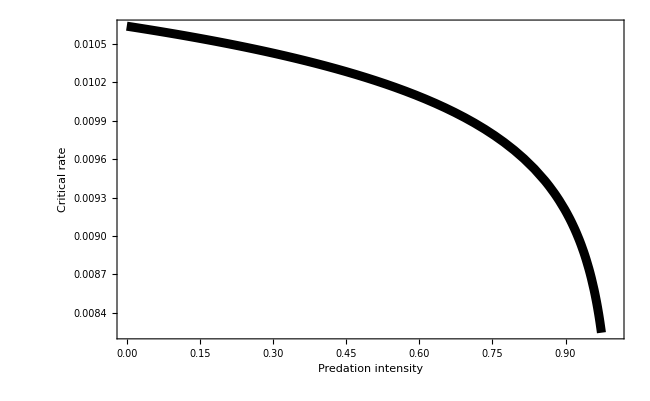

```mathematica
Show[
Plot[κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->10/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.C[1]->0,{k,0,1},PlotStyle->{Thickness[0.01],Black}],
(*Graphics[{Thickness[0.01],Blue,Line[{{0,0},{0,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->0}}]}],
Graphics[{Thickness[0.01],Red,Line[{{1,0},{1,κ/.kc/.Rtot->1000/.bmax->1/100/.m->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.c->1}}]}],*)
(*ListPlot[{{0,κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->0}},PlotStyle->Gray,PlotMarkers->{Automatic,Large}],
ListPlot[{{0.1,κ/.kc/.VA->Vz/2/.Rtot->1000/.bmax->1/100/.mconst->1/10/.Vz->2 α^2/.γ->1/.α->0.05/.k->0.1}},PlotStyle->Black,PlotMarkers->{Automatic,Large}],*)
Frame->True, 
FrameLabel->{Style["Predation intensity",LabelSize],Style["Critical rate",LabelSize],,},
(*FrameTicks->{{All,All},{All,All}},*)
(*FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},*)
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRange->{{0,10},{0,0.006}},*)
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
(*Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium genetic variance",LabelSize],Scaled@ylabpos],90 Degree]
},*)
PlotRangeClipping->False
(*PlotRangePadding->None*)
]

(*Export[imagedir<>"GeneralistCriticalRatePredation.eps",%];*)
```

## Specialist example 1A: selective push (trait-matching coevolution)

### Model set-up

Here we examine a model where prey are born at a per capita rate

```mathematica
b[z_,N_]:=bmax (Rtot-N-P)
```

where bmax is the per capita, per available resource birth rate for all individuals, Rtot is the total density of resource in the closed system, N is the density of the prey, and P is the density of the predator.

Let per capita prey mortality m be a quadratic function of the difference between prey trait value z and the abiotic optimum θ

```mathematica
m[z_,N_]:=mmin+γ/2(θ-z)^2
```

where mmin is the minimum per capita prey mortality rate and γ is the strength of selection on the prey to match the abiotic optimum.

With a normal prey trait distribution p with variance Vz and mean barz, mean mortality of the prey is

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)];
barm=Integrate[m[z,N]p[z],{z,-∞,∞},Assumptions->Vz>0]
```

1/2 (2 mmin+γ (Vz+(barz-θ)^2))

Let the per prey per predator predation rate k f be a quadratic function of the difference in prey and predator (zP) traits

```mathematica
f[z_,zP_]:=(1-γk/2(z-zP)^2)
```

where kmax is the per predator per prey predation rate when the trait values of prey and predator match and γk describes how quickly predation rates drop off from kmax as the two trait values diverge.

With a normal predator trait distribution pP with variance VzP and mean barzP, mean per prey per predator predation rate is

```mathematica
pP[zP_]:=1/Sqrt[2π VzP] Exp[(-(barzP-zP)^2)/(2VzP)];
barkf=Integrate[k f[z,zP]p[z]pP[zP],{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]
```

1/2 k (2-((barz-barzP)^2+Vz+VzP) γk)

where we’ve assumed weak enough selection from predation or small enough trait differences, such that all k ≥ 0.

Prey population growth rate is thus

```mathematica
dNdt=Integrate[p[z]pP[zP](b[z,N]-m[z,N]-k f[z,zP]P)N,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]//FullSimplify
```

1/2 N (-2 mmin-2 bmax (N+P-Rtot)+k P (-2+((barz-barzP)^2+Vz+VzP) γk)-γ (Vz+(barz-θ)^2))

And predator population growth rate is thus

```mathematica
dPdt=Integrate[p[z]pP[zP](e k f[z,zP]N-mP )P,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]//Simplify
```

-1/2 P (2 mP+e k N (-2+((barz-barzP)^2+Vz+VzP) γk))

where e is the conversion efficiency and mP is the per capita rate of predator mortality.

### Rates of evolution and equilibrium phenotypic variances

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

PREY BIRTH

Given a prey individual is chosen to give birth, the probability it has trait value zParent is

```mathematica
pzbirth=p[zParent];
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zParent]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zParent, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zParent,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected mean prey trait after a prey birth is then

```mathematica
meanafterpreybirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected variance in prey traits after a prey birth is

```mathematica
varafterpreybirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

PREDATOR BIRTH

Given a predator captures a prey, the probability the predator has trait value zC is

```mathematica
pcapture=Integrate[pP[zC]k f[z,zC]p[z],{z,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

To get an offspring with trait value zZPwe need a particular mate and then the appropriate random effect. This happens with probability

```mathematica
ppredmate=Integrate[pP[2(zP-ξ)-zC]u[ξ],{ξ,-∞,∞},Assumptions->{α>0,VzP>0}];
```

This can happen for any zC, in either order (the other parent could be chosen to give birth), so the probability, given a predator is born due to a predation event, that the new predator has trait value zP is

```mathematica
ppredbirth=2Integrate[pcapture*ppredmate,{zC,-∞,∞},Assumptions->{α>0,VzP>0}];
```

The expected trait mean after a predation birth is thus

```mathematica
meanafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(meanb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

The expected trait variance after a predation birth is

```mathematica
varafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(varb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

#### Death

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

PREY DEATH

Given a prey dies of background mortality, the probability the dead individual has trait value z is

```mathematica
penvdeath=(p[z]m[z,N])/barm;
```

After such a death the expected trait mean is

```mathematica
meanafterenvdeath=Simplify[Integrate[Factor[meand*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

After such a death the trait variance is

```mathematica
varafterenvdeath=Simplify[Integrate[Factor[vard*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

PREDATION

Given a prey is killed by a predator, the probability the dead prey has trait value z is

```mathematica
pcaught=Integrate[p[z]k f[z,zP]pP[zP],{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

After such a death the expected trait mean is

```mathematica
meanafterpredation=Simplify[Integrate[Factor[pcaught*meand],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

After such a death the expected variance is

```mathematica
varafterpredation=Simplify[Integrate[Factor[pcaught*vard],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

PREDATOR DEATH

After a predator death the expected trait mean is

```mathematica
meanafterpreddeath=Simplify[Integrate[Factor[(meand/.barz->barzP/.Vz->VzP/.z->zP/.N->P)*pP[zP]],{zP,-∞,∞}],{VzP>0,α>0}];
```

After a predator death the expected variance is

```mathematica
varafterpreddeath=Simplify[Integrate[Factor[(vard/.barz->barzP/.Vz->VzP/.z->zP/.N->P)*pP[zP]],{zP,-∞,∞}],{VzP>0,α>0}];
```

#### Rate of prey evolution

Expected prey mean after short time Δt

```mathematica
Ebarzdt=(1-Δt N (b[z,N]+barm+ barkf P))barz+Δt N(b[z,N] meanafterpreybirth+barm* meanafterenvdeath+barkf P* meanafterpredation);
```

The change in the mean is then

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp=Collect[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify,{γ,γk,Vz,Z}]
```

(barz k P-barzP k P) Vz γk+Vz γ (-barz+θ)

#### Rate of predator evolution

Expected mean after short time Δt

```mathematica
EbarzPdt=(1-Δt P ( e barkf N+mP))barzP+Δt P( e barkf N* meanafterpredbirth+ mP meanafterpreddeath);
```

The change in the mean is then

```mathematica
dbarzPdt=Limit[(EbarzPdt-barzP)/Δt,Δt->0];
```

To zeroth order in 1/P this is

```mathematica
dbarzPdtApp=Normal[Series[dbarzPdt/.P->P/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

1/2 (barz-barzP) e k N VzP γk

#### Prey equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N( b[z,N]+ barm+ barkf P))Vz+Δt N( b[z,N] varafterpreybirth+ barm *varafterenvdeath+ barkf P * varafterpredation);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0]//FullSimplify;
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1//Simplify
```

1/2 (bmax (P Vz-Rtot Vz+4 α^2-2 P α^2+2 Rtot α^2+N (Vz-2 α^2))-2 Vz^2 (γ-k P γk))

And at equilibrium we have

```mathematica
FullSimplify[Normal[Series[Vz/.Solve[0==dVdtApp,Vz],{α,0,2}]],{bmax>0,N>0,P>0,Rtot>0,Rtot>N+P}]
```

{-(2 (-2+N+P-Rtot) α^2)/(N+P-Rtot)+(bmax (N+P-Rtot))/(2 (γ-k P γk)),(2 (-2+N+P-Rtot) α^2)/(N+P-Rtot)}

Finally, when the amount of available resources in the system R is large, we have approximately

```mathematica
Normal[Series[%/.N+P-Rtot->R/.R->R/ϵ,{ϵ,0,0}]]/.ϵ->1
```

{-2 α^2+(bmax R)/(2 (γ-k P γk)),2 α^2}

We will see with numerical and simulation results that the relevant equilibrium is

```mathematica
VzEqApp=%[[2]]
```

2 α^2

#### Predator equilibrium variance

The expected variance after a small time Δt is

```mathematica
EvarPdt=(1-Δt P (e barkf N+ m))VzP+Δt P( e barkf N* varafterpredbirth+m varafterpreddeath);
```

The rate of change in variance is thus

```mathematica
dVPdt=Limit[(EvarPdt-VzP)/Δt,Δt->0]//FullSimplify;
```

To zeroth order in 1/P this is

```mathematica
dVPdtApp=Normal[Series[dVPdt/.P->P/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

1/4 e k N (-2 VzP+4 α^2+(((barz-barzP)^2+Vz) VzP-2 ((barz-barzP)^2+Vz+VzP) α^2) γk)

And at equilibrium we have

```mathematica
Series[VzP/.Solve[0==dVPdtApp,VzP],{α,0,3}]
```

{2 α^2+O[α]^4}

```mathematica
VzPEqApp=Normal[%][[1]]
```

2 α^2

### Quick [can run instead of section directly above if model unchanged]

```mathematica
dNdt=1/2 N (-2 mmin-2 bmax (N+P-Rtot)+k P (-2+((barz-barzP)^2+Vz+VzP) γk)-γ (Vz+(barz-θ)^2));
dPdt=-1/2 P (2 mP+e k N (-2+((barz-barzP)^2+Vz+VzP) γk));
dbarzdt=(N Vz (-barz γ+barz k P γk-barzP k P γk+γ θ))/(-1+N);
dbarzPdt=((barz-barzP) e k N P VzP γk)/(2 (1+P));
dbarzdtApp=(barz k P-barzP k P) Vz γk+Vz γ (-barz+θ);
dbarzPdtApp=1/2 (barz-barzP) e k N VzP γk;
dVdt=(N (-2 mmin (1+N)^2 Vz+bmax (-1+N)^2 (N+P-Rtot) ((2+N) Vz-2 N α^2)+(1+N)^2 Vz (k P (-2+((barz-barzP)^2+Vz+2 N Vz+VzP) γk)-γ (Vz+2 N Vz+(barz-θ)^2))))/(2 (-1+N^2)^2);
dVPdt=(P (-4 m (1+P)^2 VzP+e k N (-1+P)^2 (-2 (2+P) VzP+4 P α^2+(VzP ((2+P) ((barz-barzP)^2+Vz)+2 VzP)-2 P ((barz-barzP)^2+Vz+VzP) α^2) γk)))/(4 (-1+P^2)^2);
```

### Steady-state and critical rates of environmental change

The steady-state lags and equilibrium population sizes are

```mathematica
CoevoEq=Solve[{dbarzdtApp==κ,dbarzPdtApp==κ,dNdt==0,dPdt==0}/.barzP->barz-LP/.barz->θ-L//Simplify,{L,LP,P,N}];
```

In the prey-only case we have

```mathematica
PreyOnlyCoevo=CoevoEq[[5]];
```

And in the full community we have

```mathematica
FullCoevo=CoevoEq[[3]];
```

The critical rate of environmental change for the prey is

```mathematica
kc=Solve[0==N/.PreyOnlyCoevo,κ][[1]]
```

{κ→-ⅈ Vz √γ √(2 mmin-2 bmax Rtot+Vz γ)}

The critical rate of change for the predator is harder to solve for directly

```mathematica
(*kcp=Solve[0==P/.FullCoevo,κ]*)
```

But we can show that prey and predator densities at the coexistence equilibrium can be positive when the prey-only density is zero (or negative)

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/1000;α=1/20;Vz=2 α^2;
e=1/4;mP=1;k=1/100;
γk=1/10;αP=1/20;VzP=2 αP^2;
κ =8/10000;

N/.PreyOnlyCoevo//N
N/.FullCoevo//N
P/.FullCoevo//N

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ,αP,VzP]
```

-290.

549.386

100.077

implying that the specialist predator can help the prey persist in this case.

We can look at this more generally by noting that the equilibrium predator density (without substituting in lags and prey density) is

```mathematica
peq=Solve[0==FullSimplify[dNdt/N/.barzP->LP+barz/.barz->θ+L],P]//FullSimplify//Flatten
```

{P→(-2 mmin+2 bmax (-N+Rtot)-(L^2+Vz) γ)/(2 (bmax+k)-k (LP^2+Vz+VzP) γk)}

and the equilibrium prey density in the absence of predators is

```mathematica
neq=Solve[0==FullSimplify[dNdt/N/.barzP->LP+barz/.barz->θ+L/.P->0],N]//Flatten
```

{N→(-2 mmin+2 bmax Rtot-L^2 γ-Vz γ)/(2 bmax)}

The prey lags in the two cases (with and without predators) can be different, so call Lwith the lag with the predator

```mathematica
pEq=P/.peq/.L->Lwith
```

(-2 mmin+2 bmax (-N+Rtot)-(Lwith^2+Vz) γ)/(2 (bmax+k)-k (LP^2+Vz+VzP) γk)

and L the lag without the predator

```mathematica
nEq=N/.neq
```

(-2 mmin+2 bmax Rtot-L^2 γ-Vz γ)/(2 bmax)

Then the condition for the predator helping prey persist is

```mathematica
Reduce[pEq>0&&nEq<0&&bmax>0&&mmin>0&&N>0&&Rtot>0&&γ>0&&Vz>0&&k>0&&γk>0&&VzP>0&&Rtot bmax>Vz γ/2+mmin&&N<(-2 mmin+2 bmax Rtot-Vz γ)/(2 bmax)&&L>√((-2 mmin+2 bmax Rtot-Vz γ)/γ)&&γk<2/(LP^2+Vz+VzP),Reals]
```

γ>0&&Vz>0&&Rtot>0&&bmax>(Vz γ)/(2 Rtot)&&0<mmin<1/2 (2 bmax Rtot-Vz γ)&&L>√((-2 mmin+2 bmax Rtot-Vz γ)/γ)&&VzP>0&&0<N<(-2 mmin+2 bmax Rtot-Vz γ)/(2 bmax)&&-√((-2 mmin-2 bmax N+2 bmax Rtot-Vz γ)/γ)<Lwith<√((-2 mmin-2 bmax N+2 bmax Rtot-Vz γ)/γ)&&0<γk<2/(LP^2+Vz+VzP)&&k>0

The N inequality just says that the density of prey with predators should be less than the density of perfectly adapted prey without predators (which is always true without Abram’s “ecological” hydra effect; Abrams, P. 2009. When does greater mortality increase population size? The long history and diverse mechanisms underlying the hydra effect. Ecology Letters 12:462–74.)

```mathematica
N/.PreyOnlyCoevo/.κ->0//Simplify
```

-(2 mmin-2 bmax Rtot+Vz γ)/(2 bmax)

The L inequality (note that L>0) just says that we need to be past the critical rate of change for the prey (so that N<0 without predators)

```mathematica
Solve[L==√((-mmin+bmax Rtot-Vz γ)/γ)/.PreyOnlyCoevo,κ]//Flatten
```

{κ→Vz γ √((-mmin+bmax Rtot-Vz γ)/γ)}

The γk inequality just says that selection is weak enough such that the average predation term 1- γk/2 * (LP^2 + Vz + VzP) is positive.

And so we are left with the Lwith condition, meaning that predators can only help prey persist when they reduce the prey’s lag enough to allow it to grow in the absence of predators (giving the predator something to eat)

```mathematica
Solve[0==dNdt/N/.barz->θ-L/.P->0//Simplify,L]
```

{{L→-(√(-2 mmin-2 bmax N+2 bmax Rtot-Vz γ))/(√γ)},{L→(√(-2 mmin-2 bmax N+2 bmax Rtot-Vz γ))/(√γ)}}

### Temporal dynamics (slow; with simulation results)

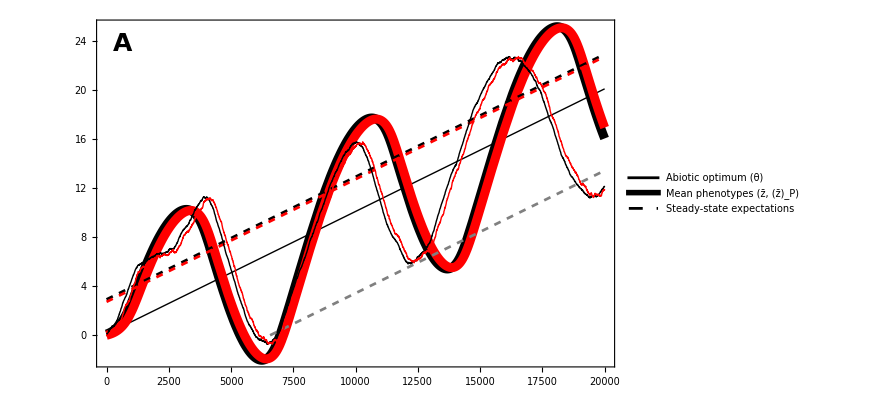

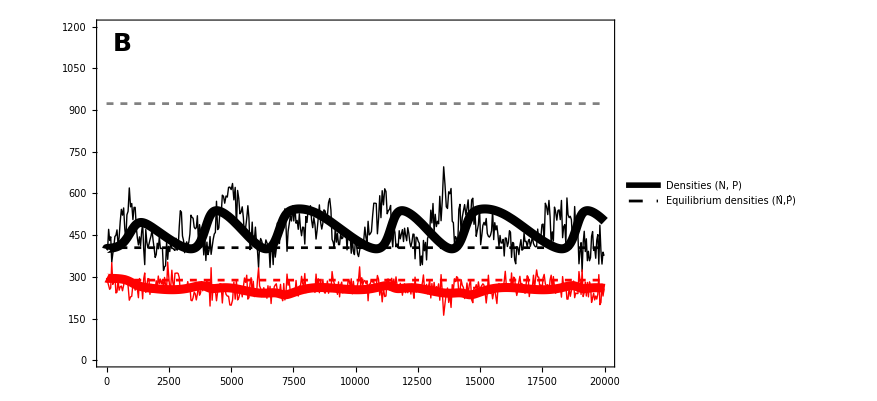

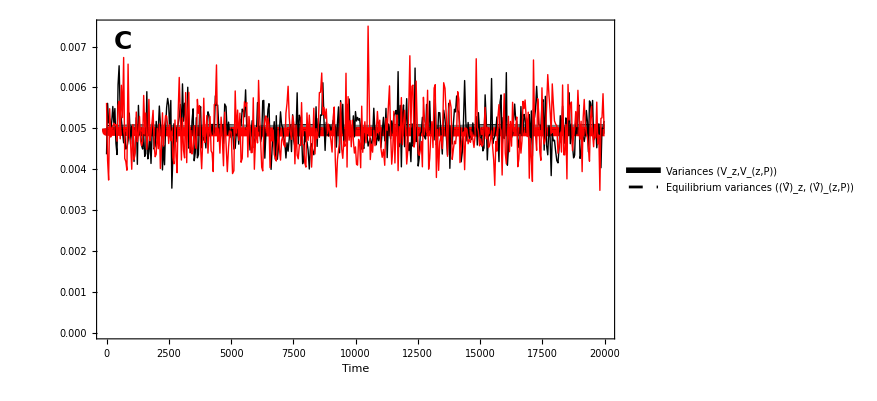

```mathematica
col[1]=Black;
col[2]=Gray;
col[3]=Red;

(*simulation results*)
rep="2";

num=1;
simdir[1]=datadir<>"SPECIALIST/MATCHING/PREDALL/k0pt001/";
(*simdir[2]=datadir<>"SPECIALIST/MATCHING/NOPREDEG/";*)
Table[zdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,num}];
Table[zPdat[i]=Import[simdir[i]<>"zZ_k1_r"<>rep<>".dat","CSV"],{i,1,1}];
Table[Ndat[i] = Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,num}];
Table[Pdat[i] = Import[simdir[i]<>"Z_k1_r"<>rep<>".dat"],{i,1,1}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
tmax=20000;LP0=0;θ0=0.1;L0=θ0;n0=mP/(k e);P0=(bmax(Rtot-mP/(k e))-mmin)/(bmax+k);
κ=1/1000;

(*numerical solution*)
sol[1]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
barzP'[t]==(dbarzPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
VzP'[t]==(dVPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0/.m->mP),
barz[0]==L0,
barzP[0]==LP0,
n[0]==n0,
P[0]==P0,
Vz[0]==2 α^2,
VzP[0]==2 αP^2
},
{barz,barzP,n,P,Vz,VzP},{t,0,tmax},MaxSteps->10^6];

sol[2]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
barz[0]==L0,
n[0]==Rtot-mmin/bmax,
Vz[0]==2 α^2
},
{barz,n,Vz},{t,0,tmax}];

(*plot phenotypes*)
Legended[
Show[
Plot[κ t+θ0,{t,0,tmax},PlotStyle->{Black,Thick}],
Table[Plot[Evaluate[barz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,num}],
Plot[Evaluate[barzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]}],
Plot[(κ t +θ0-L/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
Plot[(κ t +θ0-L/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]},PlotRange->{0,All}],
Plot[(κ t +θ0-L-LP/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,1]]},{i,1,Dimensions[Ndat[j]][[1]],1}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,1]]},{i,1,Dimensions[zPdat[1]][[1]],1}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},All},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed]},
{Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotypes (z̄, (z̄)_P)",LabelSize],
(*Style["Mean predator phenotype ((z̄)_P)",LabelSize],*)
Style["Steady-state expectations",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalTraitColor.eps",%];*)

(*plot densities*)
Legended[
Show[
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,num}],
Plot[Evaluate[P[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[N/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
Plot[N/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]}],
Plot[P/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],Ndat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],Pdat[1][[i,2]]},{i,1,Dimensions[Pdat[1]][[1]],10}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},{0,1.2*Rtot}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed](*,
Directive[Thickness[0.1],Gray,Dashed]*)},
{Style["Densities (N, P)",LabelSize],
(*Style["Predator density (P)",LabelSize],*)
(*Style["Equilibrium prey density (N̂)",LabelSize],
Style["Equilibrium predator density (P̂)",LabelSize]*)
Style["Equilibrium densities (N̂,P̂)",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalDensityColor.eps",%];*)

Legended[
Show[
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,2}],
Plot[Evaluate[VzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[Vz/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Thickness[0.003],Dashed}],
Plot[VzP/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Thickness[0.003],Dashed}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,2]]},{i,1,Dimensions[zPdat[1]][[1]],10}],PlotStyle->col[3],Joined->True],
PlotRange->{{0,tmax},{0,1.5*2 α^2}},
Frame->True,
FrameLabel->{Style["Time",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashed]},
{Style["Variances (V_z,V_(z,P))",LabelSize],
Style["Equilibrium variances ((V̂)_z, (V̂)_(z,P))",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.5,0.2}
]
]

(*Export[imagedir<>"CoevoTemporalVarianceColor.eps",%];*)

Clear[rep,zPdat,zdat,Ndat,Pdat,bmax,mmin,Rtot,kmax,e,mP,γ,tmax,L0,LP0,n0,P0,αP,α,Vz,VzP,κ,ndlag,OptPlot,zPNumPlot,zNumPlot,zPAnalPlot,zAnalPlot,zPSimPlot,zSimPlot,PNumPlot,NumPlot,PAnalPlot,AnalPlot,PreyOnlyPlot,SimPlot,PSimPlot,θ0,simdir,γk,θp,k,col1,col2,col3]
```

### Temporal dynamics (medium; with simulation results)

-Graphics-

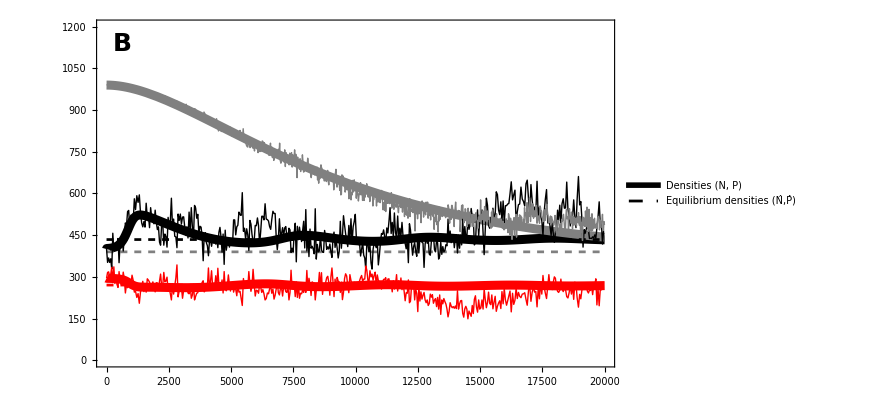

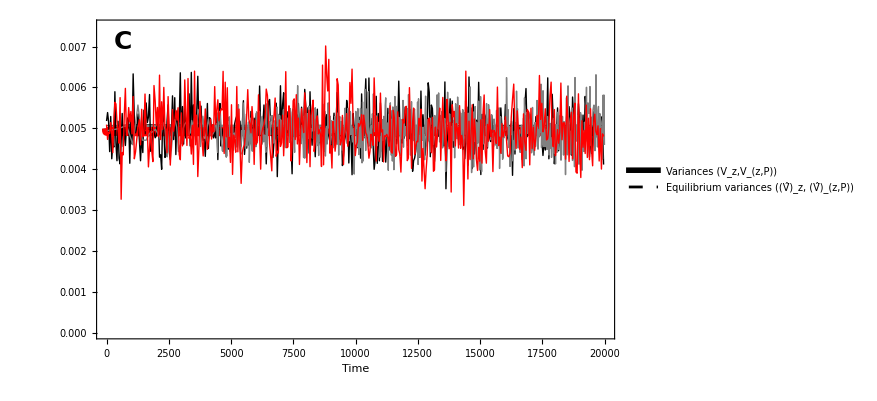

```mathematica
col[1]=Black;
col[2]=Gray;
col[3]=Red;

(*simulation results*)
rep="8";

simdir[1]=datadir<>"SPECIALIST/MATCHING/PREDALL/k0pt003/";
simdir[2]=datadir<>"SPECIALIST/MATCHING/NOPREDALL/k0pt003/";
Table[zdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,2}];
Table[zPdat[i]=Import[simdir[i]<>"zZ_k1_r"<>rep<>".dat","CSV"],{i,1,1}];
Table[Ndat[i] = Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,2}];
Table[Pdat[i] = Import[simdir[i]<>"Z_k1_r"<>rep<>".dat"],{i,1,1}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
tmax=20000;LP0=0;θ0=0.1;L0=θ0;n0=mP/(k e);P0=(bmax(Rtot-mP/(k e))-mmin)/(bmax+k);
κ=3/1000;

(*numerical solution*)
sol[1]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
barzP'[t]==(dbarzPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
VzP'[t]==(dVPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0/.m->mP),
barz[0]==L0,
barzP[0]==LP0,
n[0]==n0,
P[0]==P0,
Vz[0]==2 α^2,
VzP[0]==2 αP^2
},
{barz,barzP,n,P,Vz,VzP},{t,0,tmax},MaxSteps->10^6];

sol[2]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
barz[0]==L0,
n[0]==Rtot-mmin/bmax,
Vz[0]==2 α^2
},
{barz,n,Vz},{t,0,tmax}];

(*plot phenotypes*)
Legended[
Show[
Plot[κ t+θ0,{t,0,tmax},PlotStyle->{Black,Thick}],
Table[Plot[Evaluate[barz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,2}],
Plot[Evaluate[barzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]}],
Plot[(κ t +θ0-L/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
Plot[(κ t +θ0-L/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]},PlotRange->{0,All}],
Plot[(κ t +θ0-L-LP/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,1]]},{i,1,Dimensions[Ndat[j]][[1]],1}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,2}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,1]]},{i,1,Dimensions[zPdat[1]][[1]],1}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},{0,All}},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
{
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed]},
{Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotypes (z̄, (z̄)_P)",LabelSize],
(*Style["Mean predator phenotype ((z̄)_P)",LabelSize],*)
Style["Steady-state expectations",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
](*,
Placed[
LineLegend[
{Directive[Thickness[0.35],Red],
Directive[Thickness[0.35],Black],
Directive[Thickness[0.35],Gray]},
{Style["Predator",LabelSize],
Style["Prey with predator",LabelSize],
Style["Prey only",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.79,0.16}
]
}
]*),
Placed[
LineLegend[{
Directive[Red,Thickness[0.35]]
},
{
Style["Predator",LabelSize,Bold,Red]
}
],
{0.45,1}
] ,
Placed[
LineLegend[{
Directive[Black,Thickness[0.35]]
},
{
Style["Prey with predator",LabelSize,Bold]
}
],
{0.8,1}
] 
}
]

Export[imagedir<>"CoevoTemporalTraitColor.eps",%];

(*plot densities*)
Legended[
Show[
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,2}],
Plot[Evaluate[P[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[N/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
Plot[N/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]}],
Plot[P/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],Ndat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,2}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],Pdat[1][[i,2]]},{i,1,Dimensions[Pdat[1]][[1]],10}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},{0,1.2*Rtot}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed](*,
Directive[Thickness[0.1],Gray,Dashed]*)},
{Style["Densities (N, P)",LabelSize],
(*Style["Predator density (P)",LabelSize],*)
(*Style["Equilibrium prey density (N̂)",LabelSize],
Style["Equilibrium predator density (P̂)",LabelSize]*)
Style["Equilibrium densities (N̂,P̂)",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"CoevoTemporalDensityColor.eps",%];

Legended[
Show[
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,2}],
Plot[Evaluate[VzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[Vz/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Thickness[0.003],Dashed}],
Plot[VzP/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Thickness[0.003],Dashed}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotStyle->col[j],Joined->True],{j,1,2}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,2]]},{i,1,Dimensions[zPdat[1]][[1]],10}],PlotStyle->col[3],Joined->True],
PlotRange->{{0,tmax},{0,1.5*2 α^2}},
Frame->True,
FrameLabel->{Style["Time",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashed]},
{Style["Variances (V_z,V_(z,P))",LabelSize],
Style["Equilibrium variances ((V̂)_z, (V̂)_(z,P))",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.5,0.2}
]
]

Export[imagedir<>"CoevoTemporalVarianceColor.eps",%];

Clear[rep,zPdat,zdat,Ndat,Pdat,bmax,mmin,Rtot,kmax,e,mP,γ,tmax,L0,LP0,n0,P0,αP,α,Vz,VzP,κ,ndlag,OptPlot,zPNumPlot,zNumPlot,zPAnalPlot,zAnalPlot,zPSimPlot,zSimPlot,PNumPlot,NumPlot,PAnalPlot,AnalPlot,PreyOnlyPlot,SimPlot,PSimPlot,θ0,simdir,γk,θp,k,col1,col2,col3]
```

### Temporal dynamics (fast; with simulation results)

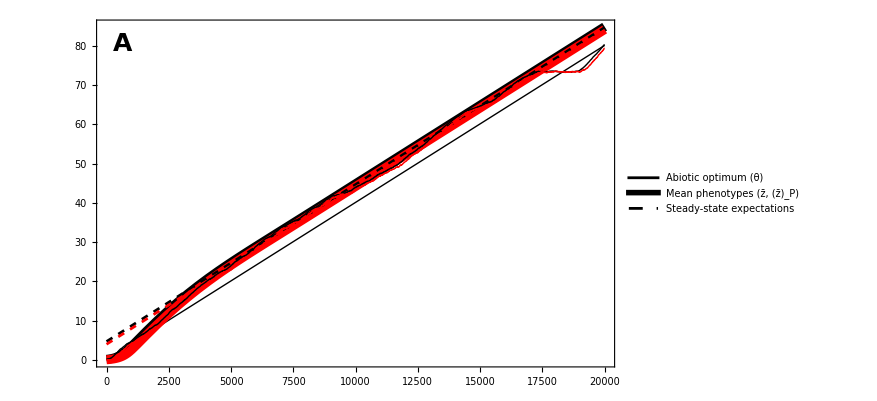

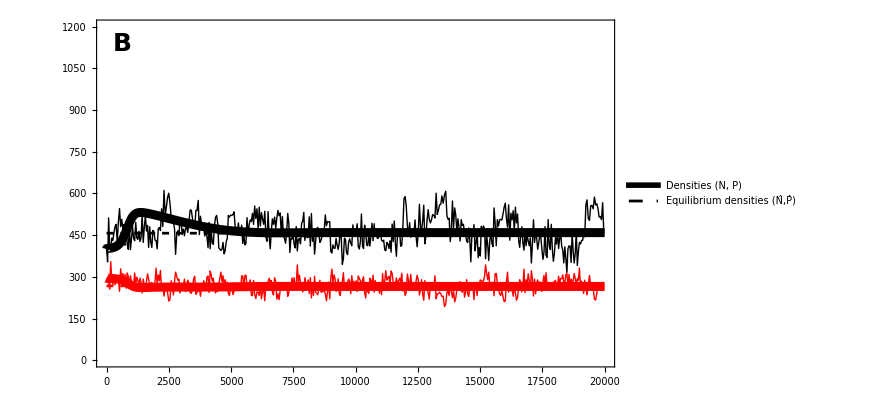

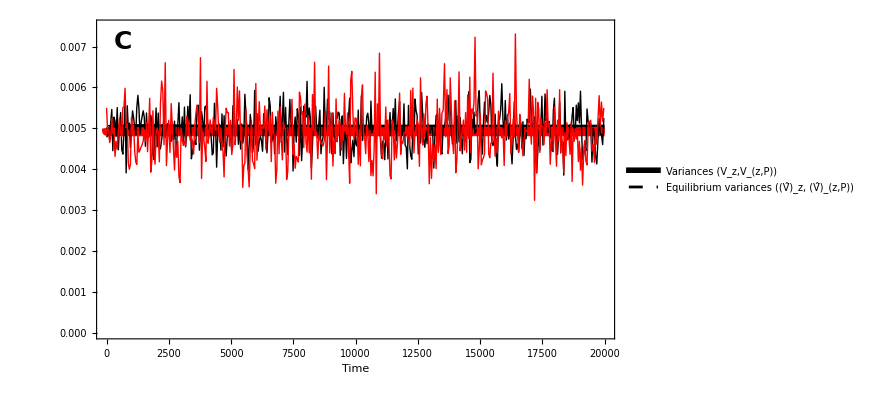

```mathematica
col[1]=Black;
col[2]=Gray;
col[3]=Red;

(*simulation results*)
rep="1";
num=1;
simdir[1]=datadir<>"SPECIALIST/MATCHING/PREDALL/k0pt004/";
(*simdir[2]=datadir<>"SPECIALIST/MATCHING/NOPREDEG/";*)
Table[zdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,num}];
Table[zPdat[i]=Import[simdir[i]<>"zZ_k1_r"<>rep<>".dat","CSV"],{i,1,1}];
Table[Ndat[i] = Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,num}];
Table[Pdat[i] = Import[simdir[i]<>"Z_k1_r"<>rep<>".dat"],{i,1,1}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
tmax=20000;LP0=0;θ0=0.1;L0=θ0;n0=mP/(k e);P0=(bmax(Rtot-mP/(k e))-mmin)/(bmax+k);
κ=4/1000;

(*numerical solution*)
sol[1]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
barzP'[t]==(dbarzPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
VzP'[t]==(dVPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0/.m->mP),
barz[0]==L0,
barzP[0]==LP0,
n[0]==n0,
P[0]==P0,
Vz[0]==2 α^2,
VzP[0]==2 αP^2
},
{barz,barzP,n,P,Vz,VzP},{t,0,tmax},MaxSteps->10^6];

sol[2]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
barz[0]==L0,
n[0]==Rtot-mmin/bmax,
Vz[0]==2 α^2
},
{barz,n,Vz},{t,0,tmax}];

(*plot phenotypes*)
Legended[
Show[
Plot[κ t+θ0,{t,0,tmax},PlotStyle->{Black,Thick}],
Table[Plot[Evaluate[barz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,num}],
Plot[Evaluate[barzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]}],
Plot[(κ t +θ0-L/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
(*Plot[(κ t +θ0-L/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]},PlotRange->{0,All}],*)
Plot[(κ t +θ0-L-LP/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,1]]},{i,1,Dimensions[Ndat[j]][[1]],1}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,1]]},{i,1,Dimensions[zPdat[1]][[1]],1}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},All},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed]},
{Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotypes (z̄, (z̄)_P)",LabelSize],
(*Style["Mean predator phenotype ((z̄)_P)",LabelSize],*)
Style["Steady-state expectations",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalTraitColor.eps",%];*)

(*plot densities*)
Legended[
Show[
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,num}],
Plot[Evaluate[P[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[N/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
(*Plot[N/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]}],*)
Plot[P/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],Ndat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],Pdat[1][[i,2]]},{i,1,Dimensions[Pdat[1]][[1]],10}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},{0,1.2*Rtot}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed](*,
Directive[Thickness[0.1],Gray,Dashed]*)},
{Style["Densities (N, P)",LabelSize],
(*Style["Predator density (P)",LabelSize],*)
(*Style["Equilibrium prey density (N̂)",LabelSize],
Style["Equilibrium predator density (P̂)",LabelSize]*)
Style["Equilibrium densities (N̂,P̂)",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalDensityColor.eps",%];*)

Legended[
Show[
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,num}],
Plot[Evaluate[VzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[Vz/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Thickness[0.003],Dashed}],
Plot[VzP/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Thickness[0.003],Dashed}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,2]]},{i,1,Dimensions[zPdat[1]][[1]],10}],PlotStyle->col[3],Joined->True],
PlotRange->{{0,tmax},{0,1.5*2 α^2}},
Frame->True,
FrameLabel->{Style["Time",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashed]},
{Style["Variances (V_z,V_(z,P))",LabelSize],
Style["Equilibrium variances ((V̂)_z, (V̂)_(z,P))",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.5,0.2}
]
]

(*Export[imagedir<>"CoevoTemporalVarianceColor.eps",%];*)

Clear[num,rep,zPdat,zdat,Ndat,Pdat,bmax,mmin,Rtot,kmax,e,mP,γ,tmax,L0,LP0,n0,P0,αP,α,Vz,VzP,κ,sol,col]
```

### Temporal dynamics (faster; with simulation results)

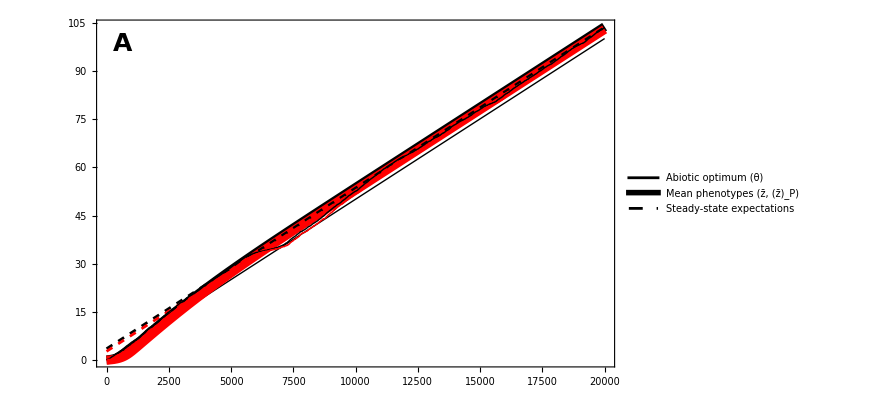

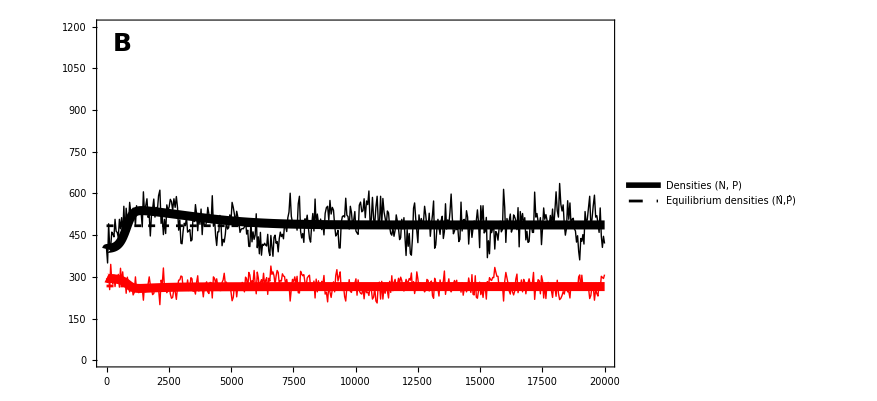

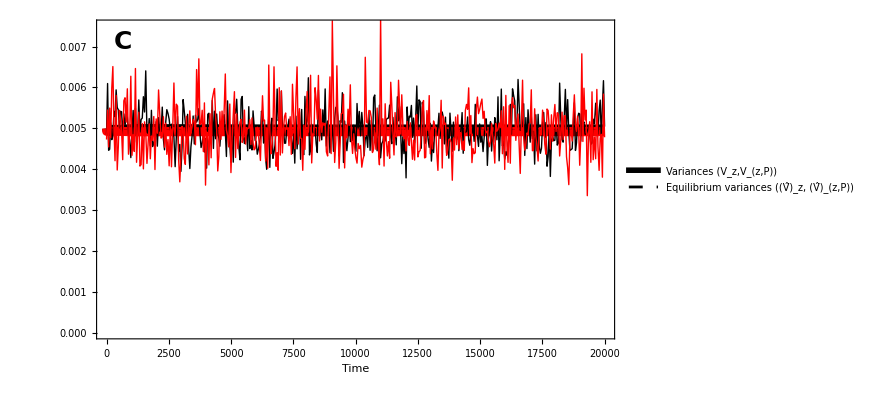

```mathematica
col[1]=Black;
col[2]=Gray;
col[3]=Red;

(*simulation results*)
rep="1";
num=1;
simdir[1]=datadir<>"SPECIALIST/MATCHING/PREDALL/k0pt005/";
(*simdir[2]=datadir<>"SPECIALIST/MATCHING/NOPREDEG/";*)
Table[zdat[i]=Import[simdir[i]<>"zP_k1_r"<>rep<>".dat","CSV"],{i,1,num}];
Table[zPdat[i]=Import[simdir[i]<>"zZ_k1_r"<>rep<>".dat","CSV"],{i,1,1}];
Table[Ndat[i] = Import[simdir[i]<>"P_k1_r"<>rep<>".dat"],{i,1,num}];
Table[Pdat[i] = Import[simdir[i]<>"Z_k1_r"<>rep<>".dat"],{i,1,1}];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
tmax=20000;LP0=0;θ0=0.1;L0=θ0;n0=mP/(k e);P0=(bmax(Rtot-mP/(k e))-mmin)/(bmax+k);
κ=5/1000;

(*numerical solution*)
sol[1]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
barzP'[t]==(dbarzPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0),
VzP'[t]==(dVPdt/.N->n[t]/.P->P[t]/.barzP->barzP[t]/.barz->barz[t]/.Vz->Vz[t]/.VzP->VzP[t]/.θ->κ t+θ0/.m->mP),
barz[0]==L0,
barzP[0]==LP0,
n[0]==n0,
P[0]==P0,
Vz[0]==2 α^2,
VzP[0]==2 αP^2
},
{barz,barzP,n,P,Vz,VzP},{t,0,tmax},MaxSteps->10^6];

sol[2]=NDSolve[
{
barz'[t]==(dbarzdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
n'[t]==(dNdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
Vz'[t]==(dVdt/.N->n[t]/.P->0/.barz->barz[t]/.Vz->Vz[t]/.θ->κ t+θ0),
barz[0]==L0,
n[0]==Rtot-mmin/bmax,
Vz[0]==2 α^2
},
{barz,n,Vz},{t,0,tmax}];

(*plot phenotypes*)
Legended[
Show[
Plot[κ t+θ0,{t,0,tmax},PlotStyle->{Black,Thick}],
Table[Plot[Evaluate[barz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]}],{i,1,num}],
Plot[Evaluate[barzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]}],
Plot[(κ t +θ0-L/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
(*Plot[(κ t +θ0-L/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]},PlotRange->{0,All}],*)
Plot[(κ t +θ0-L-LP/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2),{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,1]]},{i,1,Dimensions[Ndat[j]][[1]],1}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,1]]},{i,1,Dimensions[zPdat[1]][[1]],1}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},All},
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed]},
{Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotypes (z̄, (z̄)_P)",LabelSize],
(*Style["Mean predator phenotype ((z̄)_P)",LabelSize],*)
Style["Steady-state expectations",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.35,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalTraitColor.eps",%];*)

(*plot densities*)
Legended[
Show[
Table[Plot[Evaluate[n[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,num}],
Plot[Evaluate[P[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[N/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Dashed,Thickness[0.003]}],
(*Plot[N/.PreyOnlyCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[2],Dashed,Thickness[0.003]}],*)
Plot[P/.FullCoevo/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Dashed,Thickness[0.003]}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],Ndat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotRange->All,PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],Pdat[1][[i,2]]},{i,1,Dimensions[Pdat[1]][[1]],10}],PlotRange->All,PlotStyle->col[3],Joined->True],
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->{Directive[FontSize->TickSize],Directive[FontColor->White]},
ImageSize->FigureSize,
PlotRange->{{0,tmax},{0,1.2*Rtot}},
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],col[1]],
(*Directive[Thickness[0.35],col3],*)
Directive[Thickness[0.1],Black,Dashed](*,
Directive[Thickness[0.1],Gray,Dashed]*)},
{Style["Densities (N, P)",LabelSize],
(*Style["Predator density (P)",LabelSize],*)
(*Style["Equilibrium prey density (N̂)",LabelSize],
Style["Equilibrium predator density (P̂)",LabelSize]*)
Style["Equilibrium densities (N̂,P̂)",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

(*Export[imagedir<>"CoevoTemporalDensityColor.eps",%];*)

Legended[
Show[
Table[Plot[Evaluate[Vz[t]/.sol[i]],{t,0,tmax},PlotStyle->{col[i],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],{i,1,num}],
Plot[Evaluate[VzP[t]/.sol[1]],{t,0,tmax},PlotStyle->{col[3],Thickness[0.01]},PlotRange->{0,1.2*Rtot}],
Plot[Vz/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[1],Thickness[0.003],Dashed}],
Plot[VzP/.Vz->2 α^2/.VzP->2 αP^2,{t,0,tmax},PlotStyle->{col[3],Thickness[0.003],Dashed}],
Table[ListPlot[Table[{If[Ndat[j][[i,1]]<tmax,Ndat[j][[i,1]]],zdat[j][[i,2]]},{i,1,Dimensions[Ndat[j]][[1]],10}],PlotStyle->col[j],Joined->True],{j,1,num}],
ListPlot[Table[{If[Pdat[1][[i,1]]<tmax,Pdat[1][[i,1]]],zPdat[1][[i,2]]},{i,1,Dimensions[zPdat[1]][[1]],10}],PlotStyle->col[3],Joined->True],
PlotRange->{{0,tmax},{0,1.5*2 α^2}},
Frame->True,
FrameLabel->{Style["Time",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.35],Black],
Directive[Thickness[0.1],Black,Dashed]},
{Style["Variances (V_z,V_(z,P))",LabelSize],
Style["Equilibrium variances ((V̂)_z, (V̂)_(z,P))",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.5,0.2}
]
]

(*Export[imagedir<>"CoevoTemporalVarianceColor.eps",%];*)

Clear[num,rep,zPdat,zdat,Ndat,Pdat,bmax,mmin,Rtot,kmax,e,mP,γ,tmax,L0,LP0,n0,P0,αP,α,Vz,VzP,κ,sol,col]
```

### Equilibrium solutions (with simulation results)

-Graphics-

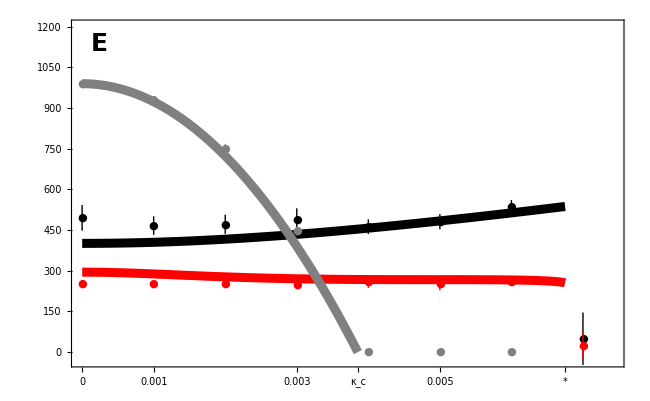

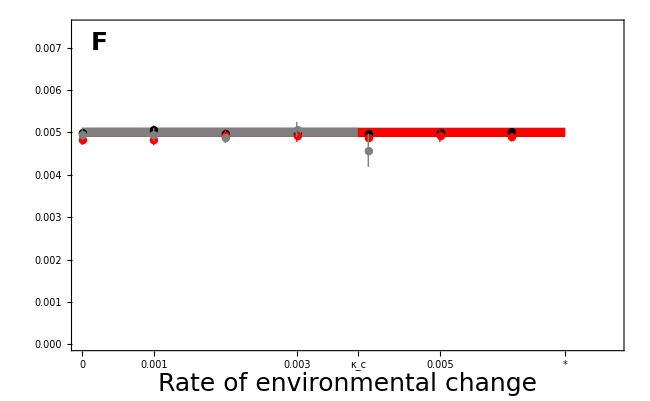

```mathematica
col1=Black;
col2=Gray;
col3=Red;

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;

(*equil genetic variances*)
Vz=2 α^2;
VzP=2 αP^2;

(*max simulations to show*)
maxsimPrey=7;
maxsimPred=7; 
maxsimPreyNoPred=5;

(*x-axis ticks*)
kcPrey=kc;
kcPred=κ->0.00675;
xticks={0,0.001,0.003,0.005,{κ/.kcPrey,Style["κ_c",Gray,LabelSize]},{κ/.kcPred,Style["*",Black,LabelSize]}};
xmax=1.1*κ/.kcPred;

(*simulation results*)
simdir=datadir<>"SPECIALIST/MATCHING/PREDALL/summary/";
summdatPrey=Import[simdir<>"summdataP.dat"];
summdatPred=Import[simdir<>"summdataZ.dat"];

simdirNoPred=datadir<>"SPECIALIST/MATCHING/NOPREDALL/summary/";
summdatPreyNoPred=Import[simdirNoPred<>"summdataP.dat"];

(*plotting lags*)
L1=Plot[L/.FullCoevo,{κ,10^-6,κ/.kcPred},PlotStyle->{col1,Thickness[0.01]}];
L2=Plot[L/.PreyOnlyCoevo,{κ,0,κ/.kcPrey},PlotStyle->{col2,Thickness[0.01]}];
L3=Plot[LP/.FullCoevo,{κ,10^-6,κ/.kcPred},PlotStyle->{col3,Thickness[0.01]}];
(*simulation mean +- 1.96 SE*)
Lsim=ErrorListPlot[Table[{{summdatPrey[[1]][[i]],summdatPrey[[2]][[i]]},ErrorBar[1.96*summdatPrey[[4]][[i]]]},{i,1,maxsimPrey}],PlotMarkers->{Automatic,Large},PlotStyle->col1];
(*simulation mean +- 1.96 SE*)
LPsim=ErrorListPlot[Table[{{summdatPred[[1]][[i]],summdatPred[[2]][[i]]},ErrorBar[1.96*summdatPred[[4]][[i]]]},{i,1,maxsimPred}],PlotMarkers->{Automatic,Large},PlotStyle->col3];
LsimNoPred=ErrorListPlot[Table[{{summdatPreyNoPred[[1]][[i]],summdatPreyNoPred[[2]][[i]]},ErrorBar[1.96*summdatPreyNoPred[[4]][[i]]]},{i,1,maxsimPreyNoPred}],PlotMarkers->{Automatic,Large},PlotStyle->col2];

Legended[
Show[
L1,L2,L3,Lsim,LPsim,LsimNoPred,
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},
ImagePadding->Pad,
PlotRange->{{0,xmax},All},
Axes->False,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
](*,
Placed[
LineLegend[
{Directive[Thickness[0.15],Darker[Blue],Dashing[Medium]],
Directive[Thickness[0.25],Darker[Blue]],
Directive[Thickness[0.25],Darker[Red]]},
{Style["Prey only",LabelSize],
Style["Prey with predator",LabelSize],
Style["Predator",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
]
]*),
Placed[
LineLegend[{
Directive[Gray,Thickness[0.35]]
},
{
Style["Prey without predator",LabelSize,Bold,Gray]
},
LegendLayout->"Row"
],
{0.225,1}
] 
]

Export[imagedir<>"SpecialistEquilibriumLagColor.eps",%];

(*plotting densities*)
D1=Plot[N/.FullCoevo,{κ,10^-6,κ/.kcPred},PlotStyle->{col1,Thickness[0.01]},PlotRange->{0,All}];
D2=Plot[P/.FullCoevo,{κ,10^-6,κ/.kcPred},PlotStyle->{col3,Thickness[0.01]},PlotRange->{0,All}];
D3=Plot[N/.PreyOnlyCoevo,{κ,0,κ/.kcPrey},PlotStyle->{col2,Thickness[0.01]},PlotRange->{0,All}];
(*simulation mean +- 1.96 SE*)
DPreysim=ErrorListPlot[Table[{{summdatPrey[[1]][[i]],summdatPrey[[5]][[i]]},ErrorBar[1.96*summdatPrey[[7]][[i]]]},{i,1,Dimensions[summdatPrey[[2]]][[1]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1];
(*simulation mean +- 1.96 SE*)
DPredsim=ErrorListPlot[Table[{{summdatPred[[1]][[i]],summdatPred[[5]][[i]]},ErrorBar[1.96*summdatPred[[7]][[i]]]},{i,1,Dimensions[summdatPred[[2]]][[1]]}],PlotMarkers->{Automatic,Large},PlotStyle->col3];
DPreysimNoPred=ErrorListPlot[Table[{{summdatPreyNoPred[[1]][[i]],summdatPreyNoPred[[5]][[i]]},ErrorBar[1.96*summdatPreyNoPred[[7]][[i]]]},{i,1,Dimensions[summdatPreyNoPred[[2]]][[1]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2];

Show[
D1,D2,D3,DPreysim,DPredsim,DPreysimNoPred,
Frame->True,
FrameLabel->{Style["",LabelSize],Style[ "",LabelSize]},ImagePadding->Pad,
PlotRange->{{0,xmax},{-30,1.2*Rtot}},
Axes->False,
(*PlotRangePadding->None,*)
FrameStyle->Directive[FontSize->TickSize],
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["E",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

Export[imagedir<>"SpecialistEquilibriumDensityColor.eps",%];

(*simulation mean +- 1.96 SE*)
VPreysim=ErrorListPlot[Table[{{summdatPrey[[1]][[i]],summdatPrey[[8]][[i]]},ErrorBar[1.96*summdatPrey[[10]][[i]]]},{i,1,maxsimPrey}],PlotMarkers->{Automatic,Large},PlotStyle->col1,PlotRange->{0,All},PlotRangeClipping->True];
(*simulation mean +- 1.96 SE*)
VPredsim=ErrorListPlot[Table[{{summdatPred[[1]][[i]],summdatPred[[8]][[i]]},ErrorBar[1.96*summdatPred[[10]][[i]]]},{i,1,maxsimPred}],PlotMarkers->{Automatic,Large},PlotStyle->col3,PlotRange->{0,All}];
VPreysimNoPred=ErrorListPlot[Table[{{summdatPreyNoPred[[1]][[i]],summdatPreyNoPred[[8]][[i]]},ErrorBar[1.96*summdatPreyNoPred[[10]][[i]]]},{i,1,maxsimPreyNoPred}],PlotMarkers->{Automatic,Large},PlotStyle->col2,PlotRange->{0,All},PlotRangeClipping->True];

(*Legended[*)
Show[
{
(*equil variances*)
Plot[Vz,{κ,0,κ/.kcPred},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,κ/.kcPred},PlotStyle->{col3,Thickness[0.01]}],
Plot[VzP,{κ,0,κ/.kcPrey},PlotStyle->{col2,Thickness[0.01]}],
(*simulation results*)
VPreysim,VPredsim,VPreysimNoPred
},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,1.5*Vz}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["F",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["Rate of environmental change",LabelSize],Scaled@xlabpos]
},
PlotRangeClipping->False,
Axes->False
](*,
Placed[
LineLegend[
{Directive[Thickness[0.35],col2],
Directive[Thickness[0.35],col1],
Directive[Thickness[0.25],col3]},
{Style["Prey only",LabelSize],
Style["Prey with predator",LabelSize],
Style["Predator",LabelSize]},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
]
]*)

Export[imagedir<>"SpecialistEquilibriumVarianceColor.eps",%];

Clear[bmax,mmin,Rtot,kmax,e,mP,γ,γk,α,αP,Vz,VzP,maxsimPrey,maxsimPred,kcPrey,kcPred,xticks,xmax,summdatPrey,summdatPred,L1,L2,L3,Lsim,LPsim,D1,D2,D3,D4,DPreysim,DPredsim,VPreysim,VPredsim,simdir,k,col1,col2,col3,maxsimPreyNoPred,VPreysimNoPred,LsimNoPred,DPreysimNoPred]
```

### Evolutionary stability

#### Invasion fitness

In this section we assume monomorphic populations that first reach demographic equilibrium

```mathematica
Clear[dNdtz]
dNdtz[z_,zP_]:=(b[z,N]-m[z,N]-k f[z,zP]P)N;
dPdtzP[z_,zP_]:=(e k f[z,zP]N-mP )P;
FuEq[z_,zP_]:=Solve[{dNdtz[z,zP]==0,dPdtzP[z,zP]==0},{N,P}][[1]]//FullSimplify
```

The invasion fitnesses of a rare prey mutant with trait value zmut and a rare predator mutant with trait value zPmut, in populations of prey and predators with resident traits z and zP, respectively, are

```mathematica
fprey=dNdtz[zmut,zP]/N/.FuEq[z,zP]
```

-mmin+bmax (Rtot+(2 mP)/(e k (-2+(z-zP)^2 γk))-(-2 mmin+2 bmax (Rtot+(2 mP)/(e k (-2+(z-zP)^2 γk)))-γ (z-θ)^2)/(2 (bmax+k)-k (z-zP)^2 γk))-(k (1-1/2 (zmut-zP)^2 γk) (-2 mmin+2 bmax (Rtot+(2 mP)/(e k (-2+(z-zP)^2 γk)))-γ (z-θ)^2))/(2 (bmax+k)-k (z-zP)^2 γk)-1/2 γ (-zmut+θ)^2

```mathematica
fpred=dPdtzP[z,zPmut]/P/.FuEq[z,zP]
```

-mP-(2 mP (1-1/2 (z-zPmut)^2 γk))/(-2+(z-zP)^2 γk)

The selection gradients for prey and predator are then

```mathematica
Dprey=D[fprey,zmut]/.zmut->z//FullSimplify
```

(k (z-zP) γk (-2 mmin+2 bmax (Rtot+(2 mP)/(e k (-2+(z-zP)^2 γk)))-γ (z-θ)^2))/(2 (bmax+k)-k (z-zP)^2 γk)+γ (-z+θ)

```mathematica
Dpred=D[fpred,zPmut]/.zPmut->zP//FullSimplify
```

(2 mP (-z+zP) γk)/(-2+(z-zP)^2 γk)

#### Constant environment

In a constant environment the evolutionary equilibrium is

```mathematica
EqConst=Solve[{Dprey==0,Dpred==0}/.θ->z+L/.zP->z-LP,{L,LP}]
```

{{L→0,LP→0}}

The Jacobian evaluated at this equilibrium is

```mathematica
JacConst=({{D[Vz Dprey,z],D[Vz Dprey,zP]},
{D[VzP Dpred,z],D[VzP Dpred,zP]}}/.θ->z+L/.zP->z-LP/.EqConst)[[1]]
```

{{Vz (-γ+(k (-2 mmin+2 bmax (-mP/(e k)+Rtot)) γk)/(2 (bmax+k))),-(k (-2 mmin+2 bmax (-mP/(e k)+Rtot)) Vz γk)/(2 (bmax+k))},{mP VzP γk,-mP VzP γk}}

The determinant and trace are

```mathematica
detConst=Det[JacConst]//FullSimplify
trConst=Tr[JacConst]//FullSimplify
```

mP Vz VzP γ γk

-Vz γ-((bmax mP+e k (mmin-bmax Rtot)) Vz γk)/(e (bmax+k))-mP VzP γk

The evolutionary equilibrium is convergent stable when the determinant is positive and the trace negative. We can already see that the determinant is positive. To get a better idea about the trace lets substitute in some other variables, giving

```mathematica
Nhat=N/.FuEq[z,zP]/.θ->z+L/.zP->z-LP;
Phat=P/.FuEq[z,zP]/.θ->z+L/.zP->z-LP;
subme=Solve[{(Phat/.EqConst)==P,(Nhat/.EqConst)==N,Rtot==N+P+R},{Rtot,mP,bmax}];
trSimp=Collect[trConst/.subme,{γ,γk},Factor]
```

{-Vz γ-k (-P Vz+e N VzP) γk}

Now we can see that the trace is negative (at the ESS L=LP=0) iff  γ Vz>γk k (P Vz-e N VzP).

Numerical exploration

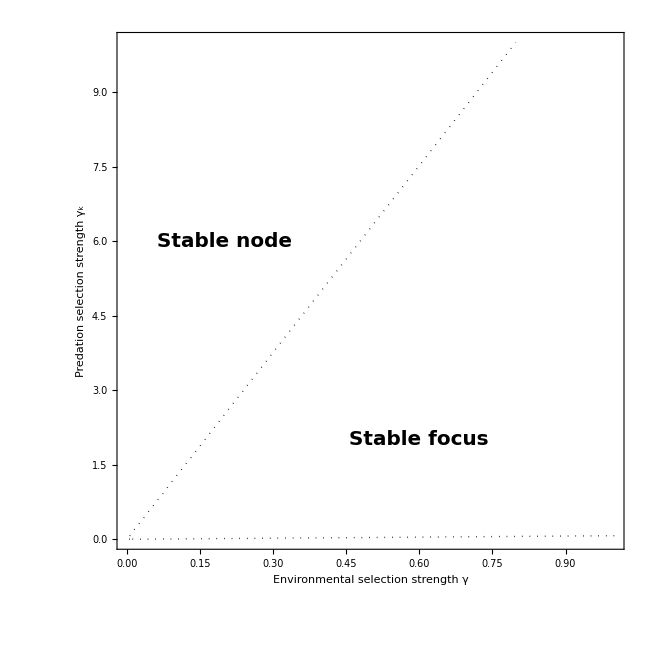

```mathematica
k=0.01;e=1;mP=4;Rtot=1000;mmin=0.1;bmax=0.01;γmax=1;γkmax=10;
α=0.05;αP=0.05;Vz=2 α^2;VzP=2 αP^2;

κ=10^-6;

ContourPlot[
{
trConst==0,
detConst==0,
detConst==trConst^2/4,
0==(trSimp/.FullCoevo/.EqConst)
},
{γ,0,γmax},
{γk,0,γkmax},
PlotPoints->20,
ContourStyle->{
{Thick,Black},
{Thick,Black,Dashed},
{Thick,Black,Dotted},
{Thick,Red,Dotted}
},
Frame->True,
FrameLabel->{
Style["Environmental selection strength γ",LabelSize],
Style["Predation selection strength γ_k",LabelSize]
},
PlotRangePadding->None,
ImageSize->FigureSize,
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
(*Text[Style["Unstable focus",Bold,LetterSize,Black],{0.4,0.4}],*)
Text[Style["Stable focus",Bold,LetterSize,Black],{0.6,2}],
(*Text[Style["Unstable node",Bold,LetterSize,Black],{0.12,0.6}],*)
Text[Style["Stable node",Bold,LetterSize,Black],{0.2,6}]
},
PlotRangeClipping->False
]

(*check requirements for stable node at particular location*)
(*{detConst>0,trConst<0,detConst<trConst^2/4}/.γ->1/.γk->0.0001*)

Clear[e,mP,Rtot,mmin,bmax,Vz,VzP,κ,γmax,γkmax,α,αP,k]
```

#### Changing environment

In a changing environment we need the change in the trait lags to be zero

```mathematica
EqChange=Solve[{κ-Vz Dprey==0,Vz Dprey-VzP Dpred==0}/.θ->z+L/.zP->z-LP,{L,LP}][[3]]//FullSimplify
```

{L→1/(2 e k Vz VzP γ γk κ)(e (bmax+2 k) mP Vz VzP^2 γ γk+bmax e Vz VzP γ √(γk (mP^2 VzP^2 γk+2 κ^2))-√(e Vz VzP γ (e Vz VzP γ ((bmax+2 k) mP VzP γk+bmax √(γk (mP^2 VzP^2 γk+2 κ^2)))^2-4 k γk κ^2 (bmax Vz (mP VzP γk+√(γk (mP^2 VzP^2 γk+2 κ^2)))+e VzP (2 k (mmin Vz-bmax Rtot Vz+mP VzP) γk+bmax (mP VzP γk+√(γk (mP^2 VzP^2 γk+2 κ^2)))))))),LP→(-mP VzP γk+√(γk (mP^2 VzP^2 γk+2 κ^2)))/(γk κ)}

The Jacobian is

```mathematica
JacChange={{D[κ-Vz Dprey/.θ->z+L/.zP->z-LP,L],D[κ-Vz Dprey/.θ->z+L/.zP->z-LP,LP]},{D[Vz Dprey-VzP Dpred/.θ->z+L/.zP->z-LP,L],D[Vz Dprey-VzP Dpred/.θ->z+L/.zP->z-LP,LP]}};
```

The determinant is

```mathematica
detChange=Det[JacChange]//FullSimplify
```

(2 mP Vz VzP γ γk (2+LP^2 γk) (-2 (bmax+k)+k LP (2 L+LP) γk))/((-2+LP^2 γk)^2 (-2 (bmax+k)+k LP^2 γk))

We have previously assumed selection to be effectively weak enough such that k(1 - γk/2 LP^2)> 0, and so for the determinant to be positive we need
2 (b + kmax) > k LP (2 L + LP) γk.

The trace is

```mathematica
trChange=Tr[JacChange]//FullSimplify
```

-(4 LP^2 mP VzP γk^2)/((-2+LP^2 γk)^2)+(2 mP VzP γk)/(-2+LP^2 γk)+Vz γ (-1+(2 k L LP γk)/(2 (bmax+k)-k LP^2 γk))+(Vz γk (-k^2 (2 mmin+L^2 γ) (2+LP^2 γk)+(4 bmax^2 (e k Rtot (-2+LP^2 γk)^2-2 mP (2+LP^2 γk)))/(e (-2+LP^2 γk)^2)+2 bmax k (-2 mmin-L^2 γ+k Rtot (2+LP^2 γk)+(2 mP (3+8/(-2+LP^2 γk)))/e)))/((-2 (bmax+k)+k LP^2 γk)^2)

Assuming weak selection this is approximately

```mathematica
trChangeApp=Normal[Series[ trChange/.γk->γk ϵ/.γ->γ ϵ,{ϵ,0,1}]]/.ϵ->1//FullSimplify
```

-Vz γ-((bmax mP+e k (mmin-bmax Rtot)) Vz γk)/(e (bmax+k))-mP VzP γk

Simplifying by substituting in densities, with weak selection the trace is

```mathematica
tr0=Collect[trChangeApp/.subme,{γ,γk},Factor]
```

{-Vz γ-k (-P Vz+e N VzP) γk}

Which is the same condition as in the constant environment (now with potentially non-zero lags).

Our conditions are then

```mathematica
trChangeEq=trChange/.FullCoevo/.EqChange;
detChangeEq=detChange/.FullCoevo/.EqChange;
ChangeTr0=tr0/.FullCoevo/.EqChange;
```

Numerical exploration (with blue area giving parameter values that produce a stable node)

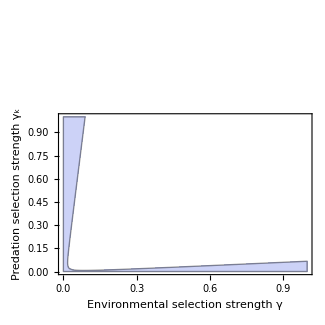
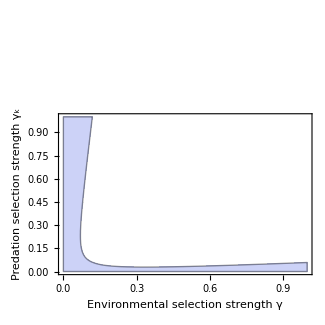
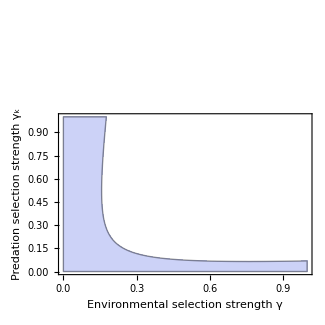
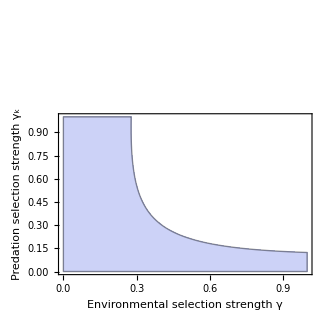
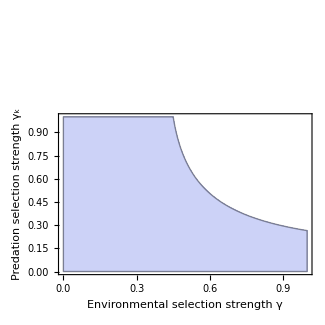
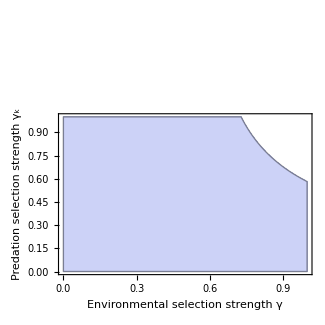

```mathematica
k=0.01;e=1;mP=4;Rtot=1000;mmin=0.1;bmax=0.01;γmax=1;γkmax=1;
α=0.05;αP=0.05;Vz=2 α^2;VzP=2 αP^2;

Table[
RegionPlot[
{
Re[trChangeEq]<0&&Re[detChangeEq]>0&&Re[detChangeEq]<Re[trChangeEq]^2/4(*&&0<Re[P/.FullCoevo]&&0>(N/.PreyOnlyCoevo)*)
},
{γ,0,γmax},
{γk,0,γkmax},
(*PlotPoints->20,*)
(*ContourStyle->{
{Thick,Black},
{Thick,Black,Dashed},
{Thick,Black,Dotted},
{Thick,Red,Dashed}
},*)
Frame->True,
FrameLabel->{
Style["Environmental selection strength γ",LabelSize/2],
Style["Predation selection strength γ_k",LabelSize/2]
},
PlotRangePadding->None,
ImageSize->FigureSize/2,
FrameStyle->Directive[FontSize->TickSize],
Epilog->{
(*Text[Style["Unstable focus",Bold,LetterSize,Black],{0.4,0.8}],*)
Text[Style["Stable focus",Bold,LetterSize,Black],{0.6,2}],
Text[Style["Stable node",Bold,LetterSize,Black],{0.2,6}]
}
],
{κ,Table[i/1000,{i,1,6}]}
]

(*check requirements for stable node at particular location*)
(*{detChangeEq>0,trChangeEq<0,detChangeEq<trChangeEq^2/4}/.γ->0.001/.γk->0.1*)

Clear[e,mP,Rtot,mmin,bmax,Vz,VzP,κ,γmax,γkmax,α,αP,k]
```

Notice that as the rate of environmental change increases, the parameter space giving non-cyclic dynamics increases.

## Specialist example 1B: selective push (predate maladapted more)

### Model set-up

Here we examine a model where prey are born at a per capita rate

```mathematica
b[z_,zP_,N_,P_]:=bmax (Rtot-N-P)
```

With a normal prey trait distribution p with variance Vz and mean barz, the mean birth rate of the prey is

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)];
barb=Integrate[b[z,zP,N,P]p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]
```

-bmax (N+P-Rtot)

Let per capita prey mortality m be

```mathematica
m[z_,zP_,N_,P_]:=mmin+γ(θ-z)^2
```

giving population mean

```mathematica
barm=Integrate[m[z,zP,N,P]p[z],{z,-∞,∞},Assumptions->Vz>0]
```

mmin+γ (Vz+(barz-θ)^2)

Let the per prey per predator predation rate k f be

```mathematica
f[z_,zP_,N_,P_]:=(1+γk(z-θ)^2)
```

With a normal predator trait distribution pP with variance VzP and mean barzP, mean per prey per predator predation rate is

```mathematica
pP[zP_]:=1/Sqrt[2π VzP] Exp[(-(barzP-zP)^2)/(2VzP)];
barkf=Integrate[k f[z,zP,N,P]p[z]pP[zP],{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]
```

k (1+γk (Vz+(barz-θ)^2))

Prey population growth rate is

```mathematica
Integrate[p[z]pP[zP](b[z,zP,N,P]-m[z,zP,N,P]-k f[z,zP,N,P]P)N,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0,γ>0}]//FullSimplify;
dNdt=Collect[%,bmax,Simplify]//FullSimplify
```

-bmax N (N+P-Rtot)-N (mmin+k P (1+γk (Vz+(barz-θ)^2))+γ (Vz+(barz-θ)^2))

Predator population growth rate is

```mathematica
dPdt=Integrate[p[z]pP[zP](e k f[z,zP,N,P]N-mP )P,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]//Simplify
```

P (-mP+e k N (1+γk (Vz+(barz-θ)^2)))

where e is the conversion efficiency and mP is the per capita rate of predator mortality.

### Rates of evolution and equilibrium phenotypic variances

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

PREY BIRTH

Given a prey individual is chosen to give birth, the probability it has trait value zParent is

```mathematica
pzbirth=(b[zParent,zP,N,P]p[zParent])/barb//Factor;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zParent]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zParent, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zParent,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected mean prey trait after a prey birth is then

```mathematica
meanafterpreybirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected variance in prey traits after a prey birth is

```mathematica
varafterpreybirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

PREDATOR BIRTH

Given a predator captures a prey, the probability the predator has trait value zC is

```mathematica
pcapture=Integrate[pP[zC]k f[z,zC,N,P]p[z],{z,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

To get an offspring with trait value zZPwe need a particular mate and then the appropriate random effect. This happens with probability

```mathematica
ppredmate=Integrate[pP[2(zP-ξ)-zC]u[ξ],{ξ,-∞,∞},Assumptions->{α>0,VzP>0}];
```

This can happen for any zC, in either order (the other parent could be chosen to give birth), so the probability, given a predator is born due to a predation event, that the new predator has trait value zP is

```mathematica
ppredbirth=2Integrate[pcapture*ppredmate,{zC,-∞,∞},Assumptions->{α>0,VzP>0}];
```

The expected trait mean after a predation birth is thus

```mathematica
meanafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(meanb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

The expected trait variance after a predation birth is

```mathematica
varafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(varb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

#### Death

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

PREY DEATH

Given a prey dies of background mortality, the probability the dead individual has trait value z is

```mathematica
penvdeath=(p[z]m[z,zP,N,P])/barm;
```

After such a death the expected trait mean is

```mathematica
meanafterenvdeath=Simplify[Integrate[Factor[meand*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

After such a death the trait variance is

```mathematica
varafterenvdeath=Simplify[Integrate[Factor[vard*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

PREDATION

Given a prey is killed by a predator, the probability the dead prey has trait value z is

```mathematica
pcaught=Integrate[p[z]k f[z,zP,N,P]pP[zP],{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

After such a death the expected trait mean is

```mathematica
meanafterpredation=Simplify[Integrate[Factor[pcaught*meand],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

After such a death the expected variance is

```mathematica
varafterpredation=Simplify[Integrate[Factor[pcaught*vard],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

PREDATOR DEATH

After a predator death (random) the expected trait mean is

```mathematica
meanafterpreddeath=Simplify[Integrate[Factor[pP[zP](meand/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{VzP>0,α>0}];
```

After a predator death the expected variance is

```mathematica
varafterpreddeath=Simplify[Integrate[Factor[pP[zP](vard/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{VzP>0,α>0}];
```

#### Rate of prey evolution

Expected prey mean after short time Δt

```mathematica
Ebarzdt=(1-Δt N (barb+barm+ barkf P))barz+Δt N(barb meanafterpreybirth+barm* meanafterenvdeath+barkf P* meanafterpredation);
```

The change in the mean is then

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp=Collect[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,{k,bmax},Simplify]
```

2 Vz γ (-barz+θ)+2 k P Vz γk (-barz+θ)

#### Rate of predator evolution

Expected mean after short time Δt

```mathematica
EbarzPdt=(1-Δt P ( e barkf N+mP))barzP+Δt P( e barkf N* meanafterpredbirth+ mP meanafterpreddeath);
```

The change in the mean is then

```mathematica
dbarzPdt=Limit[(EbarzPdt-barzP)/Δt,Δt->0];
```

To zeroth order in 1/P this is

```mathematica
dbarzPdtApp=Normal[Series[dbarzPdt/.P->P/ϵ,{ϵ,0,1}]]/.ϵ->1//FullSimplify
```

0

(the predator doesn’t evolve because no rate depends on its trait value)

#### Prey equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+ barkf P))Vz+Δt N(barb varafterpreybirth+ barm *varafterenvdeath+ barkf P * varafterpredation);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0]//FullSimplify;
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Collect[Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1/.barz->L+θ/.Rtot->R+P+N,{bmax,R},FullSimplify]
```

bmax (2 α^2+R (-Vz/2+α^2))-2 Vz^2 (γ+k P γk)

Then with weak selection and a small variance, to second order this is

```mathematica
Normal[Series[dVdtApp/.γ->γ ϵ/.α^2->α^2 ϵ/.Vz->Vz ϵ,{ϵ,0,2}]]/.ϵ->1//Simplify
```

bmax (2 α^2+R (-Vz/2+α^2))-2 k P Vz^2 γk

Finally, when there are lots of free resources

```mathematica
Normal[Series[%/.R->R/ ϵ,{ϵ,0,-1}]]/.ϵ->1//Simplify
```

-1/2 bmax R (Vz-2 α^2)

and the equilibrium variance is

```mathematica
Solve[%==0,Vz]
```

{{Vz→2 α^2}}

#### Predator equilibrium variance

The expected variance after a small time Δt is

```mathematica
EvarPdt=(1-Δt P (e barkf N+ mP))VzP+Δt P( e barkf N* varafterpredbirth+m varafterpreddeath);
```

The rate of change in variance is thus

```mathematica
dVPdt=Limit[(EvarPdt-VzP)/Δt/.m->mP,Δt->0]//FullSimplify;
```

To zeroth order in 1/P this is

```mathematica
dVPdtApp=Normal[Series[dVPdt/.P->P/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

-1/2 e k N (VzP-2 α^2) (1+γk (Vz+(barz-θ)^2))

And at equilibrium we have

```mathematica
Series[VzP/.Solve[0==dVPdtApp,VzP],{α,0,3}]
```

{2 α^2+O[α]^4}

### Quick [for section immediately below only]

```mathematica
dNdt=-bmax N (N+P-Rtot)-N (mmin+k P (1+γk (Vz+(barz-θ)^2))+γ (Vz+(barz-θ)^2));
```

```mathematica
dPdt=P (-mP+e k N (1+γk (Vz+(barz-θ)^2)));
```

```mathematica
dbarzdtApp=2 Vz γ (-barz+θ)+2 k P Vz γk (-barz+θ);
```

### Steady-state and critical rates of environmental change

Steady-state lag and equilibrium densities

```mathematica
FindEq=Solve[{dNdt==0,dPdt==0,dbarzdtApp==κ}/.barz->θ-L//Simplify,{P,N,L}];
```

Prey-only equilibrium

```mathematica
PreyOnlyEq=FindEq[[2]];
```

Prey and predator equilibrium

```mathematica
PreyPredEq=FindEq[[5]];
```

The critical rate of environmental change for the prey is

```mathematica
κ2/.Solve[0==N/.PreyOnlyEq/.κ->κ2^(1/2),κ2]//Flatten;
kc=κ->Simplify[Sqrt[%],{Vz>0,γ>0,mmin-bmax Rtot+Vz γ<0}][[1]]
```

κ→2 Vz √(-γ (mmin-bmax Rtot+Vz γ))

The critical rate of change for the predator is harder to solve for directly

```mathematica
(*Solve[0==P/.PreyPredEq,κ]*)
```

But we can show that the prey and predator’s densities can be positive at the coexistence equilibrium when the prey-only density is negative

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
e=1/4;mP=1;k=1/100;
γk=1/10;
κ =1/100;

N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

-10.05

214.854

240.754

implying that the specialist predator can help the prey persist in this case.

We can look at this more generally by noting that the equilibrium predator density is

```mathematica
peq=Solve[0==FullSimplify[dNdt/N/.barz->θ-L],P]//Flatten
```

{P→(-mmin-bmax N+bmax Rtot-L^2 γ-Vz γ)/(bmax+k+k L^2 γk+k Vz γk)}

and the equilibrium prey density in the absence of predators is

```mathematica
neq=Solve[0==FullSimplify[dNdt/N/.barz->θ-L/.P->0],N]//Flatten
```

{N→(-mmin+bmax Rtot-L^2 γ-Vz γ)/bmax}

The lags in the two cases (with and without predators) can be different, so call LP the lag with the predator

```mathematica
pEq=P/.peq/.L->LP
```

(-mmin-bmax N+bmax Rtot-LP^2 γ-Vz γ)/(bmax+k+k LP^2 γk+k Vz γk)

and L the lag without the predator

```mathematica
nEq=N/.neq
```

(-mmin+bmax Rtot-L^2 γ-Vz γ)/bmax

Then the condition for the predator helping prey persist is

```mathematica
Reduce[pEq>0&&nEq<0&&bmax>0&&mmin>0&&N>0&&Rtot>0&&γ>0&&Vz>0&&k>0&&γk>0&&bmax Rtot>mmin+Vz γ&&L>√((-mmin+bmax Rtot-Vz γ)/γ)&&N<(-mmin+bmax Rtot-Vz γ)/bmax,Reals]
```

γ>0&&Vz>0&&Rtot>0&&bmax>(Vz γ)/Rtot&&0<mmin<bmax Rtot-Vz γ&&L>√((-mmin+bmax Rtot-Vz γ)/γ)&&0<N<(-mmin+bmax Rtot-Vz γ)/bmax&&-√((-mmin-bmax N+bmax Rtot-Vz γ)/γ)<LP<√((-mmin-bmax N+bmax Rtot-Vz γ)/γ)&&γk>0&&k>0

The L inequality (note that L>0) just says that we need to be past the critical rate of change for the prey (so that N<0 without predators)

```mathematica
Solve[L==√((-mmin+bmax Rtot-Vz γ)/γ)/.PreyOnlyEq,κ]//Flatten
```

{κ→2 Vz γ √((-mmin+bmax Rtot-Vz γ)/γ)}

The N inequality just says that the density of prey with predators should be less than the density of perfectly adapted prey without predators (which is always true without Abram’s ecological hydra effect; Abrams, P. 2009. When does greater mortality increase population size? The long history and diverse mechanisms underlying the hydra effect. Ecology Letters 12:462–74.)

```mathematica
N/.PreyOnlyEq/.κ->0//Simplify
```

-(mmin-bmax Rtot+Vz γ)/bmax

And so we are left with the LP condition, meaning that predators can only help prey persist when they reduce the prey’s lag enough to allow it to grow in the absence of predators (giving the predator something to eat)

```mathematica
Solve[0==dNdt/N/.barz->θ-L/.P->0//Simplify,L]//Flatten
```

{L→-(√(-mmin-bmax N+bmax Rtot-Vz γ))/(√γ),L→(√(-mmin-bmax N+bmax Rtot-Vz γ))/(√γ)}

### Temporal dynamics (with simulation results)

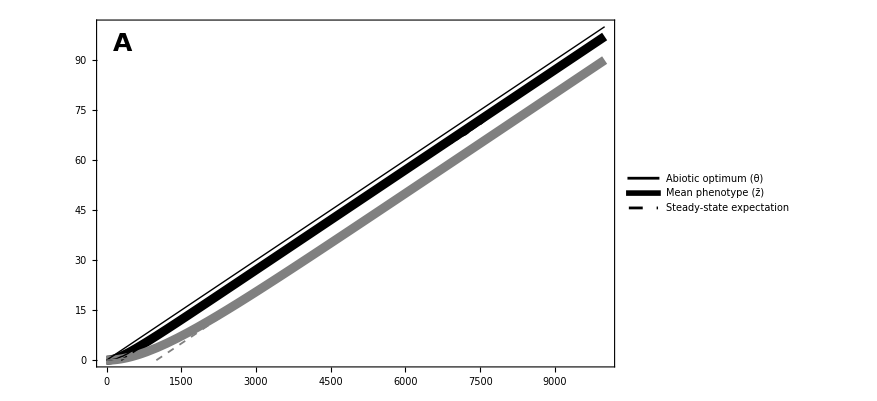

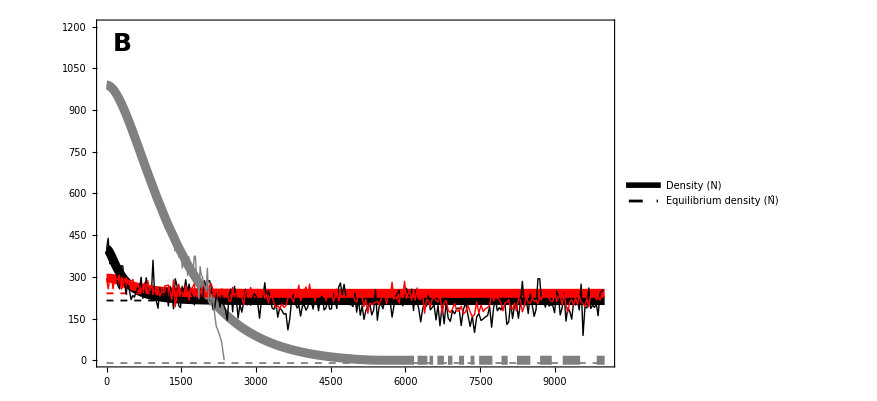

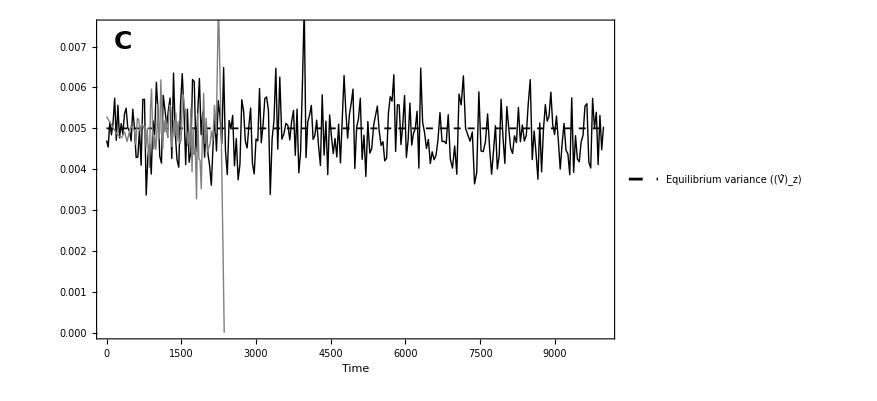

```mathematica
(*plotting colors*)
col1=Black;
col2=Gray;
col3=Red;

(*simulation results*)
rep="1";
simdir=datadir<>"SPECIALIST/PUSH/";
zpdat=Import[simdir<>"zp_k1_r"<>rep<>".dat","CSV"];
Pdat = Import[simdir<>"P_k1_r"<>rep<>".dat"];
Zdat = Import[simdir<>"Z_k1_r"<>rep<>".dat"];
simdir2=datadir<>"SPECIALIST/PUSH/NOPRED/";
zpdat2=Import[simdir2<>"zp_k1_r"<>rep<>".dat","CSV"];
Pdat2 = Import[simdir2<>"P_k1_r"<>rep<>".dat"];

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/10;α=1/20;
e=1/4;mP=1;k=1/100;
γk=1/10;
κ =1/100;
tmax=10000;

(*initial conditions*)
z0=0;n0=mP/(e k);p0=(bmax (Rtot - n0)-mmin)/(bmax+k);

(*phenotypic variance*)
Vz=2 α^2 ; 

(*numerically solve coupled equation*)
cosol=NDSolve[{
z'[t]==(dbarzdtApp/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
z[0]==z0,
n[0]==n0,
P[0]==p0
},{z,n,P},{t,0,tmax}];

preysol=NDSolve[{
z'[t]==(dbarzdtApp/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
z[0]==z0,
n[0]==Rtot-mmin/bmax,
P[0]==0
},{z,n,P},{t,0,tmax}];

(*plot lag and optimal*)
zPlo=Plot[Evaluate[z[t]/.cosol],{t,0,tmax},PlotStyle->{col1,Thickness[0.01]}];
zPloPO=Plot[Evaluate[z[t]/.preysol],{t,0,tmax},PlotStyle->{col2,Thickness[0.01]}];
opt=Plot[κ t,{t,0,tmax},PlotStyle->{Black,Thick}];
(*plot predicted lag*)
predz=Plot[κ t-L/.PreyPredEq,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed},PlotRange->{0,All}];
predzPO=Plot[κ t-L/.PreyOnlyEq,{t,0,tmax},PlotStyle->{col2,Thickness[0.002],Dashed},PlotRange->{0,All}];
(*plot simulation results*)
zdat=ListPlot[Table[{Pdat[[i,1]],zpdat[[i,1]]},{i,1,Dimensions[Pdat][[1]],1}],PlotRange->All,PlotStyle->col1, Joined->True];
zdat2=ListPlot[Table[{Pdat2[[i,1]],zpdat2[[i,1]]},{i,1,Dimensions[Pdat2][[1]],1}],PlotRange->All,PlotStyle->col2, Joined->True];

Legended[
Show[
{zPlo,zPloPO,predz,predzPO,opt,zdat,zdat2},
PlotRange->{{0,tmax},{0,All}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotype (z̄)",LabelSize],
Style["Steady-state expectation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.725}
] 
]

(*Export[imagedir<>"GeneralistTemporalTrait.eps",%];*)

(*plot abundance*)
nPlot=Plot[Evaluate[n[t]/.cosol],{t,0,tmax},PlotStyle->{col1,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];
nPlotPO=Plot[Evaluate[n[t]/.preysol],{t,0,tmax},PlotStyle->{col2,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];pPlot=Plot[Evaluate[P[t]/.cosol],{t,0,tmax},PlotStyle->{col3,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];
(*plot predicted abundance*)
predn=Plot[N/.PreyPredEq,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed}];
prednPO=Plot[N/.PreyOnlyEq,{t,0,tmax},PlotStyle->{col2,Thickness[0.002],Dashed}];
predp=Plot[P/.PreyPredEq,{t,0,tmax},PlotStyle->{col3,Thickness[0.002],Dashed}];
(*plot simulation results*)
ndat=ListPlot[Table[Pdat[[i]],{i,1,Dimensions[Pdat][[1]],1}],Joined->True,PlotStyle->col1];
pdat2=ListPlot[Table[Pdat2[[i]],{i,1,Dimensions[Pdat2][[1]],1}],Joined->True,PlotStyle->col2];
pdat=ListPlot[Table[Zdat[[i]],{i,1,Dimensions[Zdat][[1]],1}],Joined->True,PlotStyle->col3];

Legended[
Show[
{nPlot,nPlotPO,pPlot,predn,prednPO,predp,ndat,pdat,pdat2},
PlotRange->{{0,tmax},{0,Rtot*1.2}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Density (N)",LabelSize],
Style["Equilibrium density (N̂)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.7}
]
]

(*Export[imagedir<>"GeneralistTemporalDensity.eps",%];*)

(*plot equilibrium variance*)
eqvarPlot=Plot[Vz,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed}];
(*plot simulation results*)
simvarPlot=ListPlot[Table[{Pdat[[i,1]],zpdat[[i,2]]},{i,1,Dimensions[Pdat][[1]],1}],PlotStyle->col1,Joined->True];
simvarPlot2=ListPlot[Table[{Pdat2[[i,1]],zpdat2[[i,2]]},{i,1,Dimensions[Pdat2][[1]],1}],PlotStyle->col2,Joined->True];

Legended[
Show[
{eqvarPlot,simvarPlot,simvarPlot2},
Frame->True, 
FrameLabel->{Style["Time",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,tmax},{0,1.5*Vz}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Black,Thickness[0.1],Dashed]
},
{
(*Style["Mean genetic variance (((σ̄)_(g,P))^2)",LabelSize],*)
Style["Equilibrium variance ((V̂)_z)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.675,0.2}
]
]

(*Export[imagedir<>"GeneralistTemporalVariance.eps",%];*)

Clear[simdir,simdir2,knum,rep,zpdat,zpdat2,Pdat,Pdat2,bmax,mconst,Rtot,γ,α,Vz,tmax,z0,n0,κ,cosol,cosolc1,zPlo,zPloc1,opt,predz,predzc1,zdat,zdat2,pPlot,pPlotc1,predp,predpc1,pdat,pdat2,eqvarPlot,simvarPlot,simvarPlot2,c0,c1,col1,col2,konst,eqvarPlot2,e,k,mP,Zdat,p0,γk,mmin,col3,preysol,nPlot,nPlotPO,predn,prednPO,ndat,zPloPO,predzPO]
```

### Equilibrium solutions

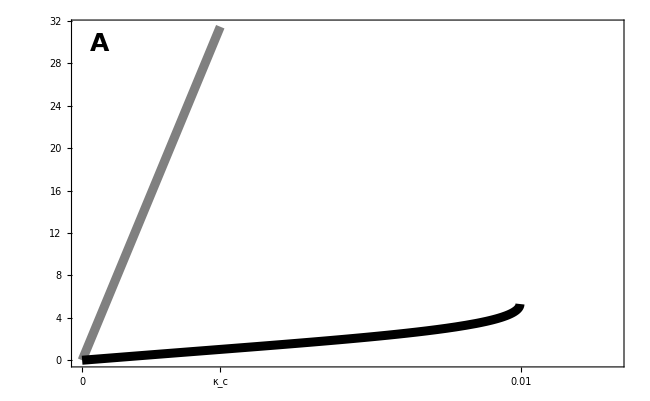

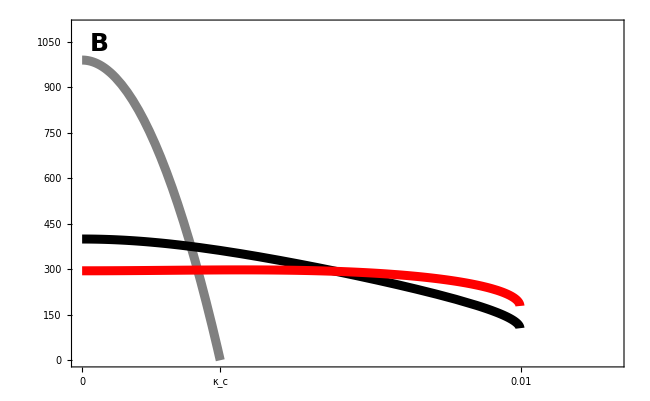

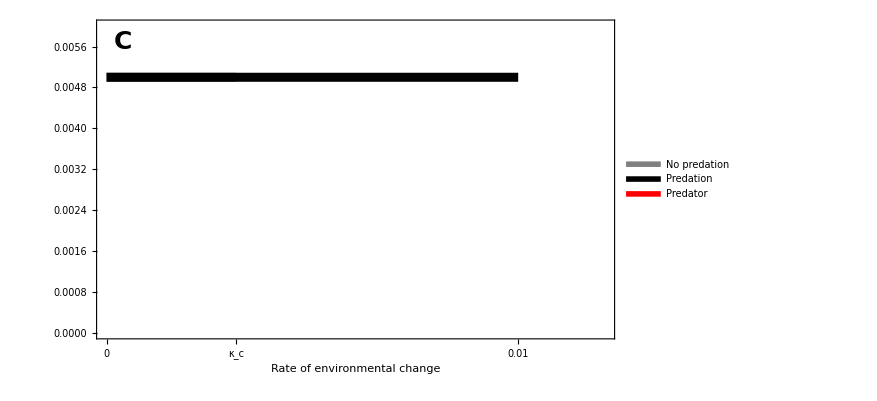

```mathematica
(*plotting colors*)
col1=Gray;
col2=Black;

(*simulation results*)
simdir=datadir<>"PUSH/CEQUALS0/Summary/";
(*simdir2=datadir<>"PUSHB/Summary/";*)
summdata=Import[simdir<>"summdata.dat"];
(*summdata2=Import[simdir2<>"summdata.dat"];*)

(*parameters*)
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/100;α=1/20;
γk=1/10;
e=1/4;mP=1;k=1/100;
 
(*equilibrium variance*)
Vz=2 α^2;

kcp=κ->0.011;

(*x-axis limit*)
xmax=1.1*κ/.kcp;
(*x-axis ticks*)
xnum=5;
xticks={0,0.01,0.02,{κ/.kc,Style["κ_c",col1,FontSize->TickSize]}(*,{κ/.kcp,Style["κ_cP",col2,FontSize->TickSize]}*)};
(*max number of simulations to show*)
numsims=7;
numsims2=8;

Show[{
(*predicted lag*)
Plot[L/.PreyOnlyEq,{κ,0,κ/.kc},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}, Axes->False],
Plot[L/.PreyPredEq,{κ,0,κ/.kcp},PlotStyle->{Thickness[0.01],col2},PlotRange->All]
(*observed lag +- 1.96 SE*)
(*ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[2]][[i]]},ErrorBar[1.96*summdata[[4]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[2]][[i]]},ErrorBar[1.96*summdata2[[4]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2]*)
},
PlotRange->{{0,xmax},All},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{All,All},{xticks,All}},
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumLag.eps",%];*)

Show[{
(*predicted density*)
Plot[N/.PreyOnlyEq,{κ,0,2κ/.kc},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[N/.PreyPredEq,{κ,0,2κ/.kcp},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
Plot[P/.PreyPredEq,{κ,0,2κ/.kcp},PlotStyle->{Thickness[0.01],Red},PlotRange->{0,All}]
(*observed density +- 1.96 SE*)
(*ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[5]][[i]]},ErrorBar[1.96*summdata[[7]][[i]]]},{i,1,Dimensions[summdata][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[5]][[i]]},ErrorBar[1.96*summdata2[[7]][[i]]]},{i,1,Dimensions[summdata2][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2]*)
},
PlotRange->{{0,xmax},{0,Rtot*1.1}},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumDensity.eps",%];*)

Legended[
Show[{
(*predicted variance*)
Plot[Vz,{κ,0,κ/.kc},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,0.01},PlotStyle->{col2,Thickness[0.01]}]
(*observed variance +- 1.96 SE*)
(*ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[8]][[i]]},ErrorBar[1.96*summdata[[10]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1,Axes->False]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[8]][[i]]},ErrorBar[1.96*summdata2[[10]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2,Axes->False]*)
},
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,0.006}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]],
Directive[Red,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize],
Style["Predator",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumVariance.eps",%];*)

Clear[simdir,simdir2,summdata,summdata2,bmax,mmin,Rtot,γ,γk,α,Vz,xmax,xticks,numsims,numsims2,k,e,mP,xnum,col1,col2]
```

## Specialist example 2: evolutionary hydra effect (continuous breeding)

### Model set-up

Here we examine a model where prey are born at a per capita rate

```mathematica
b[z_,zP_,N_,P_]:=bmax Exp[-γ/2 (θ-z)^2](Rtot-N-P)
```

where bmax is the maximum per capita, per available resource birth rate, Rtot is the total density of resource in the closed system, N is the density of the prey, and P is the density of the predator. Prey with trait values z closest to the optimum θ have the highest birth rates, and this declines at a rate dependent on the strength of selection γ.

With a normal prey trait distribution p with variance Vz and mean barz, the mean birth rate of the prey is

```mathematica
p[z_]:=1/Sqrt[2π Vz] Exp[(-(barz-z)^2)/(2Vz)];
barb=Integrate[b[z,zP,N,P]p[z],{z,-∞,∞},Assumptions->{Vz>0,γ>0}]
```

-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (N+P-Rtot))/(√(1+Vz γ))

Let per capita prey mortality m be constant

```mathematica
m[z_,zP_,N_,P_]:=mconst
```

giving mean

```mathematica
barm=Integrate[m[z,zP,N,P]p[z],{z,-∞,∞},Assumptions->Vz>0]
```

mconst

Let the per prey per predator predation rate be k f with

```mathematica
f[z_,zP_,N_,P_]:=1
```

With a normal predator trait distribution pP with variance VzP and mean barzP, mean per prey per predator predation rate is

```mathematica
pP[zP_]:=1/Sqrt[2π VzP] Exp[(-(barzP-zP)^2)/(2VzP)];
barkf=Integrate[k f[z,zP,N,P]p[z]pP[zP],{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]
```

k

Prey population growth rate is then

```mathematica
Integrate[p[z]pP[zP](b[z,zP,N,P]-m[z,zP,N,P]-k f[z,zP,N,P]P)N,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0,γ>0}]//FullSimplify;
dNdt=Collect[%,bmax,Simplify]//FullSimplify
```

-N (mconst+k P)-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (N+P-Rtot) √(Vz/(1+Vz γ)))/(√Vz)

Predator population growth rate is

```mathematica
dPdt=Integrate[p[z]pP[zP](e k f[z,zP,N,P]N-mP )P,{z,-∞,∞},{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]//Simplify
```

-mP P+e k N P

where e is the conversion efficiency and mP is the per capita rate of predator mortality.

### Rates of evolution and equilibrium phenotypic variances

This section follows the logic of Debarre & Otto 2016. Evolutionary dynamics of a quantitative trait in a finite asexual population. Theoretical Population Biology 108:75-88 to derive the rate of evolution in the mean trait value and find the equilibrium phenotypic variance in a sexually reproducing population.

#### Birth

When an offspring with trait value z is born the mean trait value becomes

```mathematica
meanb=N/(N+1)barz+1/(N+1)z;
```

and the expected squared trait value becomes

```mathematica
expsq0=Simplify[Integrate[z^2 p[z],{z,-∞,∞}],{Vz>0}];
expsqb=N/(N+1)expsq0+1/(N+1)z^2;
```

Given an offspring with trait value z is born the variance becomes

```mathematica
varb=expsqb-meanb^2;
```

PREY BIRTH

Given a prey individual is chosen to give birth, the probability it has trait value zParent is

```mathematica
pzbirth=(b[zParent,zP,N,P]p[zParent])/barb//Factor;
```

To get an offspring with trait value z we need a particular mate and then the appropriate mutation. This happens with probability

```mathematica
u[ξ_]:=PDF[NormalDistribution[0,α],ξ]
ppreymate=Integrate[p[2(z-ξ)-zParent]u[ξ],{ξ,-∞,∞},Assumptions->{Vz>0,α>0}];
```

where ξ is the segregation factor (mimicking the effect of mutation, recombination, and segregation between a large number of small effect loci), which is pulled from a random normal distribution with mean 0 and variance α^2.

This can happen for any zParent, in either order (the other parent could be chosen to give birth), so the probability, given a prey is born, that the new prey has trait value z is

```mathematica
ppreybirth=2Integrate[pzbirth*ppreymate,{zParent,-∞,∞},Assumptions->{Vz>0,α>0,γ>0}];
```

The expected mean prey trait after a prey birth is then

```mathematica
meanafterpreybirth=Simplify[Integrate[Factor[meanb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

The expected variance in prey traits after a prey birth is

```mathematica
varafterpreybirth=Simplify[Integrate[Factor[varb*ppreybirth],{z,-∞,∞}],{Vz>0,α>0,γ>0}];
```

PREDATOR BIRTH

Given a predator captures a prey, the probability the predator has trait value zC is

```mathematica
pcapture=Integrate[pP[zC]k f[z,zC,N,P]p[z],{z,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

To get an offspring with trait value zZPwe need to choose a second parent and then the appropriate random effect. This happens with probability

```mathematica
ppredmate=Integrate[pP[2(zP-ξ)-zC]u[ξ],{ξ,-∞,∞},Assumptions->{α>0,VzP>0}];
```

This can happen for any zC, in either order (the other parent could be chosen to give birth), so the probability, given a predator is born due to a predation event, that the new predator has trait value zP is

```mathematica
ppredbirth=2Integrate[pcapture*ppredmate,{zC,-∞,∞},Assumptions->{α>0,VzP>0}];
```

The expected trait mean after a predation birth is thus

```mathematica
meanafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(meanb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

The expected trait variance after a predation birth is

```mathematica
varafterpredbirth=Simplify[Integrate[Factor[ppredbirth*(varb/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

#### Death

When an individual with trait value z dies the mean trait value becomes

```mathematica
meand=N/(N-1)barz-1/(N-1)z;
```

The expected squared trait value becomes

```mathematica
expsqd=N/(N-1)expsq0-1/(N-1)z^2;
```

Given an individual with trait value z died, the variance becomes

```mathematica
vard=expsqd-meand^2;
```

PREY DEATH

Given a prey dies of natural mortality, the probability the dead individual has trait value z is

```mathematica
penvdeath=(p[z]m[z,zP,N,P])/barm;
```

After such a death the expected trait mean is

```mathematica
meanafterenvdeath=Simplify[Integrate[Factor[meand*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

After such a death the trait variance is

```mathematica
varafterenvdeath=Simplify[Integrate[Factor[vard*penvdeath],{z,-∞,∞}],{Vz>0,α>0}];
```

PREDATION

Given a prey is killed by a predator, the probability the dead prey has trait value z is

```mathematica
pcaught=Integrate[p[z]k f[z,zP,N,P]pP[zP],{zP,-∞,∞},Assumptions->{Vz>0,VzP>0}]/barkf;
```

After such a death the expected trait mean is

```mathematica
meanafterpredation=Simplify[Integrate[Factor[pcaught*meand],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

After such a death the expected variance is

```mathematica
varafterpredation=Simplify[Integrate[Factor[pcaught*vard],{z,-∞,∞}],{Vz>0,VzP>0,α>0}];
```

PREDATOR DEATH

After a predator death (random) the expected trait mean is

```mathematica
meanafterpreddeath=Simplify[Integrate[Factor[pP[zP](meand/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{VzP>0,α>0}];
```

After a predator death the expected variance is

```mathematica
varafterpreddeath=Simplify[Integrate[Factor[pP[zP](vard/.barz->barzP/.Vz->VzP/.z->zP/.N->P)],{zP,-∞,∞}],{VzP>0,α>0}];
```

#### Rate of prey evolution

Expected prey mean after short time Δt

```mathematica
Ebarzdt=(1-Δt N (barb+barm+ barkf P))barz+Δt N(barb meanafterpreybirth+barm* meanafterenvdeath+barkf P* meanafterpredation);
```

The change in the mean is then

```mathematica
dbarzdt=Limit[(Ebarzdt-barz)/Δt,Δt->0];
```

To zeroth order in 1/N this is

```mathematica
dbarzdtApp=Collect[Normal[Series[dbarzdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1,{k,bmax},Simplify]
```

(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-1+N+P-Rtot) Vz γ (barz-θ))/(2 (1+Vz γ)^(3/2))

And when the density of free resources R = Rtot - N - P is much bigger than one we have

```mathematica
dbarzdtApp=Collect[Normal[Series[dbarzdtApp/.Rtot->R /ϵ+N+P,{ϵ,0,-1}]]/.ϵ->1,{k,bmax},Simplify]/.R->Rtot-N-P
```

-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N-P+Rtot) Vz γ (barz-θ))/(2 (1+Vz γ)^(3/2))

#### Rate of predator evolution

Expected mean after short time Δt

```mathematica
EbarzPdt=(1-Δt P ( e barkf N+mP))barzP+Δt P( e barkf N* meanafterpredbirth+ mP meanafterpreddeath);
```

The change in the mean is then

```mathematica
dbarzPdt=Limit[(EbarzPdt-barzP)/Δt,Δt->0];
```

To zeroth order in 1/P this is

```mathematica
dbarzPdtApp=Normal[Series[dbarzPdt/.P->P/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

0

(the predator doesn’t evolve because no rate depends on its trait value)

#### Prey equilibrium variance

The expected variance after a small time Δt is

```mathematica
Evardt=(1-Δt N(barb+ barm+ barkf P))Vz+Δt N(barb varafterpreybirth+ barm *varafterenvdeath+ barkf P * varafterpredation);
```

The rate of change in variance is thus

```mathematica
dVdt=Limit[(Evardt-Vz)/Δt,Δt->0]//FullSimplify;
```

To zeroth order in 1/N this is

```mathematica
dVdtApp=Collect[Normal[Series[dVdt/.N->N/ϵ,{ϵ,0,0}]]/.ϵ->1/.barz->L+θ/.Rtot->R+P+N,{bmax,R},FullSimplify]
```

bmax ((ⅇ^(-(L^2 γ)/(2+2 Vz γ)) (Vz^2 γ (-1+L^2 γ-Vz γ)+4 (α+Vz α γ)^2))/(2 (1+Vz γ)^(5/2))+(ⅇ^(-(L^2 γ)/(2+2 Vz γ)) R (4 α^2+Vz (-2+γ (-5 Vz+8 α^2+Vz (L^2-3 Vz+4 α^2) γ))))/(4 (1+Vz γ)^(5/2)))

Then with weak selection and a small variance, to second order this is

```mathematica
Normal[Series[dVdtApp/.γ->γ ϵ/.α^2->α^2 ϵ/.Vz->Vz ϵ,{ϵ,0,2}]]/.ϵ->1//Simplify
```

1/4 bmax (R (Vz-2 α^2) (-2+L^2 γ)+α^2 (8-4 L^2 γ-4 Vz γ+L^4 γ^2))

Finally, when there are lots of free resources

```mathematica
Normal[Series[%/.R->R/ ϵ,{ϵ,0,-1}]]/.ϵ->1//Simplify
```

1/4 bmax R (Vz-2 α^2) (-2+L^2 γ)

and the equilibrium variance is

```mathematica
Solve[%==0,Vz]
```

{{Vz→2 α^2}}

#### Predator equilibrium variance

The expected variance after a small time Δt is

```mathematica
EvarPdt=(1-Δt P (e barkf N+ mP))VzP+Δt P( e barkf N* varafterpredbirth+m varafterpreddeath);
```

The rate of change in variance is thus

```mathematica
dVPdt=Limit[(EvarPdt-VzP)/Δt/.m->mP,Δt->0]//FullSimplify;
```

To zeroth order in 1/P this is

```mathematica
dVPdtApp=Normal[Series[dVPdt/.P->P/ϵ,{ϵ,0,0}]]/.ϵ->1//FullSimplify
```

-1/2 e k N (VzP-2 α^2)

And at equilibrium we have

```mathematica
Series[VzP/.Solve[0==dVPdtApp,VzP],{α,0,3}]
```

{2 α^2+O[α]^4}

### Steady-state and critical rates of environmental change

The equilibrium population densities are

```mathematica
NPeq=Solve[{dNdt==0,dPdt==0}/.barz->θ-L//Simplify,{P,N}]//FullSimplify
```

{{P→0,N→0},{P→0,N→(-ⅇ^((L^2 γ)/(2+2 Vz γ)) mconst √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))},{P→-(e ⅇ^((L^2 γ)/(2+2 Vz γ)) k mconst √Vz+bmax mP √(Vz/(1+Vz γ))-bmax e k Rtot √(Vz/(1+Vz γ)))/(e ⅇ^((L^2 γ)/(2+2 Vz γ)) k^2 √Vz+bmax e k √(Vz/(1+Vz γ))),N→mP/(e k)}}

And with a separation of timescales the steady-state lag at the predator-prey equilibrium is, assuming weak selection,

```mathematica
LPeq=Solve[Normal[Series[{dbarzdtApp==κ}/.barz->θ-L/.NPeq[[3]]/.γ->γ ϵ,{ϵ,0,1}]]/.ϵ->1,{L}]//Simplify
```

{{L→(2 e (bmax+k) κ)/(bmax (-mP+e (mconst+k Rtot)) Vz γ)}}

At the prey-only equilibrium we have

```mathematica
Leq=Solve[{dbarzdtApp==κ}/.barz->θ-L/.NPeq[[2]],{L}]//Simplify
```

{{L→(2 √(Vz/(1+Vz γ)) (1+Vz γ)^(3/2) κ)/(mconst Vz^(3/2) γ)}}

And, with weak selection we can solve the whole system simultaneously

```mathematica
LLPeq=Solve[Normal[Series[{dNdt==0,dPdt==0,dbarzdtApp==κ}/.barz->θ-L/.γ->γ ϵ ,{ϵ,0,1}]]/.ϵ->1,{P,N,L}]//Simplify;
```

The critical rate of environmental change for the prey is

```mathematica
kc=Simplify[Solve[N==0/.NPeq[[2]]/.Leq/.barz->θ-L,κ]/.C[1]->0,{bmax>0,Rtot>0,mconst>0,Vz>0,γ>0}][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{κ→-ⅈ mconst Vz √((γ Log[(mconst √(1+Vz γ))/(bmax Rtot)])/(2+2 Vz γ))}

Or we can solve for the lag and critical rate of prey simultaneously

```mathematica
kc=FullSimplify[Solve[{dbarzdtApp==κ,dNdt/N==0//Factor}/.barz->θ-L/.N->0/.P->0,{κ,L}],{Vz>0,γ>0,mconst>0,bmax>0,Rtot>0}][[1]]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -2\ Log[mconst\ √Vz/bmax\ Rtot\ √Vz/Plus[« 2 »]] + InverseFunction[#1\ ⅇ^#1 &, 1, 1][-ⅇ^-L^2\ γ/1 + Times[« 2 »]\ L^2\ γ/1 + Vz\ γ] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{κ→mconst Vz √((γ Log[(bmax Rtot)/(mconst √(1+Vz γ))])/(2+2 Vz γ)),L→-ⅈ √((Vz+1/γ) (2 Log[mconst]-2 Log[bmax Rtot]+Log[1+Vz γ]))}

The critical rate of change for the predator is

```mathematica
kcp=Simplify[Solve[0==P/.NPeq[[3]]/.LPeq,κ]/.C[1]->0,{Vz>0,γ>0,mconst>0,bmax>0,Rtot>0,mP>0,e>0,k>0,mP-e(mconst+k Rtot)<0}][[2]]
```

{κ→(bmax Vz Abs[mP-e (mconst+k Rtot)] √(γ (1+Vz γ) Log[(bmax (-mP+e k Rtot))/(e k mconst √(1+Vz γ))]))/(√2 e (bmax+k))}

And the predator’s critical rate can be larger than the prey’s

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
k=1/100;e=1/4;mP=1;

kc//N
kcp//N

Clear[bmax,mconst,Rtot,γ,α,k,e,mP,αP,Vz]
```

{κ→0.00023986,L→9.59919}

{κ→0.00690148}

implying that predation can help prey persistence in this case (because the prey must also exist at positive density if the predator does).

When is the predator’s critical rate larger? When the predator’s density is positive at the prey-only critical rate

```mathematica
P/.NPeq[[3]]/.LPeq/.kc//FullSimplify
```

{(bmax (-mP+e k Rtot) √(Vz/(1+Vz γ))-e k mconst √Vz ((bmax Rtot)/(mconst √(1+Vz γ)))^((e^2 (bmax+k)^2 mconst^2)/(bmax^2 (mP-e (mconst+k Rtot))^2 (1+Vz γ)^2)))/(e k (bmax √(Vz/(1+Vz γ))+k √Vz ((bmax Rtot)/(mconst √(1+Vz γ)))^((e^2 (bmax+k)^2 mconst^2)/(bmax^2 (mP-e (mconst+k Rtot))^2 (1+Vz γ)^2))))}

we therefore need Rtot>mP/(ek), which is required for the predator to exist in the first place. We also need the first term in the numerator to be greater than the second.

### Temporal dynamics (with simulation results)

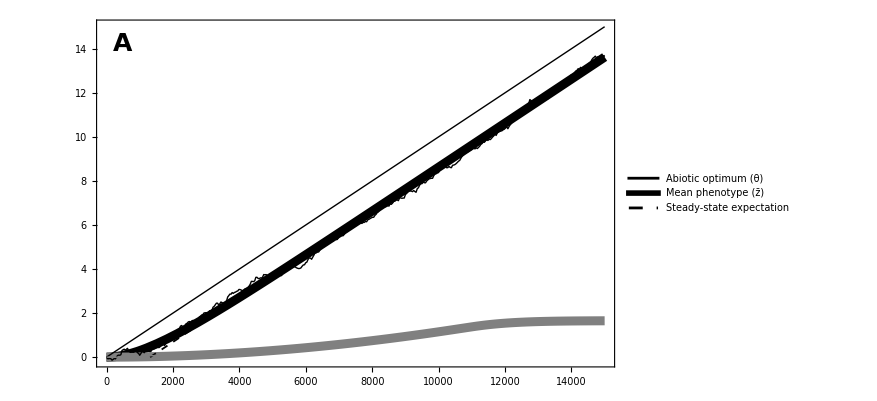

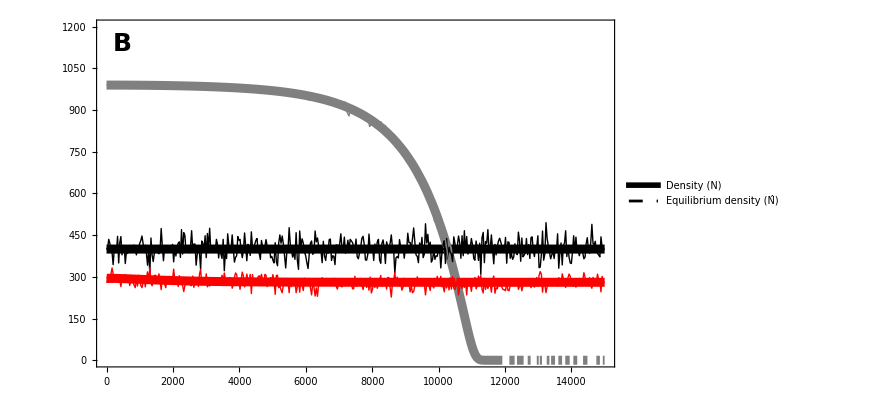

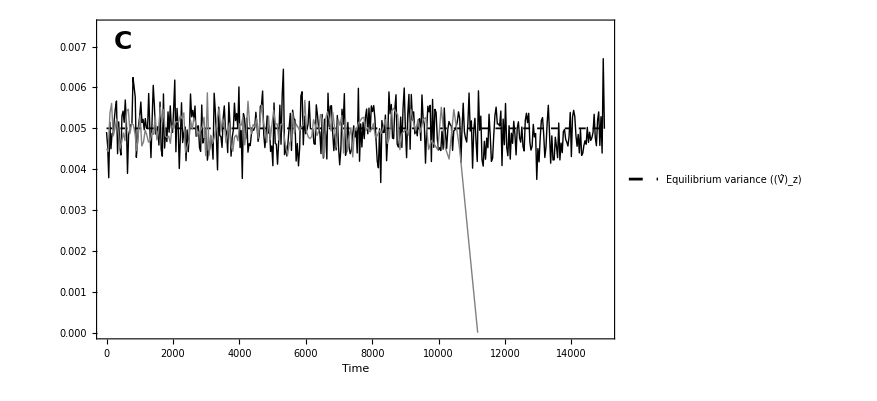

```mathematica
(*plotting colors*)
col1=Black;
col2=Red;
col3=Gray;

(*simulation results*)
rep="1";
simdir=datadir<>"SPECIALIST/HYDRA/";
zpdat=Import[simdir<>"zP_k1_r"<>rep<>".dat","CSV"];
Pdat = Import[simdir<>"P_k1_r"<>rep<>".dat"];
Zdat = Import[simdir<>"Z_k1_r"<>rep<>".dat"];
simdir2=datadir<>"SPECIALIST/HYDRA/NOPRED/";
zpdat2=Import[simdir2<>"zP_k1_r"<>rep<>".dat","CSV"];
Pdat2 = Import[simdir2<>"P_k1_r"<>rep<>".dat"];

(*parameters*)
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;
k=1/100; e=1/4;mP=1;
κ =1/1000;
tmax=15000;

(*initial conditions*)
z0=0;n0=mP/(e k);p0=(bmax (Rtot - n0)-mconst)/(bmax+k);

(*phenotypic variance*)
Vz=2 α^2 ; 

(*numerically solve coupled equation*)
cosol=NDSolve[{
z'[t]==(dbarzdtApp/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
(*z'[t]==(Normal[Series[dbarzdtApp/.γ->γ ϵ,{ϵ,0,1}]]/.ϵ->1/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),*)
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
z[0]==z0,
n[0]==n0,
P[0]==p0
},{z,n,P},{t,0,tmax}];

preysol=NDSolve[{
z'[t]==(dbarzdtApp/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
(*z'[t]==(Normal[Series[dbarzdtApp/.γ->γ ϵ,{ϵ,0,1}]]/.ϵ->1/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),*)
n'[t]==(dNdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
P'[t]==(dPdt/.N->n[t]/.P->P[t]/.θ->κ t/.barz->z[t]),
z[0]==z0,
n[0]==Rtot-mconst/bmax,
P[0]==0
},{z,n,P},{t,0,tmax}];

(*plot lag and optimal*)
zPlo=Plot[Evaluate[z[t]/.cosol],{t,0,tmax},PlotStyle->{col1,Thickness[0.01]}];
zPlo2=Plot[Evaluate[z[t]/.preysol],{t,0,tmax},PlotStyle->{col3,Thickness[0.01]}];
opt=Plot[κ t,{t,0,tmax},PlotStyle->{Black,Thick}];
(*plot predicted lag*)
predz=Plot[κ t-L/.LPeq,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed},PlotRange->{0,All}];
predz2=Plot[κ t-L/.Leq,{t,0,tmax},PlotStyle->{col3,Thickness[0.002],Dashed},PlotRange->{0,All}];
(*plot simulation results*)
zdat=ListPlot[Table[{Pdat[[i,1]],zpdat[[i,1]]},{i,1,Dimensions[Pdat][[1]],1}],PlotRange->All,PlotStyle->col1, Joined->True];
zdat2=ListPlot[Table[{Pdat2[[i,1]],zpdat2[[i,1]]},{i,1,Dimensions[Pdat2][[1]],1}],PlotRange->All,PlotStyle->col3, Joined->True];

Legended[
Show[
{zPlo,zPlo2,predz,predz2,opt,zdat,zdat2},
PlotRange->{{0,tmax},{0,All}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotype",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Thickness[0.1],Black],
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Abiotic optimum (θ)",LabelSize],
Style["Mean phenotype (z̄)",LabelSize],
Style["Steady-state expectation",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.725}
] 
]

(*Export[imagedir<>"GeneralistTemporalTrait.eps",%];*)

(*plot abundance*)
nPlot=Plot[Evaluate[n[t]/.cosol],{t,0,tmax},PlotStyle->{col1,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];
pPlot=Plot[Evaluate[P[t]/.cosol],{t,0,tmax},PlotStyle->{col2,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];
nPlot2=Plot[Evaluate[n[t]/.preysol],{t,0,tmax},PlotStyle->{col3,Thickness[0.01]},PlotRange->{0,Rtot*1.01}];
(*plot predicted abundance*)
predn=Plot[N/.NPeq[[3]]/.LPeq,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed}];
predp=Plot[P/.NPeq[[3]]/.LPeq,{t,0,tmax},PlotStyle->{col2,Thickness[0.002],Dashed}];
predn2=Plot[N/.NPeq[[2]]/.Leq,{t,0,tmax},PlotStyle->{col3,Thickness[0.002],Dashed}];
(*plot simulation results*)
ndat=ListPlot[Table[Pdat[[i]],{i,1,Dimensions[Pdat][[1]],1}],Joined->True,PlotStyle->col1];
ndat2=ListPlot[Table[Pdat2[[i]],{i,1,Dimensions[Pdat2][[1]],1}],Joined->True,PlotStyle->col3];
pdat=ListPlot[Table[Zdat[[i]],{i,1,Dimensions[Zdat][[1]],1}],Joined->True,PlotStyle->col2];

Legended[
Show[
{nPlot,nPlot2,pPlot,predn,predn2,predp,ndat,ndat2,pdat},
PlotRange->{{0,tmax},{0,Rtot*1.2}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.35]],
Directive[Darker[Black],Thickness[0.1],Dashed]
},
{
Style["Density (N)",LabelSize],
Style["Equilibrium density (N̂)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.55}
]
]

(*Export[imagedir<>"GeneralistTemporalDensity.eps",%];*)

(*plot equilibrium variance*)
eqvarPlot=Plot[Vz,{t,0,tmax},PlotStyle->{col1,Thickness[0.002],Dashed}];
(*plot simulation results*)
simvarPlot=ListPlot[Table[{Pdat[[i,1]],zpdat[[i,2]]},{i,1,Dimensions[Pdat][[1]],1}],PlotStyle->col1,Joined->True];
simvarPlot2=ListPlot[Table[{Pdat2[[i,1]],zpdat2[[i,2]]},{i,1,Dimensions[Pdat2][[1]],1}],PlotStyle->col3,Joined->True];

Legended[
Show[
{eqvarPlot,simvarPlot,simvarPlot2},
Frame->True, 
FrameLabel->{Style["Time",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,tmax},{0,1.5*Vz}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Phenotypic variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Black,Thickness[0.1],Dashed]
},
{
(*Style["Mean genetic variance (((σ̄)_(g,P))^2)",LabelSize],*)
Style["Equilibrium variance ((V̂)_z)",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.3,0.2}
]
]

(*Export[imagedir<>"GeneralistTemporalVariance.eps",%];*)

Clear[simdir,simdir2,knum,rep,zpdat,zpdat2,Pdat,Pdat2,bmax,mconst,Rtot,γ,α,Vz,tmax,z0,n0,κ,cosol,preysol,zPlo,zPlo2,opt,predz,predz2,predzc1,zdat,zdat2,pPlot,nPlot,nPlot2,predp,predn,predn2,pdat,ndat2,ndat2,eqvarPlot,simvarPlot,simvarPlot2,col1,col2,eqvarPlot2,e,k,mP,Zdat,p0,col3]
```

### Equilibrium solutions

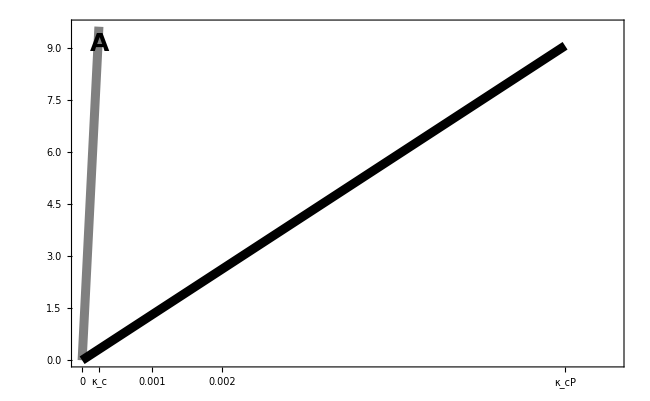

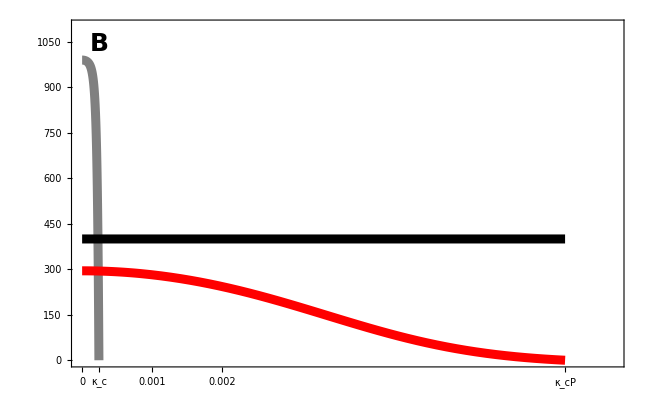

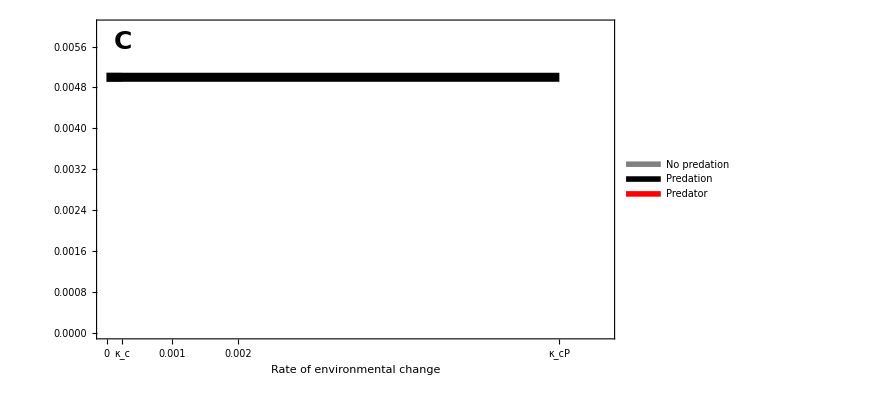

```mathematica
(*plotting colors*)
col1=Gray;
col2=Black;

(*(*simulation results*)
simdir=datadir<>"PUSH/CEQUALS0/Summary/";
(*simdir2=datadir<>"PUSHB/Summary/";*)
summdata=Import[simdir<>"summdata.dat"];
(*summdata2=Import[simdir2<>"summdata.dat"];*)*)

(*parameters*)
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;
e=1/4;mP=1;k=1/100;
 
(*equilibrium variance*)
Vz=2 α^2;

(*x-axis limit*)
xmax=1.1*κ/.kcp;
(*x-axis ticks*)
xnum=5;
xticks={0,0.001,0.002,{κ/.kc,Style["κ_c",col1,FontSize->TickSize]},{κ/.kcp,Style["κ_cP",col2,FontSize->TickSize]}};
(*max number of simulations to show*)
numsims=7;
numsims2=8;

Show[{
(*predicted lag*)
Plot[L/.Leq,{κ,0,κ/.kc},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}, Axes->False],
Plot[L/.LPeq,{κ,0,κ/.kcp},PlotStyle->{Thickness[0.01],col2},PlotRange->All](*,
(*observed lag +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[2]][[i]]},ErrorBar[1.96*summdata[[4]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[2]][[i]]},ErrorBar[1.96*summdata2[[4]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2]*)
},
PlotRange->{{0,xmax},All},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]}, 
FrameTicks->{{All,All},{xticks,All}},
ImagePadding->Pad,
FrameStyle->Directive[FontSize->TickSize],
(*PlotRangePadding->None,*)
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
ImageSize->FigureSize,
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Steady-state lag",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumLag.eps",%];*)

Show[{
(*predicted density*)
Plot[N/.NPeq[[2]]/.Leq,{κ,0,κ/.kc},PlotStyle->{Thickness[0.01],col1},PlotRange->{0,All}],
Plot[N/.NPeq[[3]],{κ,0,κ/.kcp},PlotStyle->{Thickness[0.01],col2},PlotRange->{0,All}],
Plot[P/.NPeq[[3]]/.LPeq,{κ,0,κ/.kcp},PlotStyle->{Thickness[0.01],Red},PlotRange->{0,All}](*,
(*observed density +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[5]][[i]]},ErrorBar[1.96*summdata[[7]][[i]]]},{i,1,Dimensions[summdata][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col1]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[5]][[i]]},ErrorBar[1.96*summdata2[[7]][[i]]]},{i,1,Dimensions[summdata2][[2]]}],PlotMarkers->{Automatic,Large},PlotStyle->col2]*)
},
PlotRange->{{0,xmax},{0,Rtot*1.1}},
Frame -> True, 
FrameLabel -> {Style["",LabelSize],Style["",LabelSize]},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Directive[FontColor->White],Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumDensity.eps",%];*)

Legended[
Show[{
(*predicted variance*)
Plot[Vz,{κ,0,κ/.kc},PlotStyle->{col1,Thickness[0.01]}],
Plot[Vz,{κ,0,κ/.kcp},PlotStyle->{col2,Thickness[0.01]}](*,
(*observed variance +- 1.96 SE*)
ErrorListPlot[Table[{{summdata[[1]][[i]],summdata[[8]][[i]]},ErrorBar[1.96*summdata[[10]][[i]]]},{i,1,numsims}],PlotMarkers->{Automatic,Large},PlotStyle->col1,Axes->False]*)(*,
ErrorListPlot[Table[{{summdata2[[1]][[i]],summdata2[[8]][[i]]},ErrorBar[1.96*summdata2[[10]][[i]]]},{i,1,numsims2}],PlotMarkers->{Automatic,Large},PlotStyle->col2,Axes->False]*)
},
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameTicks->{{All,All},{xticks,All}},
FrameTicksStyle->{{Black,Directive[FontColor->White]},{Black,Directive[FontColor->White]}},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRange->{{0,xmax},{0,0.006}},
(*PlotRangePadding->None,*)
ImageSize->FigureSize,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium variance",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[col1,Thickness[0.25]],
Directive[col2,Thickness[0.25]],
Directive[Red,Thickness[0.25]]
},
{
Style["No predation",LabelSize],
Style["Predation",LabelSize],
Style["Predator",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.25}
] 
]

(*Export[imagedir<>"SelectiveGeneralistEquilibriumVariance.eps",%];*)

Clear[simdir,simdir2,summdata,summdata2,bmax,mconst,Rtot,γ,γk,α,Vz,xmax,xticks,numsims,numsims2,k,e,mP,xnum,col1,col2]
```

## Are specialists more or less likely than generalists to help prey persist?

### Selective push (predate maladapted more)

#### Specialist

Approximate system of equations

```mathematica
dNdt=-bmax N (N+P-Rtot)-N (mmin+k P (1+γk (Vz+(barz-θ)^2))+γ (Vz+(barz-θ)^2));
dPdt=P (-mP+e k N (1+γk (Vz+(barz-θ)^2)));
dbarzdtApp=2 Vz γ (-barz+θ)+2 k P Vz γk (-barz+θ);
dbarzPdtApp=0;
```

Steady-state lag and equilibrium densities

```mathematica
FindEq=Solve[{dNdt==0,dPdt==0,dbarzdtApp==κ}/.barz->θ-L//Simplify,{P,N,L}];
```

Prey-only equilibrium

```mathematica
PreyOnlyEq=FindEq[[2]];
```

Prey and predator equilibrium

```mathematica
PreyPredEq=FindEq[[5]];
```

Plot parameter region where predator (and hence its prey) persist but the prey without the predator does not

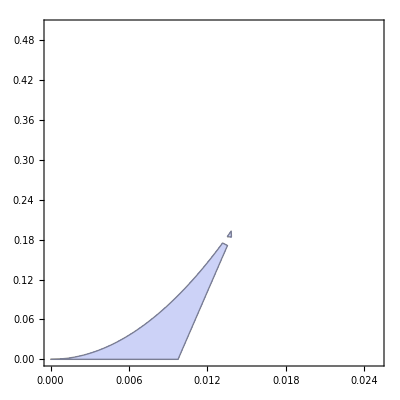

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
e=1/4;mP=1;k=1/100;
γk=1/10;
κ =1/100;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

RegionPlot[{(N/.PreyOnlyEq)<0&&(P/.PreyPredEq)>0},{κ,0,0.025},{γ,0,0.5}]

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

#### Generalist

Prey equilibrium density

```mathematica
neq=-(k+mmin-bmax Rtot+(L^2+Vz) γ+k (L^2+Vz) γk)/bmax/.{L->κ/(2 Vz γ+2 k Vz γk)}//Simplify
```

-(k+mmin-bmax Rtot+γ (Vz+κ^2/(2 Vz γ+2 k Vz γk)^2)+k γk (Vz+κ^2/(2 Vz γ+2 k Vz γk)^2))/bmax

Plot region where prey persists with generalist predation (extra mortality) but the prey without  generalist predation does not. Make rate of predation the rate of predation in the specialist case when there is no change in the environment and no abiotic selection on prey (ie. well adapted to constant environment)

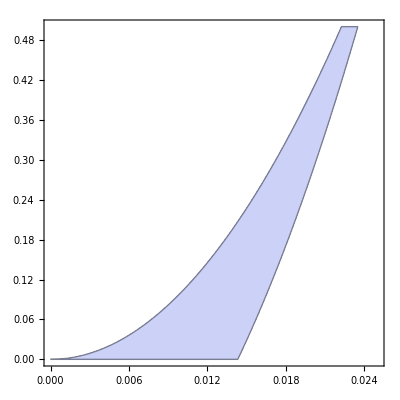

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
e=1/4;mP=1;k=1/100;
γk=1/10;
κ =1/100;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

(*Show[
Plot[neq/.γ->0.1,{κ,0,0.01}],
Plot[N/.PreyOnlyEq/.γ->0.1,{κ,0,0.01},PlotStyle->Dashed]
]*)

Clear[k]
kgen=k->(k P/.PreyPredEq/.κ->10^-6/.γ->0/.k->1/100);

RegionPlot[{(N/.PreyOnlyEq)<0&&(neq/.kgen)>0},{κ,0,0.025},{γ,0,0.5}]

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

#### Specialist vs. generalist

Because specialists get rarer as their prey do (at higher rates of environmental change or under stronger selection) this sometimes prevents them from pushing their prey effectively, and generalist predation is sometimes more likely to help prey persist:

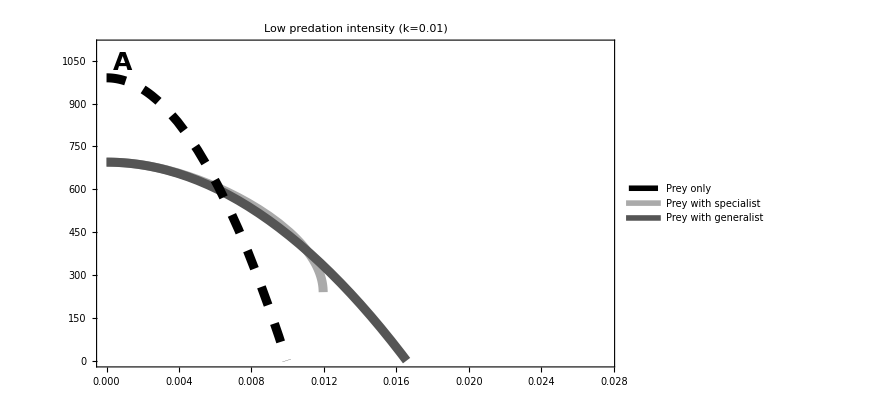

-Graphics-

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;α=1/20;Vz=2 α^2;e=1/4;mP=1;γk=1/10;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

Clear[k]
kspec=k->(k P/.PreyPredEq/.k->1/100); (*P changes with κ and γ*)
kgen=k->(k P/.PreyPredEq/.κ->10^-6/.γ->0/.k->1/100); (*P constant*)

(*where specialist case goes complex*)
neq/.kspec/.γ->0.1/.κ->0.01195994;
kcomplex=0.01195994;

Legended[
Show[
Plot[neq/.kspec/.γ->0.1,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Lighter[Gray]}],
Plot[neq/.γ->0.1/.kgen,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Darker[Gray]}],
Plot[N/.PreyOnlyEq/.γ->0.1,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
PlotRange->{{0,0.0275},{0,1.1*Rtot}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
PlotLabel->Style["Low predation intensity (k=0.01)",LabelSize],
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["*",LabelSize],{kcomplex,-30}]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Black],Thickness[0.2],Dashing[Medium]],
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Darker[Gray],Thickness[0.3]]
},
{
Style["Prey only",LabelSize],
Style["Prey with specialist",LabelSize],
Style["Prey with generalist",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistPushLowDensity.eps",%];

Legended[
Show[
RegionPlot[{
(N/.PreyOnlyEq)<0&&(neq/.kgen)>0(*&&Im[neq/.kspec]≠0*)
},
{κ,0,0.0275},{γ,0,0.7},
PlotStyle->Darker[Gray],
MaxRecursion->10
],
RegionPlot[{
(N/.PreyOnlyEq)<0(*&&(neq/.kgen)>0*)&&(neq/.kspec)>0
},
{κ,0,0.0275},{γ,0,0.7},
PlotStyle->Black,
MaxRecursion->10
],
Plot[0.1,{κ,0,0.0275},PlotStyle->{Black,Dashed}],
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Black,Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Abiotic selection strength (γ)",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False,
AspectRatio->1/GoldenRatio
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.3]],
Directive[Black,Thickness[0.3]]
},
{
Style["Only generalist helps",LabelSize],
Style["Specialist and generalist help",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.4,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistPushLowRegion.eps",%];

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

But can this go the other way? Can the decreased predation in the specialist case, due to demographic feedbacks, actually help make selection not too strong? This happens when we make predation intensity, k, a little stronger:

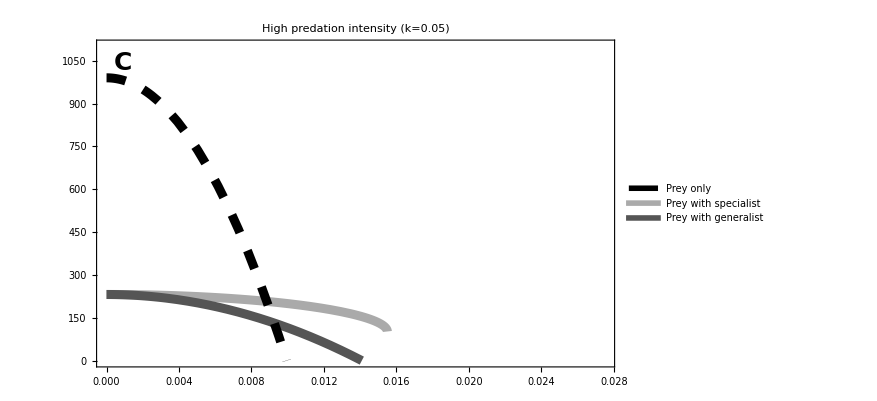

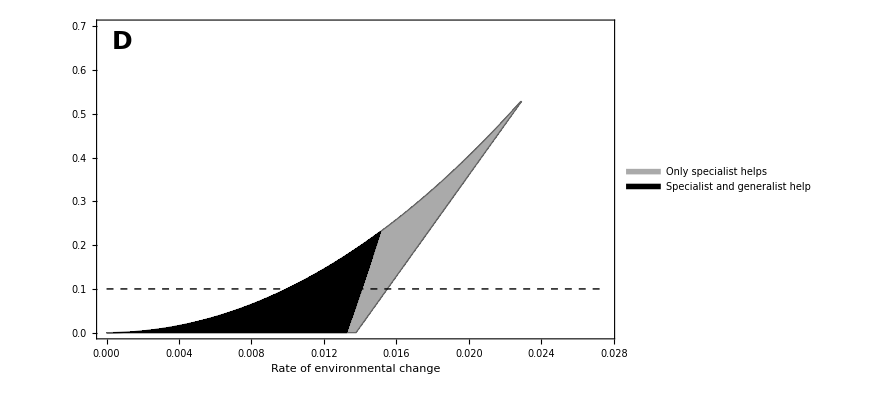

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;α=1/20;Vz=2 α^2;e=1/4;mP=1;γk=1/10;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

Clear[k]
kspec=k->(k P/.PreyPredEq/.k->1/20); (*P changes with κ and γ*)
kgen=k->(k P/.PreyPredEq/.κ->10^-6/.γ->0/.k->1/20); (*P constant*)

(*where specialist case goes complex*)
neq/.kspec/.γ->0.1/.κ->0.015504;
kcomplex=0.015504;

Legended[
Show[
Plot[neq/.kspec/.γ->0.1,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Lighter[Gray]}],
Plot[neq/.γ->0.1/.kgen,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Darker[Gray]}],
Plot[N/.PreyOnlyEq/.γ->0.1,{κ,0,0.0275},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
PlotRange->{{0,0.0275},{0,1.1*Rtot}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
PlotLabel->Style["High predation intensity (k=0.05)",LabelSize],
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree],
Text[Style["*",LabelSize],{kcomplex,-30}]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Black,Thickness[0.2],Dashing[Medium]],
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Darker[Gray],Thickness[0.3]]
},
{
Style["Prey only",LabelSize],
Style["Prey with specialist",LabelSize],
Style["Prey with generalist",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistPushHighDensity.eps",%];

Legended[
Show[
RegionPlot[{
(N/.PreyOnlyEq)<0&&(*(neq/.kgen)<0&&*)(neq/.kspec)>0
},
{κ,0,0.0275},{γ,0,0.7},
PlotStyle->Lighter[Gray],
MaxRecursion->10
],
RegionPlot[{
(N/.PreyOnlyEq)<0&&(neq/.kgen)>0(*||(neq/.kspec)>0}*)
},
{κ,0,0.0275},{γ,0,0.7},
PlotStyle->Black,
MaxRecursion->10
],
Plot[0.1,{κ,0,0.0275},PlotStyle->{Black,Dashed}],
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Directive[FontColor->White],Black},{Black,Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False,
AspectRatio->1/GoldenRatio
],
Placed[
LineLegend[{
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Black,Thickness[0.3]]
},
{
Style["Only specialist helps",LabelSize],
Style["Specialist and generalist help",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.4,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistPushHighRegion.eps",%];

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

### Evolutionary hydra effect (continuous breeding)

#### Specialist

Approximate system of equations

```mathematica
dNdt=-N (mconst+k P)-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) N (N+P-Rtot) √(Vz/(1+Vz γ)))/(√Vz);
dPdt=-mP P+e k N P;
dbarzdtApp=-(bmax ⅇ^(-(γ (barz-θ)^2)/(2+2 Vz γ)) (-N-P+Rtot) Vz γ (barz-θ))/(2 (1+Vz γ)^(3/2));
dbarzPdtApp=0;
```

The equilibrium population densities are

```mathematica
NPeq=Solve[{dNdt==0,dPdt==0}/.barz->θ-L//Simplify,{P,N}]//FullSimplify
```

{{P→0,N→0},{P→0,N→(-ⅇ^((L^2 γ)/(2+2 Vz γ)) mconst √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))},{P→-(e ⅇ^((L^2 γ)/(2+2 Vz γ)) k mconst √Vz+bmax mP √(Vz/(1+Vz γ))-bmax e k Rtot √(Vz/(1+Vz γ)))/(e ⅇ^((L^2 γ)/(2+2 Vz γ)) k^2 √Vz+bmax e k √(Vz/(1+Vz γ))),N→mP/(e k)}}

And with a separation of timescales the steady-state lag at the predator-prey equilibrium is, assuming weak selection,

```mathematica
LPeq=Solve[Normal[Series[{dbarzdtApp==κ}/.barz->θ-L/.NPeq[[3]]/.γ->γ ϵ,{ϵ,0,1}]]/.ϵ->1,{L}]//Simplify//Flatten
```

{L→(2 e (bmax+k) κ)/(bmax (-mP+e (mconst+k Rtot)) Vz γ)}

At the prey-only equilibrium we have

```mathematica
Leq=Solve[{dbarzdtApp==κ}/.barz->θ-L/.NPeq[[2]],{L}]//Simplify//Flatten
```

{L→(2 √(Vz/(1+Vz γ)) (1+Vz γ)^(3/2) κ)/(mconst Vz^(3/2) γ)}

Plot parameter region where the predator persist (and hence so do their prey) but the prey without the predator does not

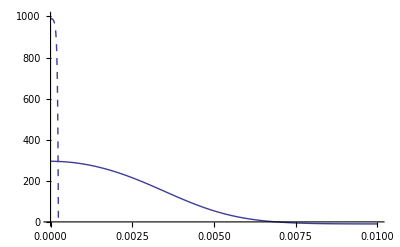

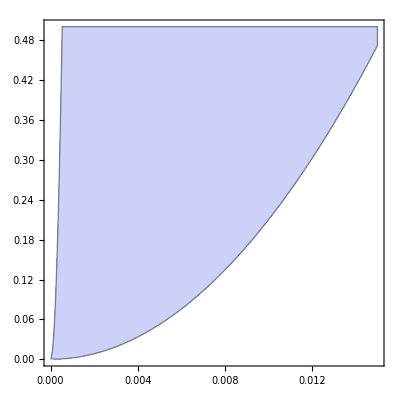

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
k=1/100;e=1/4;mP=1;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

Show[
Plot[N/.NPeq[[2]]/.Leq/.γ->1/10,{κ,0,0.01},PlotRange->{0,Rtot},PlotStyle->Dashed],
Plot[P/.NPeq[[3]]/.LPeq/.γ->1/10,{κ,0,0.01}]
]
(*0>N/.NPeq[[2]]/.Leq/.γ->1/10/.κ->0.002
0<N/.NPeq[[2]]/.LPeq/.γ->1/10/.κ->0.002*)
RegionPlot[{(N/.NPeq[[2]]/.Leq)<0&&(P/.NPeq[[3]]/.LPeq)>0},{κ,0,0.015},{γ,0,0.5}]

Clear[bmax,mconst,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

#### Generalist

Prey equilibrium density

```mathematica
neq=(-ⅇ^((L^2 γ)/(2+2 Vz γ)) (k+mconst) √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))/.{L->(2 √(Vz/(1+Vz γ)) (1+Vz γ)^(3/2) κ)/((k+mconst) Vz^(3/2) γ)}//Simplify
```

(-ⅇ^((2 (1+Vz γ) κ^2)/((k+mconst)^2 Vz^2 γ)) (k+mconst) √Vz+bmax Rtot √(Vz/(1+Vz γ)))/(bmax √(Vz/(1+Vz γ)))

Plot region where prey persists with generalist predation (extra mortality) but the prey without  generalist predation does not. Make rate of predation the rate of predation in the specialist case when there is no change in the environment and no abiotic selection on prey (ie. well adapted to constant environment)

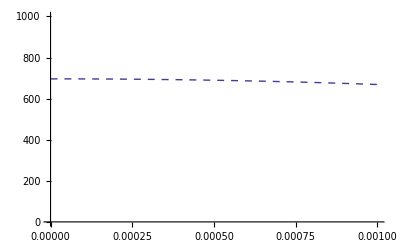

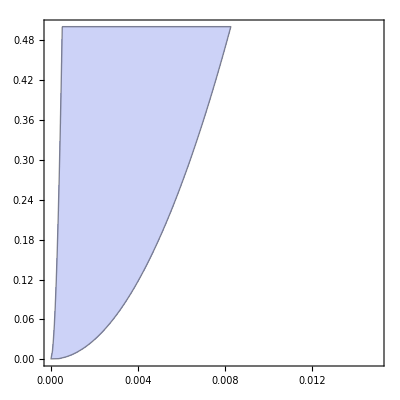

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
k=1/100;e=1/4;mP=1;

(*N/.PreyOnlyEq//N
N/.PreyPredEq//N
P/.PreyPredEq//N*)

Clear[γ,κ]

Clear[k]
kgen=k->(k P/.NPeq[[3]]/.LPeq/.κ->10^-6/.γ->10^-6/.k->1/100);

Show[
Plot[neq/.kgen/.γ->1/10,{κ,0,0.001},PlotRange->{0,Rtot},PlotStyle->Dashed],
Plot[neq/.k->0/.γ->1/10,{κ,0,0.001}]
]

RegionPlot[{(neq/.k->0)<0&&(neq/.kgen)>0},{κ,0,0.015},{γ,0,0.5}]

Clear[bmax,mconst,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

#### Specialist vs. generalist

Because specialists get rarer as their prey do (at higher rates of environmental change or under stronger selection) this sometimes prevents them from pushing their prey effectively, and generalist predation is sometimes more likely to help prey persist:

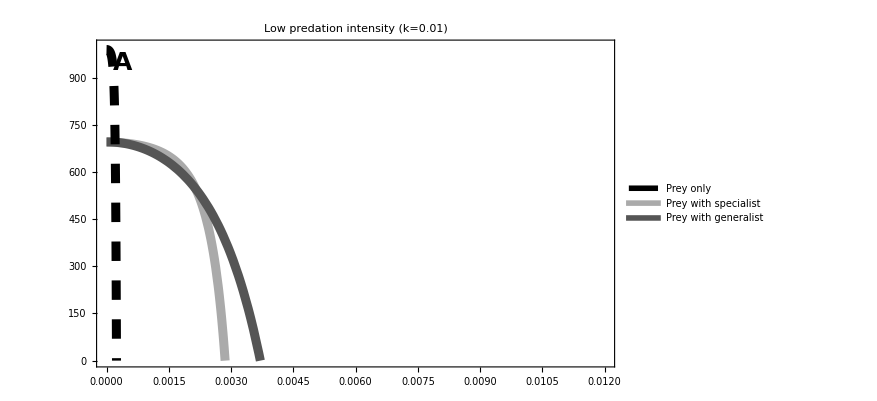

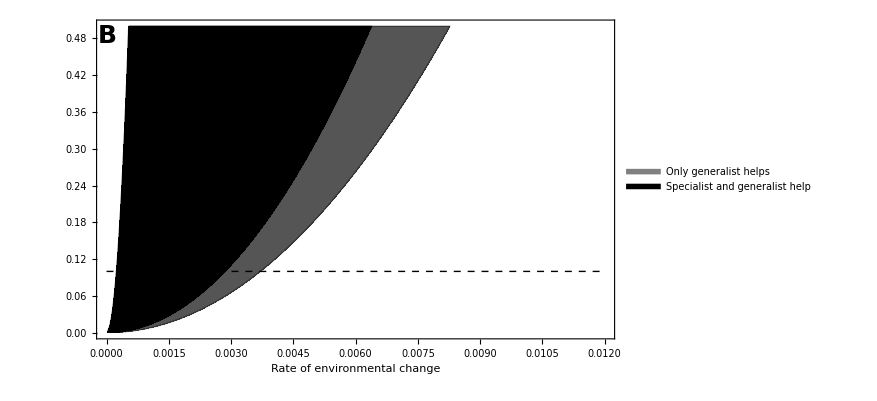

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
k=1/100;e=1/4;mP=1;

Clear[γ,κ]

Clear[k]
kspec=k->(k P/.NPeq[[3]]/.LPeq/.k->1/100); (*P changes with κ and γ*)
kgen=k->(k P/.NPeq[[3]]/.LPeq/.κ->10^-6/.γ->10^-6/.k->1/100); (*P constant*)

Legended[
Show[
Plot[neq/.kspec/.γ->0.1,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Lighter[Gray]}],
Plot[neq/.γ->0.1/.kgen,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Darker[Gray]}],
Plot[N/.NPeq[[2]]/.Leq/.γ->0.1,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
PlotRange->{{0,0.012},{0,Rtot}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
PlotLabel->Style["Low predation intensity (k=0.01)",LabelSize],
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Black,Thickness[0.2],Dashing[Medium]],
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Darker[Gray],Thickness[0.3]]
},
{
Style["Prey only",LabelSize],
Style["Prey with specialist",LabelSize],
Style["Prey with generalist",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistHydraLowDensity.eps",%];

Legended[
Show[
RegionPlot[{
(N/.NPeq[[2]]/.Leq)<0&&(neq/.kgen)>0(*&&(neq/.kspec)<0*)
},
{κ,0,0.012},{γ,0,0.5},
MaxRecursion->2,
PlotStyle->Darker[Gray]
],
RegionPlot[{
(N/.NPeq[[2]]/.Leq)<0&&(neq/.kgen)>0&&(neq/.kspec)>0
},
{κ,0,0.012},{γ,0,0.5},
MaxRecursion->2,
PlotStyle->Black
],
Plot[0.1,{κ,0,0.012},PlotStyle->{Black,Dashed}],
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Black,Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@{0.02,0.95}],
Rotate[Text[Style["Abiotic selection strength (γ)",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False,
AspectRatio->1/GoldenRatio
],
Placed[
LineLegend[{
Directive[Gray,Thickness[0.3]],
Directive[Black,Thickness[0.3]]
},
{
Style["Only generalist helps",LabelSize],
Style["Specialist and generalist help",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.11}
]
]

Export[imagedir<>"SpecialistVsGeneralistHydraLowRegion.eps",%];

(*(neq/.kspec)/.κ->0.009741/.γ->0.0299*)

Clear[bmax,mconst,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

But can this go the other way? Can the decreased predation in the specialist case, due to demographic feedbacks, actually help make selection not too strong? This happens when we make predation intensity, k, a little stronger:

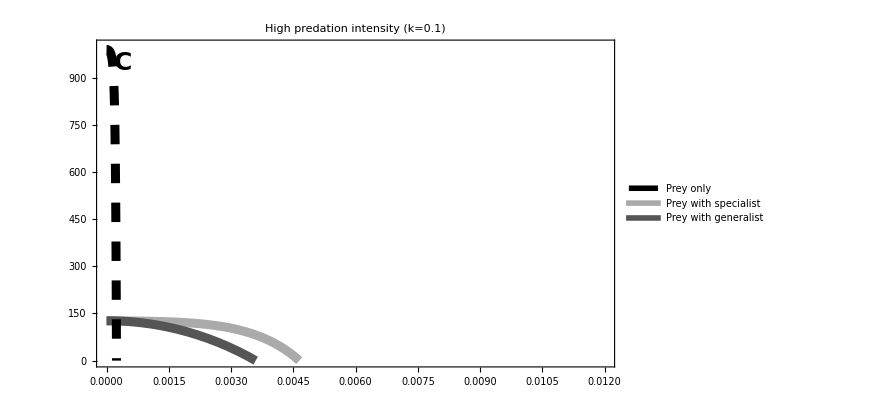

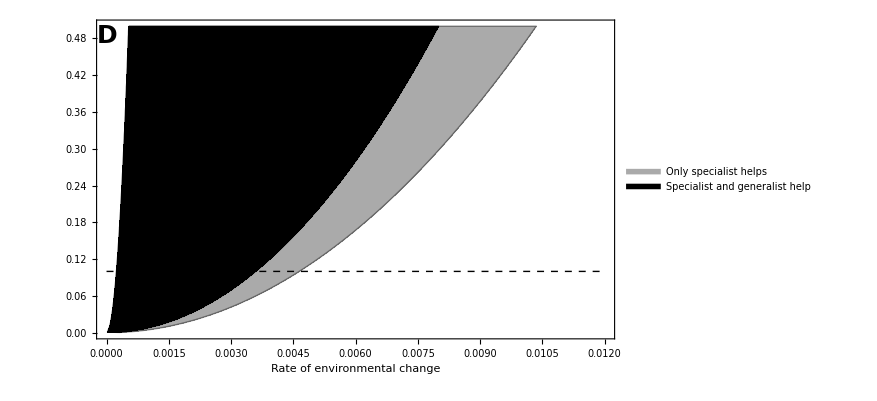

```mathematica
bmax=1/100;mconst=1/10;Rtot=1000;
γ=1/10;α=1/20;Vz=2 α^2;
k=1/100;e=1/4;mP=1;

Clear[γ,κ]

Clear[k]
kspec=k->(k P/.NPeq[[3]]/.LPeq/.k->1/10); (*P changes with κ and γ*)
kgen=k->(k P/.NPeq[[3]]/.LPeq/.κ->10^-6/.γ->10^-6/.k->1/10); (*P constant*)

Legended[
Show[
Plot[neq/.kspec/.γ->0.1,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Lighter[Gray]}],
Plot[neq/.γ->0.1/.kgen,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Darker[Gray]}],
Plot[N/.NPeq[[2]]/.Leq/.γ->0.1,{κ,0,0.012},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
PlotRange->{{0,0.012},{0,Rtot}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
PlotLabel->Style["High predation intensity (k=0.1)",LabelSize],
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Black,Thickness[0.2],Dashing[Medium]],
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Darker[Gray],Thickness[0.3]]
},
{
Style["Prey only",LabelSize],
Style["Prey with specialist",LabelSize],
Style["Prey with generalist",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Export[imagedir<>"SpecialistVsGeneralistHydraHighDensity.eps",%];

Legended[
Show[
RegionPlot[{
(N/.NPeq[[2]]/.Leq)<0(*&&(neq/.kgen)<0*)&&(neq/.kspec)>0
},
{κ,0,0.012},{γ,0,0.5},
PlotStyle->Lighter[Gray]
],
RegionPlot[{
(N/.NPeq[[2]]/.Leq)<0&&(neq/.kgen)>0(*&&(neq/.kspec)>0*)
},
{κ,0,0.012},{γ,0,0.5},
PlotStyle->Black
],
Plot[0.1,{κ,0,0.012},PlotStyle->{Black,Dashed}],
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Black,Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["D",LabelSize,Bold],Scaled@{0.02,0.95}],
Rotate[Text[Style["Abiotic selection strength (γ)",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False,
AspectRatio->1/GoldenRatio
],
Placed[
LineLegend[{
Directive[Lighter[Gray],Thickness[0.3]],
Directive[Black,Thickness[0.3]]
},
{
Style["Only specialist helps",LabelSize],
Style["Specialist and generalist help",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.11}
]
]

Export[imagedir<>"SpecialistVsGeneralistHydraHighRegion.eps",%];

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ]
```

### Selective push (trait-matching coevolution)

#### Specialist

Approximate system of equations

```mathematica
dNdt=1/2 N *(-2 mmin-2 bmax (N+P-Rtot)+k P (-2+((barz-barzP)^2+Vz+VzP) γk)-γ (Vz+(barz-θ)^2));
dPdt=-1/2 P (2 mP+e k N (-2+((barz-barzP)^2+Vz+VzP) γk));
dbarzdtApp=(barz k P-barzP k P) Vz γk+Vz γ (-barz+θ);
dbarzPdtApp=1/2 (barz-barzP) e k N VzP γk;
```

The steady-state lags and equilibrium population sizes

```mathematica
CoevoEq=Solve[{dbarzdtApp==κ,dbarzPdtApp==κ,dNdt==0,dPdt==0}/.barzP->barz-LP/.barz->θ-L//Simplify,{L,LP,P,N}];
```

In the prey-only case we have

```mathematica
PreyOnlyCoevo=CoevoEq[[5]];
```

And in the full community we have

```mathematica
FullCoevo=CoevoEq[[3]];
```

Plot parameter region where predator (and hence its prey) persist but the prey without the predator does not

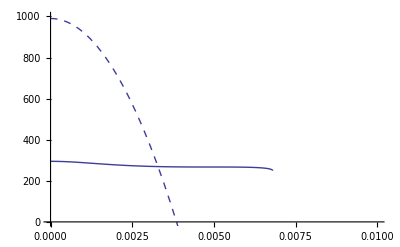

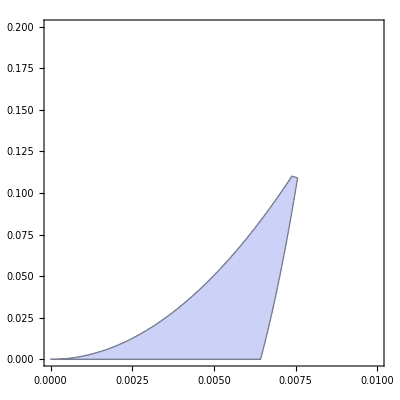

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
Vz=2 α^2;VzP=Vz;

Clear[γ,κ]

Show[
Plot[P/.FullCoevo/.γ->0.03,{κ,0,0.01},PlotRange->{0,Rtot}],
Plot[N/.PreyOnlyCoevo/.γ->0.03,{κ,0,0.01},PlotStyle->Dashed]
]

RegionPlot[{(N/.PreyOnlyCoevo)<0&&(P/.FullCoevo)>0},{κ,0,0.01},{γ,0,0.2}]

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ,VzP]
```

#### Generalist (mean predator trait value evolves as it does in specialist case)

Equations for change in prey popn size in terms of P and lags

```mathematica
dNdt=1/2 N *(-2 mmin-2 bmax (N+P-Rtot)+k P (-2+((barz-barzP)^2+Vz+VzP) γk)-γ (Vz+(barz-θ)^2));
```

Equilibrium prey population size in terms of P and lags

```mathematica
neq=Solve[{dNdt==0}/.barzP->barz-LP/.barz->θ-L//Simplify,{N}]
```

{{N→0},{N→(-2 mmin-2 bmax P-2 k P+2 bmax Rtot-L^2 γ-Vz γ+k LP^2 P γk+k P Vz γk+k P VzP γk)/(2 bmax)}}

Plot region where prey persists with generalist predation (extra mortality) but the prey without  generalist predation does not.

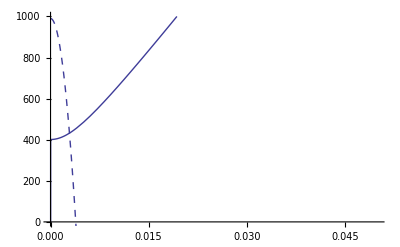

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
Vz=2 α^2;VzP=Vz;

Clear[γ,κ]

Show[
Plot[N/.neq[[2]]/.P->(P/.FullCoevo/.κ->10^-6)/.FullCoevo/.γ->0.03,{κ,0,0.05},PlotRange->{0,Rtot}],
Plot[N/.PreyOnlyCoevo/.γ->0.03,{κ,0,0.01},PlotStyle->Dashed]
]

(*RegionPlot[{(N/.PreyOnlyCoevo)<0&&Im[(N/.FullCoevoGen/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6))]<10^-6},{κ,0,0.01},{γ,0,0.2}]*)

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ,VzP]
```

So if we keep the same lags as in the specialist (coevolutionary) case but make predator density constant, the prey never go extinct because the predator can push forever. One way the coevolving generalist can hurt prey persistence is if the predation intensity is so high that it causes prey extinction in a constant environment (the same thing happens with the specialist, red)

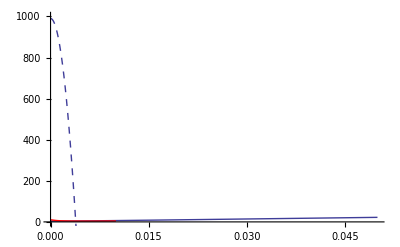

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/1;e=1;mP=4;
α=1/20;αP=1/20;
Vz=2 α^2;VzP=Vz;

Clear[γ,κ]

Show[
Plot[N/.neq[[2]]/.P->(P/.FullCoevo/.κ->10^-6)/.FullCoevo/.γ->0.03,{κ,0,0.05},PlotRange->{0,Rtot}],
Plot[N/.PreyOnlyCoevo/.γ->0.03,{κ,0,0.01},PlotStyle->Dashed],
Plot[P/.FullCoevo/.γ->0.03,{κ,0,0.01},PlotRange->{0,Rtot},PlotStyle->Red]
]

(*RegionPlot[{(N/.PreyOnlyCoevo)<0&&Im[(N/.FullCoevoGen/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6))]<10^-6},{κ,0,0.01},{γ,0,0.2}]*)

Clear[bmax,mmin,Rtot,γ,α,Vz,e,mP,k,γk,κ,VzP]
```

#### Generalist (no selection from predation)

Approximate system of equations

```mathematica
dNdt=1/2 N *(-2 mmin-2 bmax (N+P-Rtot)+k P (-2+((barz-barzP)^2+Vz+VzP) γk)-γ (Vz+(barz-θ)^2));
dPdt=0;
dbarzdtApp=(barz k P-barzP k P) Vz γk+Vz γ (-barz+θ);
dbarzPdtApp=0;
```

The equilibrium prey mean trait and density when the prey don’t feel selection from predators and density remains at P

```mathematica
CoevoEq=Solve[{dbarzdtApp==κ,dNdt==0}/.γk->0/.barz->θ-L//Simplify,{L,N}];
```

In the full community we have

```mathematica
FullCoevoGen2=CoevoEq[[2]]
```

{L→κ/(Vz γ),N→(-2 mmin Vz^2 γ-2 bmax P Vz^2 γ-2 k P Vz^2 γ+2 bmax Rtot Vz^2 γ-Vz^3 γ^2-κ^2)/(2 bmax Vz^2 γ)}

Plot region where prey persists with generalist predation (extra mortality) but the prey without  generalist predation does not

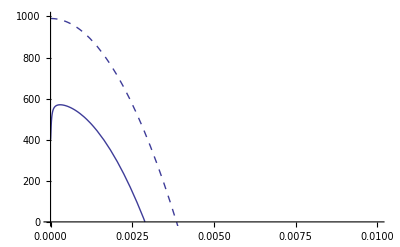

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=1/2;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
Vz=2 α^2;VzP=2 αP^2;

Clear[γ,κ]

Show[
Plot[N/.FullCoevoGen2/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6)/.γ->0.03,{κ,0,0.01},PlotRange->{0,Rtot}],
Plot[N/.PreyOnlyCoevo/.γ->0.03,{κ,0,0.01},PlotStyle->Dashed]
]

(*RegionPlot[{(N/.PreyOnlyEq)<0&&(N/.FullCoevo)>0},{κ,0,0.025},{γ,0,0.5}]*)

Clear[bmax,mmin,Rtot,γ,α,αP,Vz,e,mP,k,γk,κ,VzP]
```

#### Specialist vs. generalist(s)

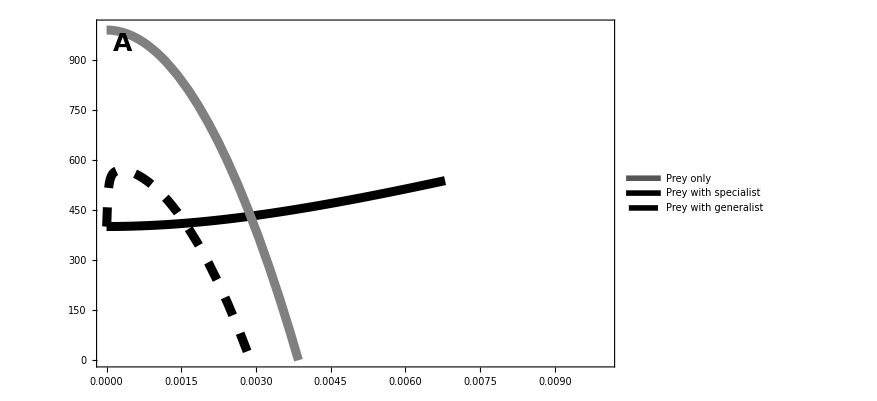

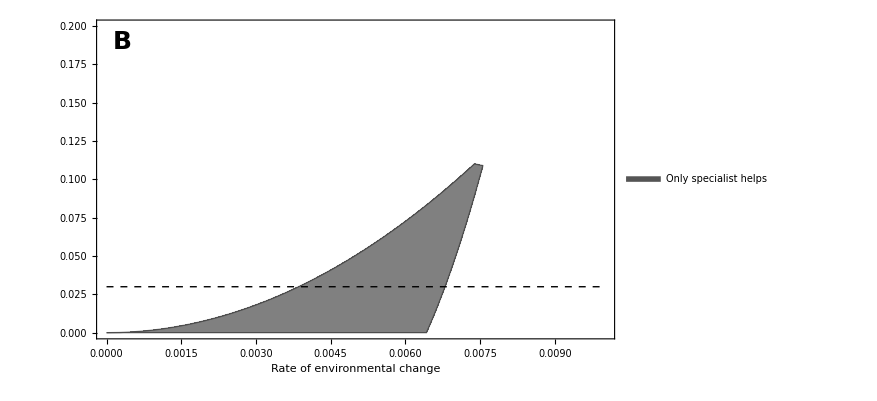

```mathematica
bmax=1/100;mmin=1/10;Rtot=1000;
γ=3/100;α=1/20;
γk=50/100;k=1/100;e=1;mP=4;
α=1/20;αP=1/20;
Vz=2 α^2;VzP=Vz;

Clear[γ,κ]

(*Plot[Re[P/.FullCoevo/.γ->0.03],{κ,0,0.01}]*)
kc=κ/.FindRoot[Re[P/.FullCoevo/.γ->0.03]-MinValue[Re[P/.FullCoevo/.γ->0.03],κ],{κ,0.0065}];

Legended[
Show[
Plot[N/.FullCoevo/.γ->0.03,{κ,0,kc},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black}],
Plot[N/.FullCoevoGen2/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6)/.γ->0.03,{κ,0,0.01},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[N/.PreyOnlyCoevo/.γ->0.03,{κ,0,0.01},PlotRange->{0,Rtot},PlotStyle->{Thickness[0.01],Gray}],
PlotRange->{{0,0.01},{0,Rtot}},
Frame->True, 
FrameLabel->{Style["",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Directive[FontColor->White],Black}},
ImageSize->FigureSize,
(*PlotLabel->Style["Predation intensity (k=0.01)",LabelSize],*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Equilibrium density",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[{
Directive[Darker[Gray],Thickness[0.2]],
Directive[Darker[Black],Thickness[0.2]],
Directive[Darker[Black],Thickness[0.2],Dashing[Medium]]
},
{
Style["Prey only",LabelSize],
Style["Prey with specialist",LabelSize],
Style["Prey with generalist",LabelSize]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.7,0.8}
]
]

Legended[
Show[
RegionPlot[{
(N/.PreyOnlyCoevo)<0&&
(*(N/.FullCoevoGen2/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6))<0&&*)
(*Im[N/.FullCoevoGen/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6)]≠0&&*)
(P/.FullCoevo)>0
},
{κ,0,0.01},{γ,0,0.2},
PlotStyle->Gray
],
RegionPlot[{
(N/.PreyOnlyCoevo)<0&&
(N/.FullCoevoGen2/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6))>0(*&&
(*Im[N/.FullCoevoGen/.P->(P/.FullCoevo/.γ->10^-6/.κ->10^-6)]≠0&&*)
(P/.FullCoevo)>0*)
},
{κ,0,0.01},{γ,0,0.2},
PlotStyle->Lighter[Gray]
],
Plot[0.03,{κ,0,0.01},PlotStyle->{Black,Dashed}],
Frame->True, 
FrameLabel->{Style["Rate of environmental change",LabelSize],Style["",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
PlotRangePadding->None,
FrameTicksStyle->{{Black,Black},{Black,Black}},
ImageSize->FigureSize,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["Abiotic selection strength (γ)",LabelSize],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False,
AspectRatio->1/GoldenRatio
],
Placed[
LineLegend[{
Directive[Darker[Gray],Thickness[0.3]](*,
Directive[Lighter[Gray],Thickness[0.3]]*)
},
{
Style["Only specialist helps",LabelSize](*,
Style["Predation helps",LabelSize]*)
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
{0.75,0.75}
]
]

Clear[bmax,mmin,Rtot,γ,α,αP,Vz,e,mP,k,γk,κ,VzP,kc]
```

The story here is that coevolution can help by acting as a selective push, but if the predator is a generalist and hence its trait value does not track the prey’s, then it cannot help the prey adapt and persist.